## Dynamics of the autonomous system L = L_EH + ξ L_YM +α/m_p^2 L4_1 + κ/m_p^2 L4_2 + θ_4/m_p^2 L4^_Curv+ λ/m_p^2 L4_3 + χ_1 L_(A^4)^(1) + χ_2 L_(A^4)^(2) + χ_3/m_p^2 L_(G^2 A^2)^(1) + χ_4/m_p^2L_(G^2 A^2)^(2) + θ_1 L1^_Curv [ ϵ≡ -H^•/H^2 , P≡ ψ^(••)/(m_p H^2) , X≡ψ^•/(√2 m_p H) , Y≡ψ/(√2 m_p) , Z≡(ψ F)/(√(2 m_p H))≡(ψ (g^2 ξ-6 χ_1-2 χ_2)^(1/4))/(√(2 m_p H)) ] L_(A^4)^(1)=(A_μ^a A_a^μ)(A_ν^b A_b^ν) , L_(A^4)^(2)=(A_μ^a A_b^μ)(A_ν^b A_a^ν) , L_(G^2 A^2)^(1)=(A_μ^a A_νa^)(G_b^μρ G_ρ^(ν b)) , L_(G^2 A^2)^(2)=(A_μ^a A_νb^)(G_^μρb G_ρa^ν) , L4^_Curv=L_μνρσ (A^μa A^νb)(A_ρa^A_σb^) .

## 1. Initialization and global variables

```mathematica
ClearAll["Global`*"]
Needs["Notation`"]
$Assumptions=_∈Reals;
Symbolize[ParsedBoxWrapper[SubscriptBox["_","_"]]]

(* In order to convert variables from MapleEOM to variables from EOM, one must perform the transformation {x=X; y=Y/X; z=Z/(F^4 X)}. *)

vars={ξ,α,κ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 4],Subscript[θ, 1],Subscript[Ω, r],Subscript[Ω, m]};
names={YM,alpha,kappa,theta4,chi1,chi2,chi3,chi4,theta1,Hot,Cold};
Fval=(q^2*ξ - 6 Subscript[χ, 1]-2 Subscript[χ, 2])^(1/4);
ToFs[f_]:=f/.q->Sqrt[(F^4+6 Subscript[χ, 1]+2 Subscript[χ, 2])/ξ];
NoMoreZs[f_]:=Simplify[f/.Z->Zval//ToFs,ψ∈Reals];
NoMoreFPϵ[f_]:=((f/.{P->Pval,ϵ->ϵval})//ToFs)/.{F->Fval}//Simplify;
CCoeffs[f_]:=Collect[f,vars];
ToLimit[f_]:=f/.{Z->γ X, Y->β X,ϵ->0};
```

```mathematica
(* Evolution equations are defined *)

fried=-1+(10 X^2 Y^2-188 X Y^3-32 Y^4) α+(8 X Y+6 Y^2) Subscript[θ, 1]+(-64 X Y^3-32 Y^4) Subscript[θ, 4]+(2 X^2 Y^2-20 X Y^3-12 Y^4) κ+(X^2+2 X Y+Y^2+(2*q^2*Z^4)/F^4) ξ-(4*Z^4/F^4)(3 Subscript[χ, 1]+Subscript[χ, 2])+(-4 X^2 Y^2-8 X Y^3-4 Y^4) (Subscript[χ, 3]+Subscript[χ, 4])+Subscript[Ω, m]+Subscript[Ω, r] //Expand//CCoeffs;

eq1=3-2 ϵ+α (614 X^2 Y^2+104 √2 P Y^3+316 X Y^3-340 Y^4+124 Y^4 ϵ)+(-8 X^2-4 √2 P Y-24 X Y-6 Y^2+4 Y^2 ϵ) Subscript[θ, 1]+(192 X^2 Y^2+32 √2 P Y^3+256 X Y^3+32 Y^4) Subscript[θ, 4]+(70 X^2 Y^2+12 √2 P Y^3+108 X Y^3+24 Y^4-4 Y^4 ϵ) κ+(X^2+2 X Y+Y^2+(2*q^2*Z^4)/F^4) ξ-(4*Z^4/F^4)(3 Subscript[χ, 1]+Subscript[χ, 2])+(4 X^2 Y^2+8 X Y^3+4 Y^4)( Subscript[χ, 3]+Subscript[χ, 4])+Subscript[Ω, r]//Expand//CCoeffs;

eq2=α (10 X^2 Y+5 √2 P Y^2+30 X Y^2-218 Y^3+94 Y^3 ϵ)+(6 Y-4 Y ϵ) Subscript[θ, 1]+(-32 Y^3+32 Y^3 ϵ) Subscript[θ, 4]+(2 X^2 Y+√2 P Y^2+6 X Y^2-6 Y^3+10 Y^3 ϵ) κ+(P/√2+3 X+2 Y+(4*q^2*Z^4)/(F^4*Y)-Y ϵ) ξ-(8*Z^4/(F^4*Y))(3 Subscript[χ, 1]+Subscript[χ, 2])+(-4 X^2 Y-2 √2 P Y^2-12 X Y^2-4 Y^3+4 Y^3 ϵ) (Subscript[χ, 3]+Subscript[χ, 4])//Expand//CCoeffs;

Print["\n\nFried → ",fried," == 0"];Print["\nEq1 → ",eq1," == 0"];Print["\nEq2 → ",eq2," == 0\n\n"];
```

Fried → -1+(10 X^2 Y^2-188 X Y^3-32 Y^4) α+(8 X Y+6 Y^2) θ_1+(-64 X Y^3-32 Y^4) θ_4+(2 X^2 Y^2-20 X Y^3-12 Y^4) κ+(X^2+2 X Y+Y^2+(2 q^2 Z^4)/F^4) ξ-(12 Z^4 χ_1)/F^4-(4 Z^4 χ_2)/F^4+(-4 X^2 Y^2-8 X Y^3-4 Y^4) χ_3+(-4 X^2 Y^2-8 X Y^3-4 Y^4) χ_4+Ω_m+Ω_r == 0

Eq1 → 3-2 ϵ+α (614 X^2 Y^2+104 √2 P Y^3+316 X Y^3-340 Y^4+124 Y^4 ϵ)+(-8 X^2-4 √2 P Y-24 X Y-6 Y^2+4 Y^2 ϵ) θ_1+(192 X^2 Y^2+32 √2 P Y^3+256 X Y^3+32 Y^4) θ_4+(70 X^2 Y^2+12 √2 P Y^3+108 X Y^3+24 Y^4-4 Y^4 ϵ) κ+(X^2+2 X Y+Y^2+(2 q^2 Z^4)/F^4) ξ-(12 Z^4 χ_1)/F^4-(4 Z^4 χ_2)/F^4+(4 X^2 Y^2+8 X Y^3+4 Y^4) χ_3+(4 X^2 Y^2+8 X Y^3+4 Y^4) χ_4+Ω_r == 0

Eq2 → α (10 X^2 Y+5 √2 P Y^2+30 X Y^2-218 Y^3+94 Y^3 ϵ)+(6 Y-4 Y ϵ) θ_1+(-32 Y^3+32 Y^3 ϵ) θ_4+(2 X^2 Y+√2 P Y^2+6 X Y^2-6 Y^3+10 Y^3 ϵ) κ+(P/(√2)+3 X+2 Y+(4 q^2 Z^4)/(F^4 Y)-Y ϵ) ξ-(24 Z^4 χ_1)/(F^4 Y)-(8 Z^4 χ_2)/(F^4 Y)+(-4 X^2 Y-2 √2 P Y^2-12 X Y^2-4 Y^3+4 Y^3 ϵ) χ_3+(-4 X^2 Y-2 √2 P Y^2-12 X Y^2-4 Y^3+4 Y^3 ϵ) χ_4 == 0

```mathematica
(* Friedmann equation is solved for Z *)
solu=Solve[fried==0/.Z->(Z4)^(1/4),Z4]//Simplify;
Zval=(solu[[1,1,2]])^(1/4)(ψ/Abs[ψ])//ToFs //Simplify;

(* The real solution for Z whose magnitude is given by |Z| = (Z^4)^(1/4) and Sgn[Z]=Sgn(ψ) is chosen, in accordance with its definition *)

PyE=Solve[eq1==0&&eq2==0,{P,ϵ}]//Simplify;
Pval=PyE[[1,1,2]]//NoMoreZs;ϵval=PyE[[1,2,2]]//NoMoreZs;  
Print["\n\nZ == ",Zval]; Print["\nP == ",Pval]; Print["\nϵ == ",ϵval,"\n\n"];
```

Z == (ψ (1-Y^2 (6 θ_1+ξ)+4 Y^4 (8 α+8 θ_4+3 κ+χ_3+χ_4)+2 X Y (-4 θ_1-ξ+2 Y^2 (47 α+16 θ_4+5 κ+2 χ_3+2 χ_4))-X^2 (ξ+2 Y^2 (5 α+κ-2 (χ_3+χ_4)))-Ω_m-Ω_r)^(1/4))/(2^(1/4) Abs[ψ])

P == -((-Y^2 (-4 θ_1-ξ+2 Y^2 (47 α+16 θ_4+5 κ+2 χ_3+2 χ_4)) (4-12 Y^2 θ_1+Y^4 (-308 α+64 θ_4+36 κ+8 χ_3+8 χ_4)+4 X^2 (-2 θ_1+Y^2 (151 α+48 θ_4+17 κ+2 χ_3+2 χ_4))+8 X (-4 Y θ_1+Y^3 (63 α+2 (20 θ_4+8 κ+χ_3+χ_4)))-Ω_m)-2 (-1+2 Y^2 θ_1+Y^4 (62 α-2 κ)) (-X Y (-16 θ_1-ξ+2 Y^2 (203 α+64 θ_4+23 κ+2 χ_3+2 χ_4))+2 X^2 (ξ+Y^2 (5 α+κ-2 (χ_3+χ_4)))+2 (-1+3 Y^2 θ_1+Y^4 (77 α-16 θ_4-9 κ-2 χ_3-2 χ_4)+Ω_m+Ω_r)))/(√2 Y (-4 Y^2 (-θ_1+Y^2 (26 α+8 θ_4+3 κ)) (-4 θ_1-ξ+2 Y^2 (47 α+16 θ_4+5 κ+2 χ_3+2 χ_4))+(-1+2 Y^2 θ_1+Y^4 (62 α-2 κ)) (ξ+2 Y^2 (5 α+κ-2 (χ_3+χ_4))))))

ϵ == ((-8 X Y^3 (36 α-8 θ_4-5 κ) ξ+2 X Y ξ^2-8 X Y^5 (77 α-16 θ_4-9 κ-2 χ_3-2 χ_4) (5 α+κ-2 (χ_3+χ_4))+2 Y^4 (-1526 α θ_1-320 θ_1 θ_4-102 θ_1 κ-373 α ξ-48 θ_4 ξ-11 κ ξ-4 θ_1 χ_3-4 θ_1 χ_4+2 X^2 (203 α+64 θ_4+23 κ+2 χ_3+2 χ_4) (5 α+κ-2 (χ_3+χ_4)))+8 Y^6 (5243 α^2+256 θ_4^2+24 κ^2+κ χ_3-2 χ_3^2+κ χ_4-4 χ_3 χ_4-2 χ_4^2+8 θ_4 (19 κ+2 (χ_3+χ_4))+α (2616 θ_4+755 κ+279 (χ_3+χ_4)))+ξ (3+X^2 (-8 θ_1+ξ)+Ω_r)-(16 θ_1+ξ-2 Y^2 (203 α+64 θ_4+23 κ+2 χ_3+2 χ_4)) (-1+Y^2 (6 θ_1+ξ)-4 Y^4 (8 α+8 θ_4+3 κ+χ_3+χ_4)-2 X Y (-4 θ_1-ξ+2 Y^2 (47 α+16 θ_4+5 κ+2 χ_3+2 χ_4))+X^2 (ξ+2 Y^2 (5 α+κ-2 (χ_3+χ_4)))+Ω_m+Ω_r)+Y^2 (48 θ_1^2+6 κ+10 θ_1 ξ+192 X^2 θ_4 ξ+72 X^2 κ ξ+ξ^2-12 χ_3-12 χ_4+2 κ Ω_r-4 χ_3 Ω_r-4 χ_4 Ω_r+2 α (312 X^2 ξ+5 (3+Ω_r))))/(2 (ξ+2 Y^2 (5 α+8 θ_1^2+κ+θ_1 ξ-2 χ_3-2 χ_4)-2 Y^4 (406 α θ_1+128 θ_1 θ_4+46 θ_1 κ+83 α ξ+16 θ_4 ξ+5 κ ξ+4 θ_1 χ_3+4 θ_1 χ_4)+4 Y^6 (2289 α^2+256 θ_4^2+16 θ_4 (11 κ+2 (χ_3+χ_4))+κ (31 κ+10 (χ_3+χ_4))+2 α (792 θ_4+258 κ+83 (χ_3+χ_4))))))

```mathematica
For[i=1,i≤Length[vars],i++,Ω[names[[i]]]=Coefficient[fried,vars[[i]]]vars[[i]];
NP[names[[i]]]= Coefficient[eq1,vars[[i]]](vars[[i]]/3);]

Ω[Gal]=1-Subscript[Ω, m]-Subscript[Ω, r]; NP[Gal]=(1/3) (2 ϵ-3-Subscript[Ω, r]);
Title={" ","Specie"," ","Normalized energy density"," ","Normalized pressure"," ","State parameter",""}; Print[];
Prepend[Table[{" ",vars[[i]]," ",Ω[names[[i]]]," ",NP[names[[i]]]," ",NP[names[[i]]]/Ω[names[[i]]]//Factor," "},{i,Length[vars]}],%];
Print[%//MatrixForm]; Print[];
```

(  | Specie |   | Normalized energy density |   | Normalized pressure |   | State parameter | 
  | ξ |   | (X^2+2 X Y+Y^2+(2 q^2 Z^4)/F^4) ξ |   | 1/3 (X^2+2 X Y+Y^2+(2 q^2 Z^4)/F^4) ξ |   | 1/3 |  
  | α |   | (10 X^2 Y^2-188 X Y^3-32 Y^4) α |   | 1/3 α (614 X^2 Y^2+104 √2 P Y^3+316 X Y^3-340 Y^4+124 Y^4 ϵ) |   | (307 X^2+52 √2 P Y+158 X Y-170 Y^2+62 Y^2 ϵ)/(3 (5 X^2-94 X Y-16 Y^2)) |  
  | κ |   | (2 X^2 Y^2-20 X Y^3-12 Y^4) κ |   | 1/3 (70 X^2 Y^2+12 √2 P Y^3+108 X Y^3+24 Y^4-4 Y^4 ϵ) κ |   | (35 X^2+6 √2 P Y+54 X Y+12 Y^2-2 Y^2 ϵ)/(3 (X^2-10 X Y-6 Y^2)) |  
  | θ_4 |   | (-64 X Y^3-32 Y^4) θ_4 |   | 1/3 (192 X^2 Y^2+32 √2 P Y^3+256 X Y^3+32 Y^4) θ_4 |   | -(6 X^2+√2 P Y+8 X Y+Y^2)/(3 Y (2 X+Y)) |  
  | χ_1 |   | -(12 Z^4 χ_1)/F^4 |   | -(4 Z^4 χ_1)/F^4 |   | 1/3 |  
  | χ_2 |   | -(4 Z^4 χ_2)/F^4 |   | -(4 Z^4 χ_2)/(3 F^4) |   | 1/3 |  
  | χ_3 |   | (-4 X^2 Y^2-8 X Y^3-4 Y^4) χ_3 |   | 1/3 (4 X^2 Y^2+8 X Y^3+4 Y^4) χ_3 |   | -1/3 |  
  | χ_4 |   | (-4 X^2 Y^2-8 X Y^3-4 Y^4) χ_4 |   | 1/3 (4 X^2 Y^2+8 X Y^3+4 Y^4) χ_4 |   | -1/3 |  
  | θ_1 |   | (8 X Y+6 Y^2) θ_1 |   | 1/3 (-8 X^2-4 √2 P Y-24 X Y-6 Y^2+4 Y^2 ϵ) θ_1 |   | -(4 X^2+2 √2 P Y+12 X Y+3 Y^2-2 Y^2 ϵ)/(3 Y (4 X+3 Y)) |  
  | Ω_r |   | Ω_r |   | Ω_r/3 |   | 1/3 |  
  | Ω_m |   | Ω_m |   | 0 |   | 0 |  )

```mathematica
(*x=.;y=.;z=.;
Xp/.X->x[t]/.Y->y[t]/.Subscript[Ω, r]->Ωr[t]/.Subscript[Ω, m]->Ωm[t]
ϵ/.X->x[t]/.Y->y[t]/.Subscript[Ω, r]->Ωr[t]/.Subscript[Ω, m]->Ωm[t]
ΩGal/.X->x[t]/.Y->y[t]/.Subscript[Ω, r]->Ωr[t]/.Subscript[Ω, m]->Ωm[t] //Simplify
PGal/.X->x[t]/.Y->y[t]/.Subscript[Ω, r]->Ωr[t]/.Subscript[Ω, m]->Ωm[t] //Simplify*)
```

## 2. Critical points of the system

```mathematica
(* Equations for {Y',Subscript[Ω, m]',Subscript[Ω, r]'} imply that, if they exist, critical points with ϵ<<1 must have {X,Subscript[Ω, m],Subscript[Ω, r]}=0. This will be checked right now: *)

Xp=P/Sqrt[2]+X ϵ;
Yp=X;
Zp=Z(X/Y+ϵ/2); 
Ωrp=2 Subscript[Ω, r](ϵ-2); 
Ωmp=Subscript[Ω, m](2ϵ-3);

Print["\n",conds=Reduce[Yp==0&&Ωmp==0&&Ωrp==0&&ϵ<1,{X,Subscript[Ω, m],Subscript[Ω, r],ϵ}]];
Print["[X'=",Simplify[Xp,conds],"] [Y'=",Simplify[Yp,conds],"] [Ω_r'=",Simplify[Ωrp,conds],"] [Ω_m'=",Simplify[Ωmp,conds],"]\n"];
```

X==0&&Ω_m==0&&Ω_r==0&&ϵ<1

[X'=P/(√2)] [Y'=0] [Ω_r'=0] [Ω_m'=0]

```mathematica
Clear[ξ,α,κ,λ,Subscript[θ, 1],Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 4],Subscript[χ, 34],Subscript[Ω, r],Subscript[Ω, m],β,γ,P,ϵ]; Subscript[χ, 3]=Subscript[χ, 34]-Subscript[χ, 4]; 
Print["\n<< X'==0 is ensured if >>\n"]; XCritPoints=Reduce[Numerator[Simplify[Pval,conds]]==0/.Y->(Y2)^(1/2),Y2]//Factor;  
(* Denominator[Pval]==0 happens under extremely precise conditions, this is so improbable that it doesn't represent a significant problem *)
For[i=1,i≤Length[XCritPoints],i++,Print[StringForm[" ``   ",i],XCritPoints[[i]]]]; Print[];
```

<< X'==0 is ensured if >>

77 α-16 θ_4-9 κ-2 χ_34≠0&&(Y2==-(3 θ_1+√(308 α+9 θ_1^2-64 θ_4-36 κ-8 χ_34))/(2 (77 α-16 θ_4-9 κ-2 χ_34))||Y2==(-3 θ_1+√(308 α+9 θ_1^2-64 θ_4-36 κ-8 χ_34))/(2 (77 α-16 θ_4-9 κ-2 χ_34)))

8 α+8 θ_4+3 κ+χ_34≠0&&(Y2==-(-6 θ_1-ξ+√(-128 α+36 θ_1^2-128 θ_4-48 κ+12 θ_1 ξ+ξ^2-16 χ_34))/(8 (8 α+8 θ_4+3 κ+χ_34))||Y2==(6 θ_1+ξ+√(-128 α+36 θ_1^2-128 θ_4-48 κ+12 θ_1 ξ+ξ^2-16 χ_34))/(8 (8 α+8 θ_4+3 κ+χ_34)))

α==1/8 (-8 θ_4-3 κ-χ_34)&&6 θ_1+ξ≠0&&Y2==1/(6 θ_1+ξ)

α==1/77 (16 θ_4+9 κ+2 χ_34)&&θ_1≠0&&Y2==1/(3 θ_1)

```mathematica
Reduce[-(3 Subscript[θ, 1]+√(308 α+9 Subscript[θ, 1]^2-64 Subscript[θ, 4]-36 κ-8 Subscript[χ, 34]))/(2 (77 α-16 Subscript[θ, 4]-9 κ-2 Subscript[χ, 34]))>0,Subscript[θ, 4]]
Reduce[-(3 Subscript[θ, 1]-√(308 α+9 Subscript[θ, 1]^2-64 Subscript[θ, 4]-36 κ-8 Subscript[χ, 34]))/(2 (77 α-16 Subscript[θ, 4]-9 κ-2 Subscript[χ, 34]))>0,Subscript[θ, 4]]
```

(α|κ|χ_34)∈Reals&&θ_1>0&&1/16 (77 α-9 κ-2 χ_34)<θ_4≤1/64 (308 α+9 θ_1^2-36 κ-8 χ_34)

(α|κ|χ_34)∈Reals&&((θ_1≤0&&θ_4<1/16 (77 α-9 κ-2 χ_34))||(θ_1>0&&(θ_4<1/16 (77 α-9 κ-2 χ_34)||1/16 (77 α-9 κ-2 χ_34)<θ_4≤1/64 (308 α+9 θ_1^2-36 κ-8 χ_34))))

```mathematica
Reduce[-(-6 Subscript[θ, 1]-ξ+√(-128 α+36 Subscript[θ, 1]^2-128 Subscript[θ, 4]-48 κ+12 Subscript[θ, 1] ξ+ξ^2-16 Subscript[χ, 34]))/(8 (8 α+8 Subscript[θ, 4]+3 κ+Subscript[χ, 34]))>0 Subscript[θ, 4]]
Reduce[-(-6 Subscript[θ, 1]-ξ-√(-128 α+36 Subscript[θ, 1]^2-128 Subscript[θ, 4]-48 κ+12 Subscript[θ, 1] ξ+ξ^2-16 Subscript[χ, 34]))/(8 (8 α+8 Subscript[θ, 4]+3 κ+Subscript[χ, 34]))>0,Subscript[θ, 4]]
```

(θ_4|κ|ξ|χ_34)∈Reals&&((α<1/8 (-8 θ_4-3 κ-χ_34)&&θ_1≤-ξ/6)||(θ_1>-ξ/6&&(α<1/8 (-8 θ_4-3 κ-χ_34)||1/8 (-8 θ_4-3 κ-χ_34)<α≤1/128 (36 θ_1^2-128 θ_4-48 κ+12 θ_1 ξ+ξ^2-16 χ_34))))

(α|κ|ξ|χ_34)∈Reals&&θ_1>-ξ/6&&1/8 (-8 α-3 κ-χ_34)<θ_4≤1/128 (-128 α+36 θ_1^2-48 κ+12 θ_1 ξ+ξ^2-16 χ_34)

```mathematica
Reduce[1/(6 Subscript[θ, 1]+ξ)>0,Subscript[θ, 4]]
```

ξ∈Reals&&θ_1>-ξ/6

```mathematica
Reduce[1/(3 Subscript[θ, 1])>0,Subscript[θ, 4]]
```

θ_1>0

```mathematica
Clear[ξ,α,κ,λ,Subscript[θ, 1],Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 4],Subscript[χ, 34],Subscript[Ω, r],Subscript[Ω, m],β,γ,P,ϵ]; Subscript[χ, 3]=Subscript[χ, 34]-Subscript[χ, 4]; 
Print["\n<< ϵ==0 is ensured if >>\n"]; ϵNullPoints=Reduce[Numerator[Simplify[ϵval,conds]]==0/.Y->(Y2)^(1/2),Y2]//Factor;  
(* Denominator[ϵval]==0 happens under extremely precise conditions, this is so improbable that it doesn't represent a significant problem *)
For[i=1,i≤Length[ϵNullPoints],i++,Print[StringForm[" ``   ",i],ϵNullPoints[[i]]]]; Print[];
```

<< ϵ==0 is ensured if >>

θ_1==-ξ/4&&α==1/47 (-16 θ_4-5 κ-2 χ_34)

77 α-16 θ_4-9 κ-2 χ_34≠0&&(Y2==-(3 θ_1+√(308 α+9 θ_1^2-64 θ_4-36 κ-8 χ_34))/(2 (77 α-16 θ_4-9 κ-2 χ_34))||Y2==(-3 θ_1+√(308 α+9 θ_1^2-64 θ_4-36 κ-8 χ_34))/(2 (77 α-16 θ_4-9 κ-2 χ_34)))

47 α+16 θ_4+5 κ+2 χ_34≠0&&Y2==(4 θ_1+ξ)/(2 (47 α+16 θ_4+5 κ+2 χ_34))

α==1/77 (16 θ_4+9 κ+2 χ_34)&&θ_1≠0&&Y2==1/(3 θ_1)

## 3. Viability of an asymptotic behaviour of the form ( Y → βX , Z → γX )

```mathematica
XpLimit=P/Sqrt[2]; (* Given that "fried" and "XpLimit/X" only depend on even powers of X, the following computations hold for X -> ±∞ *)

Clear[ξ,α,κ,λ,Subscript[θ, 1],Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 4],Subscript[χ, 34],Subscript[Ω, r],Subscript[Ω, m],β,γ,P,ϵ]; Subscript[χ, 3]=Subscript[χ, 34]-Subscript[χ, 4]; 

aux=Solve[(eq1//ToFs//ToLimit)==0,{P}] //Simplify; (* Y'=X->βX' => (1/β-X'/X)-> 0 <=> β,X≠0 *)
P=aux[[1,1,2]]; Print["\nEq3 →  ",(eq3=(1/β)-Limit[XpLimit/X,X->Infinity]==0//Simplify)]; Clear[P]; 

aux=Solve[(eq2//ToFs//ToLimit)==0,{P}]//Simplify; (* Z'->γX'->(γ/β)X => (1/β-X'/X)-> 0 <=> β,X≠0 *)
P=aux[[1,1,2]]; Print["\nEq4 →  ",(eq4=(1/β)-Limit[XpLimit/X,X->Infinity]==0//Simplify)]; Clear[P]; 

Print["\nEq5 →  ",(eq5=Limit[(fried//ToFs//ToLimit)/(X^4),X->Infinity]==0//Simplify),"\n\n"];
```

Eq3 →  (α β^2 (411+158 β-170 β^2)+γ^4+β^2 (16 (8+8 β+β^2) θ_4+(47+54 β+12 β^2) κ+2 (1+β)^2 χ_34))/(β (26 α+8 θ_4+3 κ))==0

Eq4 →  (α β^2 (-10-15 β+109 β^2)-2 γ^4+β^2 (-2 κ-3 β (κ-2 χ_34)+4 χ_34+β^2 (16 θ_4+3 κ+2 χ_34)))/(β (5 α+κ-2 χ_34))==0

Eq5 →  β^2 (α (-5+94 β+16 β^2)-κ+2 χ_34+2 β^2 (8 θ_4+3 κ+χ_34)+2 β (16 θ_4+5 κ+2 χ_34))==γ^4

```mathematica
Print[]; asymptotes=Solve[eq3&&eq4&&eq5/.{γ->γ4^(1/4)},{β,γ4}]//Simplify;
Print["Number of soutions found: ",Length[asymptotes]," - The first one was assigned to βval & γval. \n"]
Print["β = ",βval=asymptotes[[1,1,2]]//Simplify,"\n"];
Print["|γ| = ",γvalAbs=asymptotes[[1,2,2]]^(1/4)//FullSimplify,"\n"];
γval=(βval/Abs[βval])γvalAbs; (* By definition, (Z/Y)=(γ/β)>0, hence Sgn[γ]=Sgn[β] *)
Print[];
```

Number of soutions found: 1 - The first one was assigned to βval & γval.

β = (203 α+64 θ_4+23 κ+2 χ_34)/(77 α-16 θ_4-9 κ-2 χ_34)

|γ| = (((917 α+128 θ_4+33 κ-2 χ_34) (203 α+64 θ_4+23 κ+2 χ_34)^2 (2289 α^2+256 θ_4^2+176 θ_4 κ+31 κ^2+32 θ_4 χ_34+10 κ χ_34+2 α (792 θ_4+258 κ+83 χ_34)))/(-77 α+16 θ_4+9 κ+2 χ_34)^4)^(1/4)

```mathematica
Print[];

sols1=Reduce[βval<0&&γval^4>0,{α,Subscript[Q, κ],Subscript[Q, 4],Subscript[C, 34]},Backsubstitution->True];
sols2=Reduce[βval>0&&γval^4>0,{α,Subscript[Q, κ],Subscript[Q, 4],Subscript[C, 34]},Backsubstitution->True];
(* In Addition, it's required that F^2>0 to have H/Subscript[m, p]>0 *)
Length[sols1]
Length[sols2]
Print[];
```

20

22

## 4. Healthy subspaces ( mathematical consistency - ghosts - Laplacian instabilities - causality - gravitational waves )

### Preliminars ( Taken from the code ‘EOM’ )

```mathematica
KMat=({{1/8 (2+2 Subscript[θ, 1] (ψ̂)^2+(61 α-16 Subscript[θ, 4]+19 κ) (ψ̂)^4), -Subscript[θ, 1] ψ̂+(-5 α+4 Subscript[θ, 4]-(3 κ)/2) (ψ̂)^3, 0, 0}, {-Subscript[θ, 1] ψ̂+(-5 α+4 Subscript[θ, 4]-(3 κ)/2) (ψ̂)^3, ξ+(5 α+κ-2 Subscript[χ, 34]) (ψ̂)^2, 0, 0}, {0, 0, 1/8 (2+2 Subscript[θ, 1] (ψ̂)^2+(61 α-16 Subscript[θ, 4]+19 κ) (ψ̂)^4), -Subscript[θ, 1] ψ̂+(-5 α+4 Subscript[θ, 4]-(3 κ)/2) (ψ̂)^3}, {0, 0, -Subscript[θ, 1] ψ̂+(-5 α+4 Subscript[θ, 4]-(3 κ)/2) (ψ̂)^3, ξ+(5 α+κ-2 Subscript[χ, 34]) (ψ̂)^2}});
CMat=({{0, 0, 0, -λ (ψ̂)^3}, {0, 0, λ (ψ̂)^3, 0}, {0, λ (ψ̂)^3, 0, 0}, {-λ (ψ̂)^3, 0, 0, 0}}); LMat=({{-1/8 (2+6 Subscript[θ, 1] (ψ̂)^2+(81 α-κ) (ψ̂)^4), Subscript[θ, 1] ψ̂+(5 α-κ/2) (ψ̂)^3, 0, 0}, {Subscript[θ, 1] ψ̂+(5 α-κ/2) (ψ̂)^3, -ξ-(5 α+κ-4 Subscript[χ, 34]+2 Subscript[χ, 4]) (ψ̂)^2, 0, 0}, {0, 0, -1/8 (2+6 Subscript[θ, 1] (ψ̂)^2+(81 α-κ) (ψ̂)^4), Subscript[θ, 1] ψ̂+(5 α-κ/2) (ψ̂)^3}, {0, 0, Subscript[θ, 1] ψ̂+(5 α-κ/2) (ψ̂)^3, -ξ-(5 α+κ-4 Subscript[χ, 34]+2 Subscript[χ, 4]) (ψ̂)^2}});

KEigenVals=Eigenvalues[KMat]//DeleteDuplicates//Simplify;
lambdaSum=KEigenVals[[1]]+KEigenVals[[2]]//FullSimplify; lambdaPrd=KEigenVals[[1]]KEigenVals[[2]]//FullSimplify;
EvenPoly[coeffs_,degree_]:=Table[Subscript[coeffs,2j]x^(2j),{j,0,degree/2}]//Apply[Plus,#]&
DepsOn[expr_,params_]:=Select[params,Internal`DependsOnQ[expr,#]&]; params={α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]};

PolyT=EvenPoly[t,4]; PolyD=EvenPoly[d,6];
consT=Reduce[Resolve[ForAll[x,PolyT>0]],DeleteCases[CoefficientList[PolyT,x],0],Reals,Backsubstitution->True]//Factor;
consD=Reduce[Resolve[ForAll[x,PolyD>0]],DeleteCases[CoefficientList[PolyD,x],0],Reals,Backsubstitution->True]//Factor;
Solve[Simplify[Det[cs2 KMat-Sqrt[cs2]CMat+LMat],cs2>0]==0,cs2]//DeleteDuplicates//Simplify;
{cs21,cs22}={%[[1,1,2]]//Simplify,%[[2,1,2]]//Simplify}; cssum=cs21+cs22 //FullSimplify; csprd=cs21*cs22 //FullSimplify;
```

### Only α [ β > 0 ]

```mathematica
Clear[ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1],Subscript[Ω, m],Subscript[Ω, r]]; Print[]; aux1={}; aux2={}; NumSum={};NumPrd={}; Den={}; 
{ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]}={1,α,0,0,0,0,0,0,0,0,0}; t0=AbsoluteTime[];
SolveForThis={α}; AssumeThis=(α≠0);

Print[fried==0,"\n",eq1==0,"\n",eq2==0,"\n\n",
"Z^4 = ",Z4=(Zval^4//FullSimplify),"\n","P = ",(Pval//FullSimplify),"\n","ϵ = ",ϵxy=(ϵval//FullSimplify),"\n"]
cons01=Reduce[βval<0&&γval^4>0,Reals,Backsubstitution->True]; 
cons02=Reduce[βval>0&&γval^4>0,Reals,Backsubstitution->True];
consJ0=Reduce[(cons01||cons02)&&AssumeThis,SolveForThis,Reals];Print[
"\n0. Expressions involving β,γ","\n\n   β = ",(βval//FullSimplify)," , γ^4 = ",(γvalAbs^4//Simplify),
"\n\n0.1. Conditions for  [ β < 0 , γ ∈ ℝ ]\n\n   ",cons01,
"\n\n\n0.2. Conditions for  [ β > 0 , γ ∈ ℝ ]\n\n   ",cons02,
"\n\n J0. Joint constraints for  [ ASYMPTOTIC BEHAVIOUR ] (0.1||0.2) \n\n   ",consJ0];

tt=CoefficientList[lambdaSum,OverHat[ψ],{5}]//FullSimplify;
dd=CoefficientList[lambdaPrd,OverHat[ψ],{7}]//FullSimplify;
For[i=1,i≤Length[consT],i++,AppendTo[aux1,((consT[[i]]/.Subscript[t,k_]:>tt[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[aux2,((consD[[i]]/.Subscript[d,k_]:>dd[[k+1]]))//Simplify]];
cons11=Reduce[Apply[Or,aux1],Reals,Backsubstitution->True];
cons12=Reduce[Apply[Or,aux2],Reals,Backsubstitution->True];
consJ1=Reduce[cons11&&cons12&&AssumeThis,SolveForThis,Reals];Print[
"\n\n1. Expressions involving Eigenvalues[ 𝕂 ]","\n\n   λ_+ + λ_- = ",lambdaSum,"\n   λ_+ * λ_- = ",lambdaPrd,
"\n\n\n1.1. Conditions for  [ λ_+ + λ_- > 0 ]\n\n   ",cons11,
"\n\n\n1.2. Conditions for  [ λ_+ * λ_- > 0 ]\n\n   ",cons12,
"\n\n\n J1. Joint constraints for  [ NO-GHOSTS ] (1.1∧1.2) \n\n   ",consJ1,"\n"]

ns=CoefficientList[Numerator[cssum],OverHat[ψ],7]//FullSimplify;
np=CoefficientList[Numerator[csprd],OverHat[ψ],7]//FullSimplify;
dsp=CoefficientList[Denominator[cssum],OverHat[ψ],7]//FullSimplify;
For[i=1,i≤Length[consD],i++,AppendTo[NumSum,((consD[[i]]/.Subscript[d,k_]:>ns[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[NumPrd,((consD[[i]]/.Subscript[d,k_]:>np[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[Den,((consD[[i]]/.Subscript[d,k_]:>dsp[[k+1]]))//Simplify]];
cons21=Reduce[Apply[Or,NumSum]&&AssumeThis,SolveForThis,Reals];
cons22=Reduce[Apply[Or,NumPrd]&&AssumeThis,SolveForThis,Reals];
cons23=Reduce[Apply[Or,Den]&&AssumeThis,SolveForThis,Reals];
consJ2=Reduce[cons21&&cons22&&cons23&&AssumeThis,SolveForThis,Reals];Print[
"\n2. Expressions involving  c_s^2 ","\n\n   c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = ",cssum,"\n   c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 = ",csprd,
"\n\n2.1. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 ] > 0\n\n   ",cons21,
"\n\n\n2.2. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 ] > 0\n\n   ",cons22,
"\n\n\n2.3. Conditions for Denominator > 0\n\n   ",cons23,
"\n\n\n J2. Joint constraints for [ NO-LAPLACIAN INSTABILITIES ] (2.1∧2.2∧2.3) \n\n   ",consJ2,"\n"]

cons31=Reduce[Resolve[ForAll[OverHat[ψ],consJ2&&cs21≤1],Reals]&&AssumeThis,SolveForThis,Reals];
cons32=Reduce[Resolve[ForAll[OverHat[ψ],consJ2&&cs22≤1],Reals]&&AssumeThis,SolveForThis,Reals];
consJ3=Reduce[cons31&&cons32&&AssumeThis,SolveForThis,Reals];
Print["\n3.1 Conditions for 0 < c_(s, SubscriptBox[h, ±])^2 ≤ 1\n\n   ",cons31,"\n\n   c_(s, SubscriptBox[h, ±])^2 = ",Simplify[cs21,cons31],
"\n\n3.2 Conditions for 0 < c_(s, SubscriptBox[γ, ±])^2 ≤ 1\n\n   ",cons32,"\n\n   c_(s, SubscriptBox[γ, ±])^2 = ",Simplify[cs22,cons32],
"\n\n J3. Joint constraints for [ CAUSALITY ] (3.1∧3.2∧J2) \n\n   ",consJ3,"\n"]

consJ4=Reduce[Resolve[ForAll[OverHat[ψ],cs21==1],Reals]&&AssumeThis,SolveForThis,Reals];Print[
"\n 4. Joint constraints for [ GRAVITATIONAL WAVES ] \n\n   ",consJ4,"\n\n   c_(s, SubscriptBox[h, ±])^2 = ",Simplify[cs21,consJ4],"\n\n   c_(s, SubscriptBox[γ, ±])^2 = ",Simplify[cs22,consJ4],"\n"]

Print["\n Summary of CONSTRAINTS (J1∧J2∧J3) \n\n   ",Reduce[consJ1&&consJ2&&consJ3&&AssumeThis,SolveForThis,Reals,"\n"]
Print["\n Summary of CONSTRAINTS (J1∧J2∧J3∧J4) \n\n   ",Reduce[consJ1&&consJ2&&consJ3&&consJ4&&AssumeThis,SolveForThis,Reals],"\n"]

Print["\n\nThis process took about ",Round[(AbsoluteTime[]-t0)/60,0.001]," minutes.\n"];
```

-1+X^2+2 X Y+Y^2+(2 q^2 Z^4)/F^4+(10 X^2 Y^2-188 X Y^3-32 Y^4) α+Ω_m+Ω_r==0
3+X^2+2 X Y+Y^2+(2 q^2 Z^4)/F^4-2 ϵ+α (614 X^2 Y^2+104 √2 P Y^3+316 X Y^3-340 Y^4+124 Y^4 ϵ)+Ω_r==0
P/(√2)+3 X+2 Y+(4 q^2 Z^4)/(F^4 Y)-Y ϵ+α (10 X^2 Y+5 √2 P Y^2+30 X Y^2-218 Y^3+94 Y^3 ϵ)==0

Z^4 = 1/2 (1-(X+Y)^2+2 Y^2 (-5 X^2+94 X Y+16 Y^2) α-Ω_m-Ω_r)
P = (Y^2 (-1+94 Y^2 α) (-4+4 Y^2 (-151 X^2-126 X Y+77 Y^2) α+Ω_m)-2 (-1+62 Y^4 α) (X (2 X+Y)+2 Y^2 (5 X^2-203 X Y+77 Y^2) α+2 (-1+Ω_m+Ω_r)))/(√2 (Y+10 Y^3 α-166 Y^5 α+9156 Y^7 α^2))
ϵ = (4-Ω_m+2 Y^2 α (-188+2 (255 X^2+178 X Y-77 Y^2+14 (5 X-47 Y) (29 X-11 Y) Y^2 α)+203 Ω_m+208 Ω_r))/(2+4 Y^2 α (5-83 Y^2+4578 Y^4 α))

0. Expressions involving β,γ

   β = 29/11 , γ^4 = (36025917 α)/14641

0.1. Conditions for  [ β < 0 , γ ∈ ℝ ]

   False


0.2. Conditions for  [ β > 0 , γ ∈ ℝ ]

   α>0

 J0. Joint constraints for  [ ASYMPTOTIC BEHAVIOUR ] (0.1||0.2) 

   α>0

1. Expressions involving Eigenvalues[ 𝕂 ]

   λ_+ + λ_- = 5/4+5 α (ψ̂)^2+(61 α (ψ̂)^4)/8
   λ_+ * λ_- = 1/8 (2+10 α (ψ̂)^2+61 α (ψ̂)^4+105 α^2 (ψ̂)^6)


1.1. Conditions for  [ λ_+ + λ_- > 0 ]

   α≥0


1.2. Conditions for  [ λ_+ * λ_- > 0 ]

   α≥0


 J1. Joint constraints for  [ NO-GHOSTS ] (1.1∧1.2) 

   α>0

2. Expressions involving  c_s^2 

   c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = (4+20 α (ψ̂)^2+142 α (ψ̂)^4+310 α^2 (ψ̂)^6)/(2+10 α (ψ̂)^2+61 α (ψ̂)^4+105 α^2 (ψ̂)^6)
   c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 = (2+10 α (ψ̂)^2+81 α (ψ̂)^4+205 α^2 (ψ̂)^6)/(2+10 α (ψ̂)^2+61 α (ψ̂)^4+105 α^2 (ψ̂)^6)

2.1. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 ] > 0

   α>0


2.2. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 ] > 0

   α>0


2.3. Conditions for Denominator > 0

   α>0


 J2. Joint constraints for [ NO-LAPLACIAN INSTABILITIES ] (2.1∧2.2∧2.3) 

   α>0

3.1 Conditions for 0 < c_(s, SubscriptBox[h, ±])^2 ≤ 1

   α>0

   c_(s, SubscriptBox[h, ±])^2 = 1

3.2 Conditions for 0 < c_(s, SubscriptBox[γ, ±])^2 ≤ 1

   False

   c_(s, SubscriptBox[γ, ±])^2 = (2+10 α (ψ̂)^2+81 α (ψ̂)^4+205 α^2 (ψ̂)^6)/(2+10 α (ψ̂)^2+61 α (ψ̂)^4+105 α^2 (ψ̂)^6)

 J3. Joint constraints for [ CAUSALITY ] (3.1∧3.2∧J2) 

   False

4. Joint constraints for [ GRAVITATIONAL WAVES ] 

   α>0

   c_(s, SubscriptBox[h, ±])^2 = 1

   c_(s, SubscriptBox[γ, ±])^2 = (2+10 α (ψ̂)^2+81 α (ψ̂)^4+205 α^2 (ψ̂)^6)/(2+10 α (ψ̂)^2+61 α (ψ̂)^4+105 α^2 (ψ̂)^6)

Summary of CONSTRAINTS (J1∧J2∧J3) 

   False

Summary of CONSTRAINTS (J1∧J2∧J3∧J4) 

   False

This process took about 0.055 minutes.

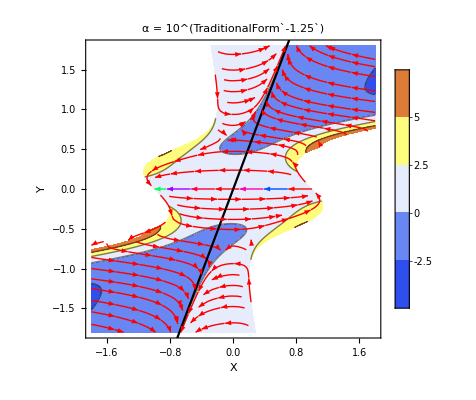
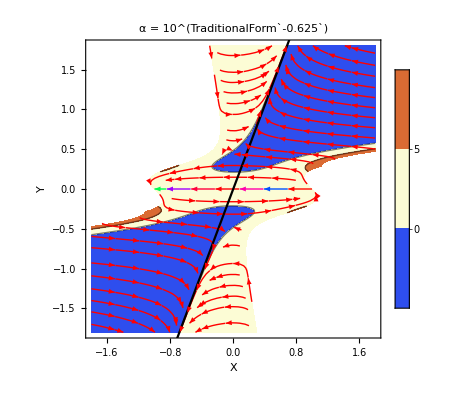
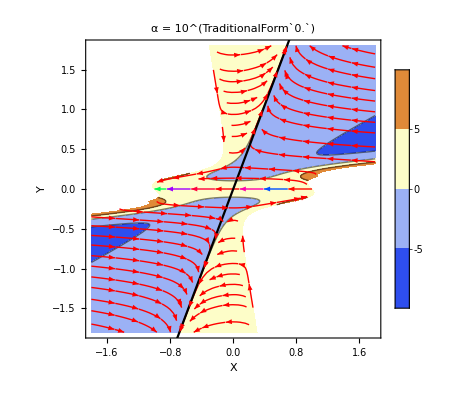
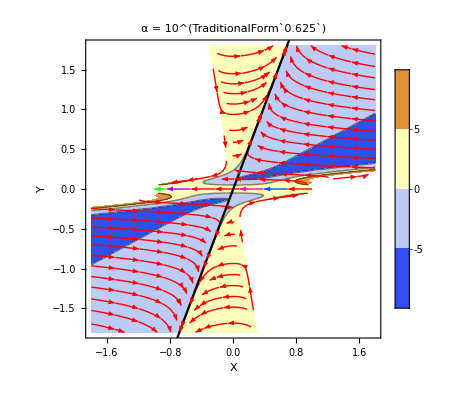

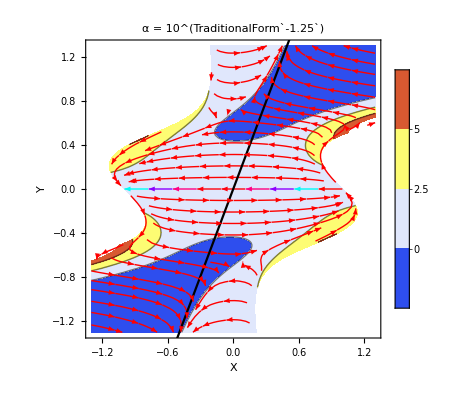
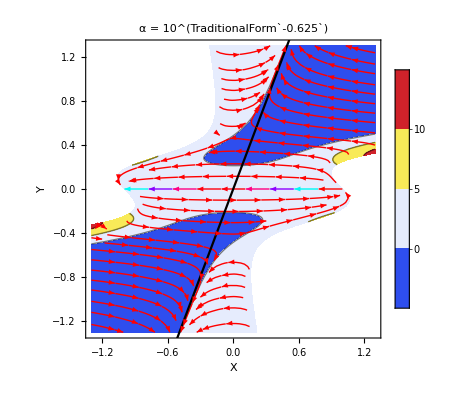
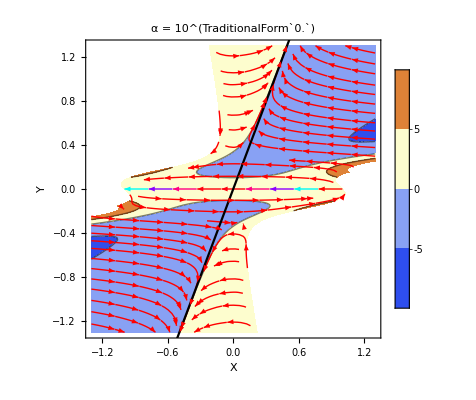
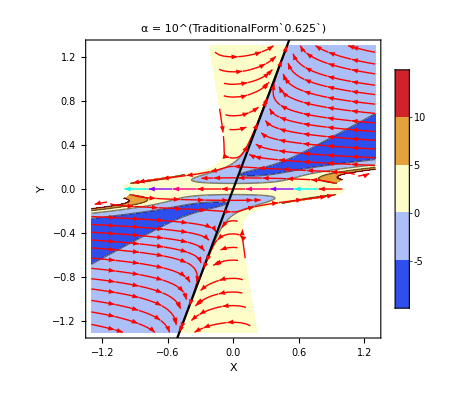

```mathematica
{Subscript[Ω, m],Subscript[Ω, r]}={0,0}; α=10^r; L=1.8; Print[];

Table[Show[{
ContourPlot[ϵxy,{X,-L,L},{Y,-L,L},ColorFunction->"TemperatureMap",PlotLegends->Automatic,RegionFunction->Function[{X,Y},Z4≥0]],
StreamPlot[{Xp//NoMoreFPϵ,X},{X,-L,L},{Y,-L,L},StreamColorFunction->Hue,RegionFunction->Function[{X,Y},Z4≥0]],
Plot[βval X,{X,-L,L},PlotStyle->Black]},
PlotLabel->StringForm["α = 10^(``) ",Round[r,0.001]] ,RotateLabel->False,FrameLabel->{"X","Y"}],{r,-1.25,0.625,0.625}]

L=1.3;
Table[Show[{
ContourPlot[ϵxy,{X,-L,L},{Y,-L,L},ColorFunction->"TemperatureMap",PlotLegends->Automatic,RegionFunction->Function[{X,Y},Z4≥0]],
StreamPlot[{Xp//NoMoreFPϵ,X},{X,-L,L},{Y,-L,L},StreamColorFunction->Hue,RegionFunction->Function[{X,Y},Z4≥0]],
Plot[βval X,{X,-L,L},PlotStyle->Black]},
PlotLabel->StringForm["α = 10^(``) ",Round[r,0.001]] ,RotateLabel->False,FrameLabel->{"X","Y"}],{r,-1.25,0.625,0.625}]

Print[];
```

### Only κ [ β < 0 ]

```mathematica
Clear[ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1],Subscript[Ω, m],Subscript[Ω, r]]; Print[]; aux1={}; aux2={}; NumSum={};NumPrd={}; Den={}; 
{ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]}={1,0,κ,0,0,0,0,0,0,0,0}; t0=AbsoluteTime[];
SolveForThis={κ}; AssumeThis=(κ≠0);

Print[fried==0,"\n",eq1==0,"\n",eq2==0,"\n\n",
"Z^4 = ",Z4=(Zval^4//FullSimplify),"\n","P = ",(Pval//FullSimplify),"\n","ϵ = ",ϵxy=(ϵval//FullSimplify),"\n"]
cons01=Reduce[βval<0&&γval^4>0,Reals,Backsubstitution->True]; 
cons02=Reduce[βval>0&&γval^4>0,Reals,Backsubstitution->True];
consJ0=Reduce[(cons01||cons02)&&AssumeThis,SolveForThis,Reals];Print[
"\n0. Expressions involving β,γ","\n\n   β = ",(βval//FullSimplify)," , γ^4 = ",(γvalAbs^4//Simplify),
"\n\n0.1. Conditions for  [ β < 0 , γ ∈ ℝ ]\n\n   ",cons01,
"\n\n\n0.2. Conditions for  [ β > 0 , γ ∈ ℝ ]\n\n   ",cons02,
"\n\n J0. Joint constraints for  [ ASYMPTOTIC BEHAVIOUR ] (0.1||0.2) \n\n   ",consJ0];

tt=CoefficientList[lambdaSum,OverHat[ψ],{5}]//FullSimplify;
dd=CoefficientList[lambdaPrd,OverHat[ψ],{7}]//FullSimplify;
For[i=1,i≤Length[consT],i++,AppendTo[aux1,((consT[[i]]/.Subscript[t,k_]:>tt[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[aux2,((consD[[i]]/.Subscript[d,k_]:>dd[[k+1]]))//Simplify]];
cons11=Reduce[Apply[Or,aux1],Reals,Backsubstitution->True];
cons12=Reduce[Apply[Or,aux2],Reals,Backsubstitution->True];
consJ1=Reduce[cons11&&cons12&&AssumeThis,SolveForThis,Reals];Print[
"\n\n1. Expressions involving Eigenvalues[ 𝕂 ]","\n\n   λ_+ + λ_- = ",lambdaSum,"\n   λ_+ * λ_- = ",lambdaPrd,
"\n\n\n1.1. Conditions for  [ λ_+ + λ_- > 0 ]\n\n   ",cons11,
"\n\n\n1.2. Conditions for  [ λ_+ * λ_- > 0 ]\n\n   ",cons12,
"\n\n\n J1. Joint constraints for  [ NO-GHOSTS ] (1.1∧1.2) \n\n   ",consJ1,"\n"]

ns=CoefficientList[Numerator[cssum],OverHat[ψ],7]//FullSimplify;
np=CoefficientList[Numerator[csprd],OverHat[ψ],7]//FullSimplify;
dsp=CoefficientList[Denominator[cssum],OverHat[ψ],7]//FullSimplify;
For[i=1,i≤Length[consD],i++,AppendTo[NumSum,((consD[[i]]/.Subscript[d,k_]:>ns[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[NumPrd,((consD[[i]]/.Subscript[d,k_]:>np[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[Den,((consD[[i]]/.Subscript[d,k_]:>dsp[[k+1]]))//Simplify]];
cons21=Reduce[Apply[Or,NumSum]&&AssumeThis,SolveForThis,Reals];
cons22=Reduce[Apply[Or,NumPrd]&&AssumeThis,SolveForThis,Reals];
cons23=Reduce[Apply[Or,Den]&&AssumeThis,SolveForThis,Reals];
consJ2=Reduce[cons21&&cons22&&cons23&&AssumeThis,SolveForThis,Reals];Print[
"\n2. Expressions involving  c_s^2 ","\n\n   c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = ",cssum,"\n   c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 = ",csprd,
"\n\n2.1. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 ] > 0\n\n   ",cons21,
"\n\n\n2.2. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 ] > 0\n\n   ",cons22,
"\n\n\n2.3. Conditions for Denominator > 0\n\n   ",cons23,
"\n\n\n J2. Joint constraints for [ NO-LAPLACIAN INSTABILITIES ] (2.1∧2.2∧2.3) \n\n   ",consJ2,"\n"]

cons31=Reduce[Resolve[ForAll[OverHat[ψ],consJ2&&cs21≤1],Reals]&&AssumeThis,SolveForThis,Reals];
cons32=Reduce[Resolve[ForAll[OverHat[ψ],consJ2&&cs22≤1],Reals]&&AssumeThis,SolveForThis,Reals];
consJ3=Reduce[cons31&&cons32&&AssumeThis,SolveForThis,Reals];
Print["\n3.1 Conditions for 0 < c_(s, SubscriptBox[h, ±])^2 ≤ 1\n\n   ",cons31,"\n\n   c_(s, SubscriptBox[h, ±])^2 = ",Simplify[cs21,cons31],
"\n\n3.2 Conditions for 0 < c_(s, SubscriptBox[γ, ±])^2 ≤ 1\n\n   ",cons32,"\n\n   c_(s, SubscriptBox[γ, ±])^2 = ",Simplify[cs22,cons32],
"\n\n J3. Joint constraints for [ CAUSALITY ] (3.1∧3.2∧J2) \n\n   ",consJ3,"\n"]

consJ4=Reduce[Resolve[ForAll[OverHat[ψ],cs21==1],Reals]&&AssumeThis,SolveForThis,Reals];Print[
"\n 4. Joint constraints for [ GRAVITATIONAL WAVES ] \n\n   ",consJ4,"\n\n   c_(s, SubscriptBox[h, ±])^2 = ",Simplify[cs21,consJ4],"\n\n   c_(s, SubscriptBox[γ, ±])^2 = ",Simplify[cs22,consJ4],"\n"]

Print["\n Summary of CONSTRAINTS (J1∧J2∧J3) \n\n   ",Reduce[consJ1&&consJ2&&consJ3&&AssumeThis,SolveForThis,Reals],"\n"]
Print["\n Summary of CONSTRAINTS (J1∧J2∧J3∧J4) \n\n   ",Reduce[consJ1&&consJ2&&consJ3&&consJ4&&AssumeThis,SolveForThis,Reals],"\n"]

Print["\n\nThis process took about ",Round[(AbsoluteTime[]-t0)/60,0.001]," minutes.\n"];
```

-1+X^2+2 X Y+Y^2+(2 q^2 Z^4)/F^4+(2 X^2 Y^2-20 X Y^3-12 Y^4) κ+Ω_m+Ω_r==0
3+X^2+2 X Y+Y^2+(2 q^2 Z^4)/F^4-2 ϵ+(70 X^2 Y^2+12 √2 P Y^3+108 X Y^3+24 Y^4-4 Y^4 ϵ) κ+Ω_r==0
P/(√2)+3 X+2 Y+(4 q^2 Z^4)/(F^4 Y)-Y ϵ+(2 X^2 Y+√2 P Y^2+6 X Y^2-6 Y^3+10 Y^3 ϵ) κ==0

Z^4 = 1/2 (1-(X+Y)^2+2 Y^2 (-X^2+10 X Y+6 Y^2) κ-Ω_m-Ω_r)
P = (X^2 (4+4 Y^2 κ (1+19 Y^2-168 Y^4 κ))+2 X Y (1-2 Y^2 κ (23-33 Y^2+366 Y^4 κ))+4 (-1+Ω_m+Ω_r)+Y^2 (4-Ω_m+2 Y^2 κ (-42+18 Y^2-216 Y^4 κ+9 Ω_m+4 Ω_r)))/(√2 Y (1+2 Y^2 κ (1-5 Y^2+62 Y^4 κ)))
ϵ = (4-Ω_m+2 Y^2 κ (-20+2 (29 X^2+38 X Y+9 Y^2+2 (X-5 Y) Y^2 (23 X+9 Y) κ)+23 Ω_m+24 Ω_r))/(2+4 Y^2 κ (1-5 Y^2+62 Y^4 κ))

0. Expressions involving β,γ

   β = -23/9 , γ^4 = (180389 κ)/2187

0.1. Conditions for  [ β < 0 , γ ∈ ℝ ]

   κ>0


0.2. Conditions for  [ β > 0 , γ ∈ ℝ ]

   False

 J0. Joint constraints for  [ ASYMPTOTIC BEHAVIOUR ] (0.1||0.2) 

   κ>0

1. Expressions involving Eigenvalues[ 𝕂 ]

   λ_+ + λ_- = 5/4+κ (ψ̂)^2+(19 κ (ψ̂)^4)/8
   λ_+ * λ_- = 1/8 (2+2 κ (ψ̂)^2+19 κ (ψ̂)^4+κ^2 (ψ̂)^6)


1.1. Conditions for  [ λ_+ + λ_- > 0 ]

   κ≥0


1.2. Conditions for  [ λ_+ * λ_- > 0 ]

   κ≥0


 J1. Joint constraints for  [ NO-GHOSTS ] (1.1∧1.2) 

   κ>0

2. Expressions involving  c_s^2 

   c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = (4+4 κ (ψ̂)^2+18 κ (ψ̂)^4+30 κ^2 (ψ̂)^6)/(2+2 κ (ψ̂)^2+19 κ (ψ̂)^4+κ^2 (ψ̂)^6)
   c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 = (2+2 κ (ψ̂)^2-κ (ψ̂)^4-3 κ^2 (ψ̂)^6)/(2+2 κ (ψ̂)^2+19 κ (ψ̂)^4+κ^2 (ψ̂)^6)

2.1. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 ] > 0

   1/20 (-297-63 √21)<κ<1/20 (-297+63 √21)||κ>0


2.2. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 ] > 0

   False


2.3. Conditions for Denominator > 0

   κ>0


 J2. Joint constraints for [ NO-LAPLACIAN INSTABILITIES ] (2.1∧2.2∧2.3) 

   False

3.1 Conditions for 0 < c_(s, SubscriptBox[h, ±])^2 ≤ 1

   False

   c_(s, SubscriptBox[h, ±])^2 = (2+2 κ (ψ̂)^2+9 κ (ψ̂)^4+15 κ^2 (ψ̂)^6-2 κ (ψ̂)^3 √(16+(25+16 κ) (ψ̂)^2+82 κ (ψ̂)^4+57 κ^2 (ψ̂)^6))/(2+2 κ (ψ̂)^2+19 κ (ψ̂)^4+κ^2 (ψ̂)^6)

3.2 Conditions for 0 < c_(s, SubscriptBox[γ, ±])^2 ≤ 1

   False

   c_(s, SubscriptBox[γ, ±])^2 = (2+2 κ (ψ̂)^2+9 κ (ψ̂)^4+15 κ^2 (ψ̂)^6+2 κ (ψ̂)^3 √(16+(25+16 κ) (ψ̂)^2+82 κ (ψ̂)^4+57 κ^2 (ψ̂)^6))/(2+2 κ (ψ̂)^2+19 κ (ψ̂)^4+κ^2 (ψ̂)^6)

 J3. Joint constraints for [ CAUSALITY ] (3.1∧3.2∧J2) 

   False

4. Joint constraints for [ GRAVITATIONAL WAVES ] 

   False

   c_(s, SubscriptBox[h, ±])^2 = (2+2 κ (ψ̂)^2+9 κ (ψ̂)^4+15 κ^2 (ψ̂)^6-2 κ (ψ̂)^3 √(16+(25+16 κ) (ψ̂)^2+82 κ (ψ̂)^4+57 κ^2 (ψ̂)^6))/(2+2 κ (ψ̂)^2+19 κ (ψ̂)^4+κ^2 (ψ̂)^6)

   c_(s, SubscriptBox[γ, ±])^2 = (2+2 κ (ψ̂)^2+9 κ (ψ̂)^4+15 κ^2 (ψ̂)^6+2 κ (ψ̂)^3 √(16+(25+16 κ) (ψ̂)^2+82 κ (ψ̂)^4+57 κ^2 (ψ̂)^6))/(2+2 κ (ψ̂)^2+19 κ (ψ̂)^4+κ^2 (ψ̂)^6)

Summary of CONSTRAINTS (J1∧J2∧J3) 

   False

Summary of CONSTRAINTS (J1∧J2∧J3∧J4) 

   False

This process took about 0.045 minutes.

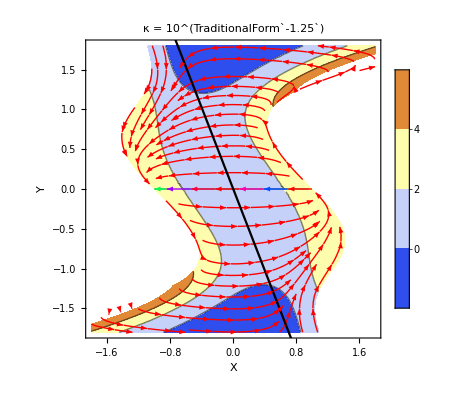
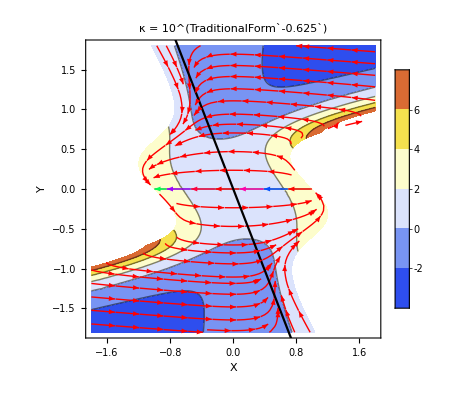
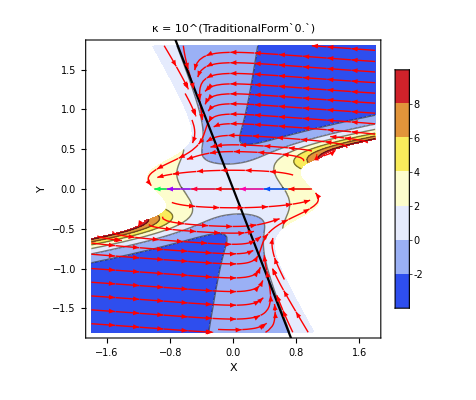
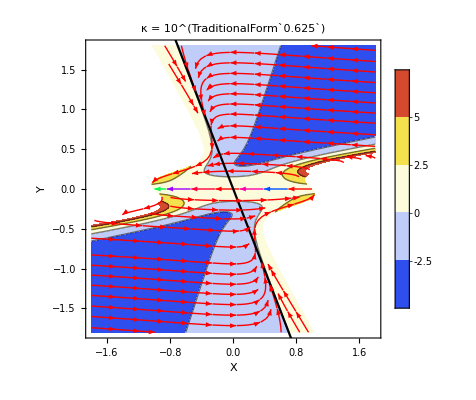

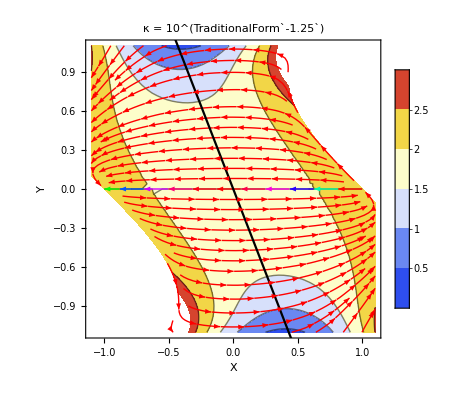
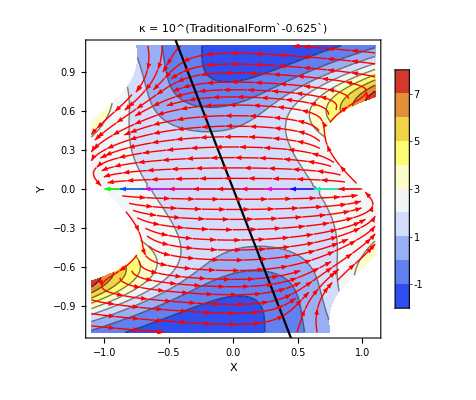
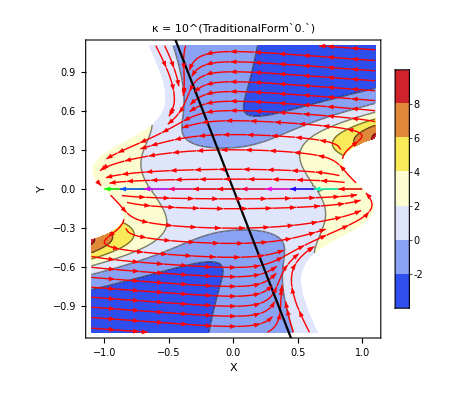
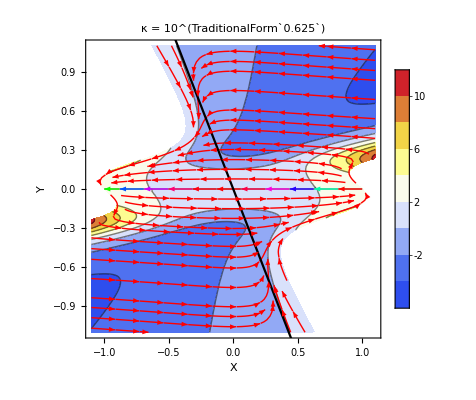

```mathematica
{Subscript[Ω, m],Subscript[Ω, r]}={0,0}; κ=10^r; L=1.8; Print[];

Table[Show[{
ContourPlot[ϵxy,{X,-L,L},{Y,-L,L},ColorFunction->"TemperatureMap",PlotLegends->Automatic,RegionFunction->Function[{X,Y},Z4≥0]],
StreamPlot[{Xp//NoMoreFPϵ,X},{X,-L,L},{Y,-L,L},StreamColorFunction->Hue,RegionFunction->Function[{X,Y},Z4≥0]],
Plot[βval X,{X,-L,L},PlotStyle->Black]},
PlotLabel->StringForm["κ = 10^(``)",Round[r,0.001]] ,RotateLabel->False,FrameLabel->{"X","Y"}],{r,-1.25,0.625,0.625}]

L=1.1;
Table[Show[{
ContourPlot[ϵxy,{X,-L,L},{Y,-L,L},ColorFunction->"TemperatureMap",PlotLegends->Automatic,RegionFunction->Function[{X,Y},Z4≥0]],
StreamPlot[{Xp//NoMoreFPϵ,X},{X,-L,L},{Y,-L,L},StreamColorFunction->Hue,RegionFunction->Function[{X,Y},Z4≥0]],
Plot[βval X,{X,-L,L},PlotStyle->Black]},
PlotLabel->StringForm["κ = 10^(``)",Round[r,0.001]] ,RotateLabel->False,FrameLabel->{"X","Y"}],{r,-1.25,0.625,0.625}]

Print[];
```

### Only λ [ Takes part in: speed-of-sound constraints | Not in: Background, Asymptotic behaviour ] - Cannot have a phase diagram on its own.

```mathematica
Clear[ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1],Subscript[Ω, m],Subscript[Ω, r]]; Print[]; aux1={}; aux2={}; NumSum={};NumPrd={}; Den={}; 
{ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]}={1,0,0,λ,0,0,0,0,0,0,0}; t0=AbsoluteTime[];
SolveForThis={λ}; AssumeThis=(λ≠0);

Print[" J0. It doesn't take part in [ BACKGROUND ] equations or  [ ASYMPTOTIC BEHAVIOUR ] conditions (0.1||0.2) "]
Print[" J1. It doesn't take part in  [ NO-GHOSTS ] conditions \n"]

ns=CoefficientList[Numerator[cssum],OverHat[ψ],7]//FullSimplify;
np=CoefficientList[Numerator[csprd],OverHat[ψ],7]//FullSimplify;
dsp=CoefficientList[Denominator[cssum],OverHat[ψ],7]//FullSimplify;
For[i=1,i≤Length[consD],i++,AppendTo[NumSum,((consD[[i]]/.Subscript[d,k_]:>ns[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[NumPrd,((consD[[i]]/.Subscript[d,k_]:>np[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[Den,((consD[[i]]/.Subscript[d,k_]:>dsp[[k+1]]))//Simplify]];
cons21=Reduce[Apply[Or,NumSum]&&AssumeThis,SolveForThis,Reals];
cons22=Reduce[Apply[Or,NumPrd]&&AssumeThis,SolveForThis,Reals];
cons23=Reduce[Apply[Or,Den]&&AssumeThis,SolveForThis,Reals];
consJ2=Reduce[cons21&&cons22&&cons23&&AssumeThis,SolveForThis,Reals];Print[
"\n2. Expressions involving  c_s^2 ","\n\n   c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = ",cssum,"\n   c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 = ",csprd,
"\n\n2.1. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 ] > 0\n\n   ",cons21,
"\n\n\n2.2. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 ] > 0\n\n   ",cons22,
"\n\n\n2.3. Conditions for Denominator > 0\n\n   ",cons23,
"\n\n\n J2. Joint constraints for [ NO-LAPLACIAN INSTABILITIES ] (2.1∧2.2∧2.3) \n\n   ",consJ2,"\n"]

cons31=Reduce[Resolve[ForAll[OverHat[ψ],consJ2&&cs21≤1],Reals]&&AssumeThis,SolveForThis,Reals];
cons32=Reduce[Resolve[ForAll[OverHat[ψ],consJ2&&cs22≤1],Reals]&&AssumeThis,SolveForThis,Reals];
consJ3=Reduce[cons31&&cons32&&AssumeThis,SolveForThis,Reals];
Print["\n3.1 Conditions for 0 < c_(s, SubscriptBox[h, ±])^2 ≤ 1\n\n   ",cons31,"\n\n   c_(s, SubscriptBox[h, ±])^2 = ",Simplify[cs21,cons31],
"\n\n3.2 Conditions for 0 < c_(s, SubscriptBox[γ, ±])^2 ≤ 1\n\n   ",cons32,"\n\n   c_(s, SubscriptBox[γ, ±])^2 = ",Simplify[cs22,cons32],
"\n\n J3. Joint constraints for [ CAUSALITY ] (3.1∧3.2∧J2) \n\n   ",consJ3,"\n"]

consJ4=Reduce[Resolve[ForAll[OverHat[ψ],cs21==1],Reals]&&AssumeThis,SolveForThis,Reals];Print[
"\n 4. Joint constraints for [ GRAVITATIONAL WAVES ] \n\n   ",consJ4,"\n\n   c_(s, SubscriptBox[h, ±])^2 = ",Simplify[cs21,consJ4],"\n\n   c_(s, SubscriptBox[γ, ±])^2 = ",Simplify[cs22,consJ4],"\n"]

Print["\n Summary of CONSTRAINTS (J1∧J2∧J3) \n\n   ",Reduce[consJ2&&consJ3&&AssumeThis,SolveForThis,Reals],"\n"]
Print["\n Summary of CONSTRAINTS (J1∧J2∧J3∧J4) \n\n   ",Reduce[consJ2&&consJ3&&consJ4&&AssumeThis,SolveForThis,Reals],"\n"]

Print["\n\nThis process took about ",Round[(AbsoluteTime[]-t0)/60,0.001]," minutes.\n"];
```

J0. It doesn't take part in [ BACKGROUND ] equations or  [ ASYMPTOTIC BEHAVIOUR ] conditions (0.1||0.2)

J1. It doesn't take part in  [ NO-GHOSTS ] conditions

2. Expressions involving  c_s^2 

   c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = 1/2 (4+8 λ^2 (ψ̂)^6)
   c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 = 1

2.1. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 ] > 0

   λ<0||λ>0


2.2. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 ] > 0

   λ<0||λ>0


2.3. Conditions for Denominator > 0

   λ<0||λ>0


 J2. Joint constraints for [ NO-LAPLACIAN INSTABILITIES ] (2.1∧2.2∧2.3) 

   λ<0||λ>0

3.1 Conditions for 0 < c_(s, SubscriptBox[h, ±])^2 ≤ 1

   λ<0||λ>0

   c_(s, SubscriptBox[h, ±])^2 = 1+2 λ^2 (ψ̂)^6-2 Abs[λ] Abs[ψ̂]^3 √(1+λ^2 (ψ̂)^6)

3.2 Conditions for 0 < c_(s, SubscriptBox[γ, ±])^2 ≤ 1

   False

   c_(s, SubscriptBox[γ, ±])^2 = 1+2 λ^2 (ψ̂)^6+2 λ (ψ̂)^3 √(1+λ^2 (ψ̂)^6)

 J3. Joint constraints for [ CAUSALITY ] (3.1∧3.2∧J2) 

   False

4. Joint constraints for [ GRAVITATIONAL WAVES ] 

   False

   c_(s, SubscriptBox[h, ±])^2 = 1+2 λ^2 (ψ̂)^6+2 λ (ψ̂)^3 √(1+λ^2 (ψ̂)^6)

   c_(s, SubscriptBox[γ, ±])^2 = 1+2 λ^2 (ψ̂)^6+2 λ (ψ̂)^3 √(1+λ^2 (ψ̂)^6)

Summary of CONSTRAINTS (J1∧J2∧J3) 

   False

Summary of CONSTRAINTS (J1∧J2∧J3∧J4) 

   False

This process took about 0.012 minutes.

### Only θ_4 [ β > 0 ]

```mathematica
Clear[ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1],Subscript[Ω, m],Subscript[Ω, r]]; Print[]; aux1={}; aux2={}; NumSum={};NumPrd={}; Den={}; 
{ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]}={1,0,0,0,Subscript[θ, 4],0,0,0,0,0,0}; t0=AbsoluteTime[];
SolveForThis={Subscript[θ, 4]}; AssumeThis=(Subscript[θ, 4]≠0);

Print[fried==0,"\n",eq1==0,"\n",eq2==0,"\n\n",
"Z^4 = ",Z4=(Zval^4//FullSimplify),"\n","P = ",(Pval//FullSimplify),"\n","ϵ = ",ϵxy=(ϵval//FullSimplify),"\n"]
cons01=Reduce[βval<0&&γval^4>0,Reals,Backsubstitution->True]; 
cons02=Reduce[βval>0&&γval^4>0,Reals,Backsubstitution->True];
consJ0=Reduce[(cons01||cons02)&&AssumeThis,SolveForThis,Reals];Print[
"\n0. Expressions involving β,γ","\n\n   β = ",(βval//FullSimplify)," , γ^4 = ",(γvalAbs^4//Simplify),
"\n\n0.1. Conditions for  [ β < 0 , γ ∈ ℝ ]\n\n   ",cons01,
"\n\n\n0.2. Conditions for  [ β > 0 , γ ∈ ℝ ]\n\n   ",cons02,
"\n\n J0. Joint constraints for  [ ASYMPTOTIC BEHAVIOUR ] (0.1||0.2) \n\n   ",consJ0];

tt=CoefficientList[lambdaSum,OverHat[ψ],{5}]//FullSimplify;
dd=CoefficientList[lambdaPrd,OverHat[ψ],{7}]//FullSimplify;
For[i=1,i≤Length[consT],i++,AppendTo[aux1,((consT[[i]]/.Subscript[t,k_]:>tt[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[aux2,((consD[[i]]/.Subscript[d,k_]:>dd[[k+1]]))//Simplify]];
cons11=Reduce[Apply[Or,aux1],Reals,Backsubstitution->True];
cons12=Reduce[Apply[Or,aux2],Reals,Backsubstitution->True];
consJ1=Reduce[cons11&&cons12&&AssumeThis,SolveForThis,Reals];Print[
"\n\n1. Expressions involving Eigenvalues[ 𝕂 ]","\n\n   λ_+ + λ_- = ",lambdaSum,"\n   λ_+ * λ_- = ",lambdaPrd,
"\n\n\n1.1. Conditions for  [ λ_+ + λ_- > 0 ]\n\n   ",cons11,
"\n\n\n1.2. Conditions for  [ λ_+ * λ_- > 0 ]\n\n   ",cons12,
"\n\n\n J1. Joint constraints for  [ NO-GHOSTS ] (1.1∧1.2) \n\n   ",consJ1,"\n"]

ns=CoefficientList[Numerator[cssum],OverHat[ψ],7]//FullSimplify;
np=CoefficientList[Numerator[csprd],OverHat[ψ],7]//FullSimplify;
dsp=CoefficientList[Denominator[cssum],OverHat[ψ],7]//FullSimplify;
For[i=1,i≤Length[consD],i++,AppendTo[NumSum,((consD[[i]]/.Subscript[d,k_]:>ns[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[NumPrd,((consD[[i]]/.Subscript[d,k_]:>np[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[Den,((consD[[i]]/.Subscript[d,k_]:>dsp[[k+1]]))//Simplify]];
cons21=Reduce[Apply[Or,NumSum]&&AssumeThis,SolveForThis,Reals];
cons22=Reduce[Apply[Or,NumPrd]&&AssumeThis,SolveForThis,Reals];
cons23=Reduce[Apply[Or,Den]&&AssumeThis,SolveForThis,Reals];
consJ2=Reduce[cons21&&cons22&&cons23&&AssumeThis,SolveForThis,Reals];Print[
"\n2. Expressions involving  c_s^2 ","\n\n   c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = ",cssum,"\n   c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 = ",csprd,
"\n\n2.1. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 ] > 0\n\n   ",cons21,
"\n\n\n2.2. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 ] > 0\n\n   ",cons22,
"\n\n\n2.3. Conditions for Denominator > 0\n\n   ",cons23,
"\n\n\n J2. Joint constraints for [ NO-LAPLACIAN INSTABILITIES ] (2.1∧2.2∧2.3) \n\n   ",consJ2,"\n"]

cons31=Reduce[Resolve[ForAll[OverHat[ψ],consJ2&&cs21≤1],Reals]&&AssumeThis,SolveForThis,Reals];
cons32=Reduce[Resolve[ForAll[OverHat[ψ],consJ2&&cs22≤1],Reals]&&AssumeThis,SolveForThis,Reals];
consJ3=Reduce[cons31&&cons32&&AssumeThis,SolveForThis,Reals,Backsubstitution->True];
Print["\n3.1 Conditions for 0 < c_(s, SubscriptBox[h, ±])^2 ≤ 1\n\n   ",cons31,"\n\n   c_(s, SubscriptBox[h, ±])^2 = ",Simplify[cs21,cons31],
"\n\n3.2 Conditions for 0 < c_(s, SubscriptBox[γ, ±])^2 ≤ 1\n\n   ",cons32,"\n\n   c_(s, SubscriptBox[γ, ±])^2 = ",Simplify[cs22,cons32],
"\n\n J3. Joint constraints for [ CAUSALITY ] (3.1∧3.2∧J2) \n\n   ",consJ3,"\n"]

consJ4=Reduce[Resolve[ForAll[OverHat[ψ],cs21==1],Reals]&&AssumeThis,SolveForThis,Reals];Print[
"\n 4. Joint constraints for [ GRAVITATIONAL WAVES ] \n\n   ",consJ4,"\n\n   c_(s, SubscriptBox[h, ±])^2 = ",Simplify[cs21,consJ4],"\n\n   c_(s, SubscriptBox[γ, ±])^2 = ",Simplify[cs22,consJ4],"\n"]

Print["\n Summary of CONSTRAINTS (J1∧J2∧J3) \n\n   ",Reduce[consJ1&&consJ2&&consJ3&&AssumeThis,SolveForThis,Reals],"\n"]
Print["\n Summary of CONSTRAINTS (J1∧J2∧J3∧J4) \n\n   ",Reduce[consJ1&&consJ2&&consJ3&&consJ4&&AssumeThis,SolveForThis,Reals],"\n"]

Print["\n\nThis process took about ",Round[(AbsoluteTime[]-t0)/60,0.001]," minutes.\n"];
```

-1+X^2+2 X Y+Y^2+(2 q^2 Z^4)/F^4+(-64 X Y^3-32 Y^4) θ_4+Ω_m+Ω_r==0
3+X^2+2 X Y+Y^2+(2 q^2 Z^4)/F^4-2 ϵ+(192 X^2 Y^2+32 √2 P Y^3+256 X Y^3+32 Y^4) θ_4+Ω_r==0
P/(√2)+3 X+2 Y+(4 q^2 Z^4)/(F^4 Y)-Y ϵ+(-32 Y^3+32 Y^3 ϵ) θ_4==0

Z^4 = 1/2 (1-(X+Y)^2+32 Y^3 (2 X+Y) θ_4-Ω_m-Ω_r)
P = -(4 X^2+X (2 Y-256 Y^3 θ_4)-Y^2 (-1+32 Y^2 θ_4) (4+64 Y^2 (3 X^2+5 X Y+Y^2) θ_4-Ω_m)+4 (-1-16 Y^4 θ_4+Ω_m+Ω_r))/(√2 Y (-1+32 Y^4 θ_4 (1-32 Y^2 θ_4)))
ϵ = (4-Ω_m+64 Y^2 θ_4 (5 X^2+6 X Y+Y^2-32 Y^3 (4 X+Y) θ_4+2 (-1+Ω_m+Ω_r)))/(2+64 Y^4 θ_4 (-1+32 Y^2 θ_4))

0. Expressions involving β,γ

   β = -4 , γ^4 = 2048 θ_4

0.1. Conditions for  [ β < 0 , γ ∈ ℝ ]

   θ_4>0


0.2. Conditions for  [ β > 0 , γ ∈ ℝ ]

   False

 J0. Joint constraints for  [ ASYMPTOTIC BEHAVIOUR ] (0.1||0.2) 

   θ_4>0

1. Expressions involving Eigenvalues[ 𝕂 ]

   λ_+ + λ_- = 5/4-2 θ_4 (ψ̂)^4
   λ_+ * λ_- = 1/8 (2-16 θ_4 (ψ̂)^4-128 θ_4^2 (ψ̂)^6)


1.1. Conditions for  [ λ_+ + λ_- > 0 ]

   θ_4≤0


1.2. Conditions for  [ λ_+ * λ_- > 0 ]

   θ_4==0


 J1. Joint constraints for  [ NO-GHOSTS ] (1.1∧1.2) 

   False

2. Expressions involving  c_s^2 

   c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = (4-16 θ_4 (ψ̂)^4)/(2-16 θ_4 (ψ̂)^4-128 θ_4^2 (ψ̂)^6)
   c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 = 2/(2-16 θ_4 (ψ̂)^4-128 θ_4^2 (ψ̂)^6)

2.1. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 ] > 0

   θ_4<0


2.2. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 ] > 0

   θ_4<0||θ_4>0


2.3. Conditions for Denominator > 0

   False


 J2. Joint constraints for [ NO-LAPLACIAN INSTABILITIES ] (2.1∧2.2∧2.3) 

   False

3.1 Conditions for 0 < c_(s, SubscriptBox[h, ±])^2 ≤ 1

   False

   c_(s, SubscriptBox[h, ±])^2 = (-1+4 θ_4 (ψ̂)^4+4 θ_4 (ψ̂)^3 √(4+(ψ̂)^2))/(-1+8 θ_4 (ψ̂)^4+64 θ_4^2 (ψ̂)^6)

3.2 Conditions for 0 < c_(s, SubscriptBox[γ, ±])^2 ≤ 1

   False

   c_(s, SubscriptBox[γ, ±])^2 = (-1+4 θ_4 (ψ̂)^4+4 θ_4 (ψ̂)^3 √(4+(ψ̂)^2))/(-1+8 θ_4 (ψ̂)^4+64 θ_4^2 (ψ̂)^6)

 J3. Joint constraints for [ CAUSALITY ] (3.1∧3.2∧J2) 

   False

4. Joint constraints for [ GRAVITATIONAL WAVES ] 

   False

   c_(s, SubscriptBox[h, ±])^2 = (-1+4 θ_4 (ψ̂)^4+4 θ_4 (ψ̂)^3 √(4+(ψ̂)^2))/(-1+8 θ_4 (ψ̂)^4+64 θ_4^2 (ψ̂)^6)

   c_(s, SubscriptBox[γ, ±])^2 = (-1+4 θ_4 (ψ̂)^4+4 θ_4 (ψ̂)^3 √(4+(ψ̂)^2))/(-1+8 θ_4 (ψ̂)^4+64 θ_4^2 (ψ̂)^6)

Summary of CONSTRAINTS (J1∧J2∧J3) 

   False

Summary of CONSTRAINTS (J1∧J2∧J3∧J4) 

   False

This process took about 0.038 minutes.

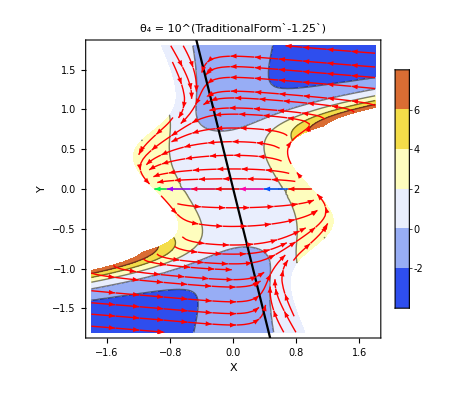
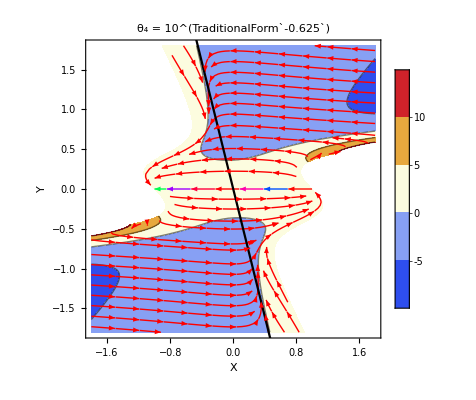
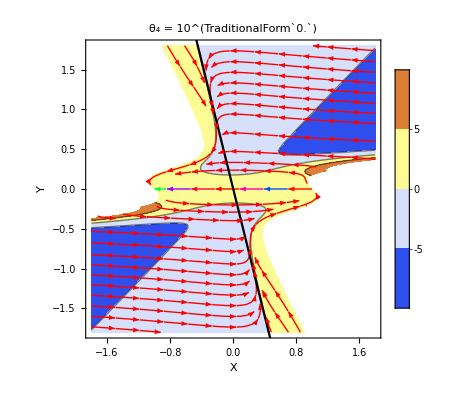
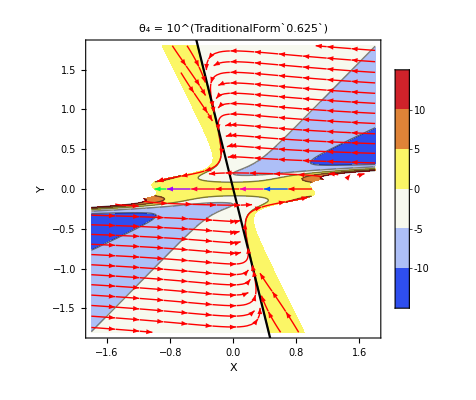

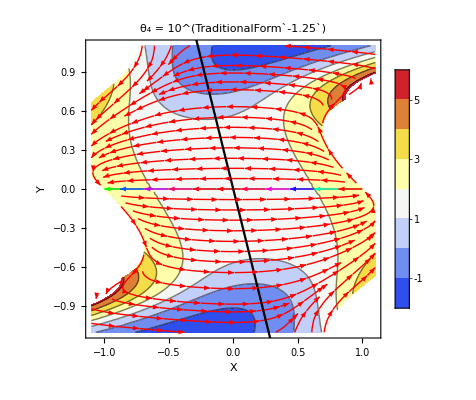
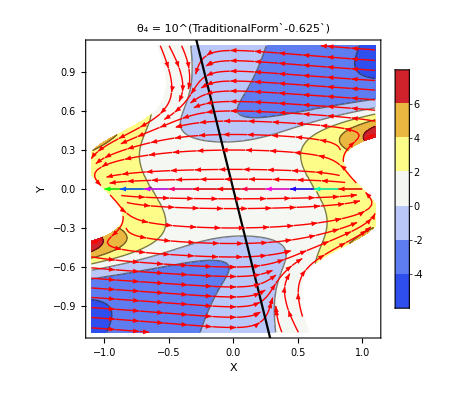
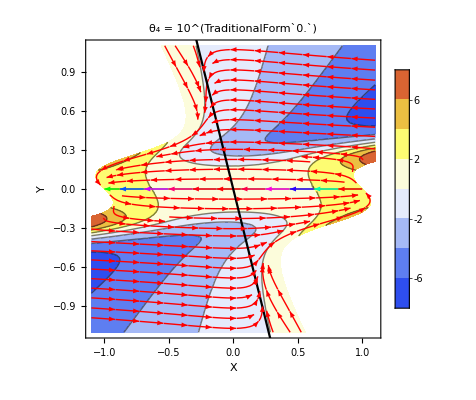
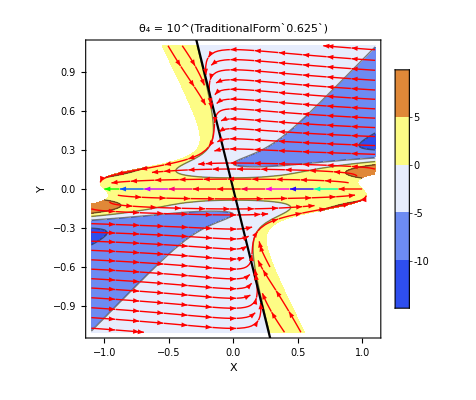

```mathematica
{Subscript[Ω, m],Subscript[Ω, r]}={0,0}; Subscript[θ, 4]=10^r; L=1.8; Print[];

Table[Show[{
ContourPlot[ϵxy,{X,-L,L},{Y,-L,L},ColorFunction->"TemperatureMap",PlotLegends->Automatic,RegionFunction->Function[{X,Y},Z4≥0]],
StreamPlot[{Xp//NoMoreFPϵ,X},{X,-L,L},{Y,-L,L},StreamColorFunction->Hue,RegionFunction->Function[{X,Y},Z4≥0]],
Plot[βval X,{X,-L,L},PlotStyle->Black]},
PlotLabel->StringForm["θ_4 = 10^(``)",Round[r,0.001]] ,RotateLabel->False,FrameLabel->{"X","Y"}],{r,-1.25,0.625,0.625}]

L=1.1;
Table[Show[{
ContourPlot[ϵxy,{X,-L,L},{Y,-L,L},ColorFunction->"TemperatureMap",PlotLegends->Automatic,RegionFunction->Function[{X,Y},Z4≥0]],
StreamPlot[{Xp//NoMoreFPϵ,X},{X,-L,L},{Y,-L,L},StreamColorFunction->Hue,RegionFunction->Function[{X,Y},Z4≥0]],
Plot[βval X,{X,-L,L},PlotStyle->Black]},
PlotLabel->StringForm["θ_4 = 10^(``)",Round[r,0.001]] ,RotateLabel->False,FrameLabel->{"X","Y"}],{r,-1.25,0.625,0.625}]

Print[];
```

### Only χ_3, χ_4 [ Takes part in: speed-of-sound constraints | Not in: Asymptotic behaviour ] - Cannot have a phase diagram on its own.

```mathematica
Clear[ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1],Subscript[Ω, m],Subscript[Ω, r]]; Print[]; aux1={}; aux2={}; NumSum={};NumPrd={}; Den={}; 
{ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]}={1,0,0,0,0,0,0,Subscript[χ, 3],Subscript[χ, 3]+Subscript[χ, 4],Subscript[χ, 4],0}; t0=AbsoluteTime[];
SolveForThis={Subscript[χ, 3],Subscript[χ, 4]}; AssumeThis=(True);

Print[" J0. It doesn't take part in  [ ASYMPTOTIC BEHAVIOUR ] conditions (0.1||0.2) "];

tt=CoefficientList[lambdaSum,OverHat[ψ],{5}]//FullSimplify;
dd=CoefficientList[lambdaPrd,OverHat[ψ],{7}]//FullSimplify;
For[i=1,i≤Length[consT],i++,AppendTo[aux1,((consT[[i]]/.Subscript[t,k_]:>tt[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[aux2,((consD[[i]]/.Subscript[d,k_]:>dd[[k+1]]))//Simplify]];
cons11=Reduce[Apply[Or,aux1],Reals,Backsubstitution->True];
cons12=Reduce[Apply[Or,aux2],Reals,Backsubstitution->True];
consJ1=Reduce[cons11&&cons12&&AssumeThis,SolveForThis,Reals];Print[
"\n\n1. Expressions involving Eigenvalues[ 𝕂 ]","\n\n   λ_+ + λ_- = ",lambdaSum,"\n   λ_+ * λ_- = ",lambdaPrd,
"\n\n\n1.1. Conditions for  [ λ_+ + λ_- > 0 ]\n\n   ",cons11,
"\n\n\n1.2. Conditions for  [ λ_+ * λ_- > 0 ]\n\n   ",cons12,
"\n\n\n J1. Joint constraints for  [ NO-GHOSTS ] (1.1∧1.2) \n\n   ",consJ1,"\n"]

ns=CoefficientList[Numerator[cssum],OverHat[ψ],7]//FullSimplify;
np=CoefficientList[Numerator[csprd],OverHat[ψ],7]//FullSimplify;
dsp=CoefficientList[Denominator[cssum],OverHat[ψ],7]//FullSimplify;
For[i=1,i≤Length[consD],i++,AppendTo[NumSum,((consD[[i]]/.Subscript[d,k_]:>ns[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[NumPrd,((consD[[i]]/.Subscript[d,k_]:>np[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[Den,((consD[[i]]/.Subscript[d,k_]:>dsp[[k+1]]))//Simplify]];
cons21=Reduce[Apply[Or,NumSum]&&AssumeThis,SolveForThis,Reals];
cons22=Reduce[Apply[Or,NumPrd]&&AssumeThis,SolveForThis,Reals];
cons23=Reduce[Apply[Or,Den]&&AssumeThis,SolveForThis,Reals];
consJ2=Reduce[cons21&&cons22&&cons23&&AssumeThis,SolveForThis,Reals];Print[
"\n2. Expressions involving  c_s^2 ","\n\n   c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = ",cssum,"\n   c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 = ",csprd,
"\n\n2.1. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 ] > 0\n\n   ",cons21,
"\n\n\n2.2. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 ] > 0\n\n   ",cons22,
"\n\n\n2.3. Conditions for Denominator > 0\n\n   ",cons23,
"\n\n\n J2. Joint constraints for [ NO-LAPLACIAN INSTABILITIES ] (2.1∧2.2∧2.3) \n\n   ",consJ2,"\n"]

cons31=Reduce[Resolve[ForAll[OverHat[ψ],consJ2&&cs21≤1],Reals]&&AssumeThis,SolveForThis,Reals];
cons32=Reduce[Resolve[ForAll[OverHat[ψ],consJ2&&cs22≤1],Reals]&&AssumeThis,SolveForThis,Reals];
consJ3=Reduce[cons31&&cons32&&AssumeThis,SolveForThis,Reals];
Print["\n3.1 Conditions for 0 < c_(s, SubscriptBox[h, ±])^2 ≤ 1\n\n   ",cons31,"\n\n   c_(s, SubscriptBox[h, ±])^2 = ",Simplify[cs21,cons31],
"\n\n3.2 Conditions for 0 < c_(s, SubscriptBox[γ, ±])^2 ≤ 1\n\n   ",cons32,"\n\n   c_(s, SubscriptBox[γ, ±])^2 = ",Simplify[cs22,cons32],
"\n\n J3. Joint constraints for [ CAUSALITY ] (3.1∧3.2∧J2) \n\n   ",consJ3,"\n"]

consJ4=Reduce[Resolve[ForAll[OverHat[ψ],cs21==1],Reals]&&AssumeThis,SolveForThis,Reals,Backsubstitution->True];Print[
"\n 4. Joint constraints for [ GRAVITATIONAL WAVES ] \n\n   ",consJ4,"\n\n   c_(s, SubscriptBox[h, ±])^2 = ",Simplify[cs21,consJ4],"\n\n   c_(s, SubscriptBox[γ, ±])^2 = ",Simplify[cs22,consJ4],"\n"]

Print["\n Summary of CONSTRAINTS (J1∧J2∧J3) \n\n   ",Reduce[consJ1&&consJ2&&consJ3&&AssumeThis,SolveForThis,Reals],"\n"]
Print["\n Summary of CONSTRAINTS (J1∧J2∧J3∧J4) \n\n   ",Reduce[consJ1&&consJ2&&consJ3&&consJ4&&AssumeThis,SolveForThis,Reals],"\n"]

Clear[α,ξ,κ,λ,Subscript[θ, 1],Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4]];
Print["\n\nThis process took about ",Round[(AbsoluteTime[]-t0)/60,0.001]," minutes.\n"];
```

J0. It doesn't take part in  [ ASYMPTOTIC BEHAVIOUR ] conditions (0.1||0.2)

1. Expressions involving Eigenvalues[ 𝕂 ]

   λ_+ + λ_- = 5/4-2 (χ_3+χ_4) (ψ̂)^2
   λ_+ * λ_- = 1/8 (2-4 (χ_3+χ_4) (ψ̂)^2)


1.1. Conditions for  [ λ_+ + λ_- > 0 ]

   χ_3≤-χ_4


1.2. Conditions for  [ λ_+ * λ_- > 0 ]

   χ_3≤-χ_4


 J1. Joint constraints for  [ NO-GHOSTS ] (1.1∧1.2) 

   χ_4≤-χ_3

2. Expressions involving  c_s^2 

   c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = (4+4 (χ_4-3 (χ_3+χ_4)) (ψ̂)^2)/(2-4 (χ_3+χ_4) (ψ̂)^2)
   c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 = (2+2 (2 χ_4-4 (χ_3+χ_4)) (ψ̂)^2)/(2-4 (χ_3+χ_4) (ψ̂)^2)

2.1. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 ] > 0

   χ_4≤-(3 χ_3)/2


2.2. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 ] > 0

   χ_4≤-2 χ_3


2.3. Conditions for Denominator > 0

   χ_4≤-χ_3


 J2. Joint constraints for [ NO-LAPLACIAN INSTABILITIES ] (2.1∧2.2∧2.3) 

   (χ_3≤0&&χ_4≤-χ_3)||(χ_3>0&&χ_4≤-2 χ_3)

3.1 Conditions for 0 < c_(s, SubscriptBox[h, ±])^2 ≤ 1

   (χ_3≤0&&χ_4≤-χ_3)||(χ_3>0&&χ_4≤-2 χ_3)

   c_(s, SubscriptBox[h, ±])^2 = (-1+(3 χ_3+2 χ_4+Abs[χ_3]) (ψ̂)^2)/(-1+2 (χ_3+χ_4) (ψ̂)^2)

3.2 Conditions for 0 < c_(s, SubscriptBox[γ, ±])^2 ≤ 1

   χ_3≥0&&χ_4≤-2 χ_3

   c_(s, SubscriptBox[γ, ±])^2 = 1

 J3. Joint constraints for [ CAUSALITY ] (3.1∧3.2∧J2) 

   χ_3≥0&&χ_4≤-2 χ_3

4. Joint constraints for [ GRAVITATIONAL WAVES ] 

   χ_3≤0&&χ_4≤-χ_3

   c_(s, SubscriptBox[h, ±])^2 = 1

   c_(s, SubscriptBox[γ, ±])^2 = (-1+2 (2 χ_3+χ_4) (ψ̂)^2)/(-1+2 (χ_3+χ_4) (ψ̂)^2)

Summary of CONSTRAINTS (J1∧J2∧J3) 

   χ_3≥0&&χ_4≤-2 χ_3

Summary of CONSTRAINTS (J1∧J2∧J3∧J4) 

   χ_3==0&&χ_4≤0

This process took about 0.004 minutes.

### Only θ_1 [ Takes part in: ghosts, speed-of-sound constraints | Not in: Asymptotic behaviour ] - Cannot have a phase diagram on its own.

```mathematica
Clear[ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1],Subscript[Ω, m],Subscript[Ω, r]]; Print[]; aux1={}; aux2={}; NumSum={};NumPrd={}; Den={}; 
{ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]}={1,0,0,0,0,0,0,0,0,0,Subscript[θ, 1]}; t0=AbsoluteTime[];
SolveForThis={Subscript[θ, 1]}; AssumeThis=(Subscript[θ, 1]≠0);

Print[" J0. It doesn't take part in [ ASYMPTOTIC BEHAVIOUR ] conditions (0.1||0.2) "]

tt=CoefficientList[lambdaSum,OverHat[ψ],{5}]//FullSimplify;
dd=CoefficientList[lambdaPrd,OverHat[ψ],{7}]//FullSimplify;
For[i=1,i≤Length[consT],i++,AppendTo[aux1,((consT[[i]]/.Subscript[t,k_]:>tt[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[aux2,((consD[[i]]/.Subscript[d,k_]:>dd[[k+1]]))//Simplify]];
cons11=Reduce[Apply[Or,aux1],Reals,Backsubstitution->True];
cons12=Reduce[Apply[Or,aux2],Reals,Backsubstitution->True];
consJ1=Reduce[cons11&&cons12&&AssumeThis,SolveForThis,Reals];Print[
"\n\n1. Expressions involving Eigenvalues[ 𝕂 ]","\n\n   λ_+ + λ_- = ",lambdaSum,"\n   λ_+ * λ_- = ",lambdaPrd,
"\n\n\n1.1. Conditions for  [ λ_+ + λ_- > 0 ]\n\n   ",cons11,
"\n\n\n1.2. Conditions for  [ λ_+ * λ_- > 0 ]\n\n   ",cons12,
"\n\n\n J1. Joint constraints for  [ NO-GHOSTS ] (1.1∧1.2) \n\n   ",consJ1,"\n"]

ns=CoefficientList[Numerator[cssum],OverHat[ψ],7]//FullSimplify;
np=CoefficientList[Numerator[csprd],OverHat[ψ],7]//FullSimplify;
dsp=CoefficientList[Denominator[cssum],OverHat[ψ],7]//FullSimplify;
For[i=1,i≤Length[consD],i++,AppendTo[NumSum,((consD[[i]]/.Subscript[d,k_]:>ns[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[NumPrd,((consD[[i]]/.Subscript[d,k_]:>np[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[Den,((consD[[i]]/.Subscript[d,k_]:>dsp[[k+1]]))//Simplify]];
cons21=Reduce[Apply[Or,NumSum]&&AssumeThis,SolveForThis,Reals];
cons22=Reduce[Apply[Or,NumPrd]&&AssumeThis,SolveForThis,Reals];
cons23=Reduce[Apply[Or,Den]&&AssumeThis,SolveForThis,Reals];
consJ2=Reduce[cons21&&cons22&&cons23&&AssumeThis,SolveForThis,Reals];Print[
"\n2. Expressions involving  c_s^2 ","\n\n   c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = ",cssum,"\n   c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 = ",csprd,
"\n\n2.1. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 ] > 0\n\n   ",cons21,
"\n\n\n2.2. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 ] > 0\n\n   ",cons22,
"\n\n\n2.3. Conditions for Denominator > 0\n\n   ",cons23,
"\n\n\n J2. Joint constraints for [ NO-LAPLACIAN INSTABILITIES ] (2.1∧2.2∧2.3) \n\n   ",consJ2,"\n"]

cons31=Reduce[Resolve[ForAll[OverHat[ψ],consJ2&&cs21≤1],Reals]&&AssumeThis,SolveForThis,Reals];
cons32=Reduce[Resolve[ForAll[OverHat[ψ],consJ2&&cs22≤1],Reals]&&AssumeThis,SolveForThis,Reals];
consJ3=Reduce[cons31&&cons32&&AssumeThis,SolveForThis,Reals];
Print["\n3.1 Conditions for 0 < c_(s, SubscriptBox[h, ±])^2 ≤ 1\n\n   ",cons31,"\n\n   c_(s, SubscriptBox[h, ±])^2 = ",Simplify[cs21,cons31],
"\n\n3.2 Conditions for 0 < c_(s, SubscriptBox[γ, ±])^2 ≤ 1\n\n   ",cons32,"\n\n   c_(s, SubscriptBox[γ, ±])^2 = ",Simplify[cs22,cons32],
"\n\n J3. Joint constraints for [ CAUSALITY ] (3.1∧3.2∧J2) \n\n   ",consJ3,"\n"]

consJ4=Reduce[Resolve[ForAll[OverHat[ψ],cs21==1],Reals]&&AssumeThis,SolveForThis,Reals];Print[
"\n 4. Joint constraints for [ GRAVITATIONAL WAVES ] \n\n   ",consJ4,"\n\n   c_(s, SubscriptBox[h, ±])^2 = ",Simplify[cs21,consJ4],"\n\n   c_(s, SubscriptBox[γ, ±])^2 = ",Simplify[cs22,consJ4],"\n"]

Print["\n Summary of CONSTRAINTS (J1∧J2∧J3) \n\n   ",Reduce[consJ1&&consJ2&&consJ3&&AssumeThis,SolveForThis,Reals],"\n"]
Print["\n Summary of CONSTRAINTS (J1∧J2∧J3∧J4) \n\n   ",Reduce[consJ1&&consJ2&&consJ3&&consJ4&&AssumeThis,SolveForThis,Reals],"\n"]

Clear[α,ξ,κ,λ,Subscript[θ, 1],Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4]];
Print["\n\nThis process took about ",Round[(AbsoluteTime[]-t0)/60,0.001]," minutes.\n"];
```

J0. It doesn't take part in [ ASYMPTOTIC BEHAVIOUR ] conditions (0.1||0.2)

1. Expressions involving Eigenvalues[ 𝕂 ]

   λ_+ + λ_- = 5/4+1/4 θ_1 (ψ̂)^2
   λ_+ * λ_- = 1/8 (2+2 (1-4 θ_1) θ_1 (ψ̂)^2)


1.1. Conditions for  [ λ_+ + λ_- > 0 ]

   θ_1≥0


1.2. Conditions for  [ λ_+ * λ_- > 0 ]

   0≤θ_1≤1/4


 J1. Joint constraints for  [ NO-GHOSTS ] (1.1∧1.2) 

   0<θ_1≤1/4

2. Expressions involving  c_s^2 

   c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = (4+8 (1-2 θ_1) θ_1 (ψ̂)^2)/(2+2 (1-4 θ_1) θ_1 (ψ̂)^2)
   c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 = (2+2 (3 θ_1-4 θ_1^2) (ψ̂)^2)/(2+2 (1-4 θ_1) θ_1 (ψ̂)^2)

2.1. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 ] > 0

   0<θ_1≤1/2


2.2. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 ] > 0

   0<θ_1≤3/4


2.3. Conditions for Denominator > 0

   0<θ_1≤1/4


 J2. Joint constraints for [ NO-LAPLACIAN INSTABILITIES ] (2.1∧2.2∧2.3) 

   0<θ_1≤1/4

3.1 Conditions for 0 < c_(s, SubscriptBox[h, ±])^2 ≤ 1

   0<θ_1≤1/4

   c_(s, SubscriptBox[h, ±])^2 = 1

3.2 Conditions for 0 < c_(s, SubscriptBox[γ, ±])^2 ≤ 1

   False

   c_(s, SubscriptBox[γ, ±])^2 = (-1+θ_1 (-3+4 θ_1) (ψ̂)^2)/(-1+θ_1 (-1+4 θ_1) (ψ̂)^2)

 J3. Joint constraints for [ CAUSALITY ] (3.1∧3.2∧J2) 

   False

4. Joint constraints for [ GRAVITATIONAL WAVES ] 

   0<θ_1≤1/4

   c_(s, SubscriptBox[h, ±])^2 = 1

   c_(s, SubscriptBox[γ, ±])^2 = (-1+θ_1 (-3+4 θ_1) (ψ̂)^2)/(-1+θ_1 (-1+4 θ_1) (ψ̂)^2)

Summary of CONSTRAINTS (J1∧J2∧J3) 

   False

Summary of CONSTRAINTS (J1∧J2∧J3∧J4) 

   False

This process took about 0.009 minutes.

### Only α, κ

```mathematica
Clear[ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1],Subscript[Ω, m],Subscript[Ω, r]]; Print[]; aux1={}; aux2={}; NumSum={};NumPrd={}; Den={}; 
{ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]}={1,α,Subscript[Q, κ] α,0,0,0,0,0,0,0,0}; t0=AbsoluteTime[];
SolveForThis={α,Subscript[Q, κ]}; AssumeThis=(α≠0);

Print[fried==0,"\n",eq1==0,"\n",eq2==0,"\n\n",
"Z^4 = ",Z4=(Zval^4//FullSimplify),"\n","P = ",(Pval//FullSimplify),"\n","ϵ = ",ϵxy=(ϵval//FullSimplify),"\n"]
cons01=Reduce[βval<0&&γval^4>0,Reals,Backsubstitution->True]; 
cons02=Reduce[βval>0&&γval^4>0,Reals,Backsubstitution->True];
consJ0=Reduce[(cons01||cons02)&&AssumeThis,SolveForThis,Reals];Print[
"\n0. Expressions involving β,γ","\n\n   β = ",(βval//FullSimplify)," , γ^4 = ",(γvalAbs^4//Simplify),
"\n\n0.1. Conditions for  [ β < 0 , γ ∈ ℝ ]\n\n   ",cons01,
"\n\n\n0.2. Conditions for  [ β > 0 , γ ∈ ℝ ]\n\n   ",cons02,
"\n\n J0. Joint constraints for  [ ASYMPTOTIC BEHAVIOUR ] (0.1||0.2) \n\n   ",consJ0];

tt=CoefficientList[lambdaSum,OverHat[ψ],{5}]//FullSimplify;
dd=CoefficientList[lambdaPrd,OverHat[ψ],{7}]//FullSimplify;
For[i=1,i≤Length[consT],i++,AppendTo[aux1,((consT[[i]]/.Subscript[t,k_]:>tt[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[aux2,((consD[[i]]/.Subscript[d,k_]:>dd[[k+1]]))//Simplify]];
cons11=Reduce[Apply[Or,aux1],Reals,Backsubstitution->True];
cons12=Reduce[Apply[Or,aux2],Reals,Backsubstitution->True];
consJ1=Reduce[cons11&&cons12&&AssumeThis,SolveForThis,Reals];Print[
"\n\n1. Expressions involving Eigenvalues[ 𝕂 ]","\n\n   λ_+ + λ_- = ",lambdaSum,"\n   λ_+ * λ_- = ",lambdaPrd,
"\n\n\n1.1. Conditions for  [ λ_+ + λ_- > 0 ]\n\n   ",cons11,
"\n\n\n1.2. Conditions for  [ λ_+ * λ_- > 0 ]\n\n   ",cons12,
"\n\n\n J1. Joint constraints for  [ NO-GHOSTS ] (1.1∧1.2) \n\n   ",consJ1,"\n"]

ns=CoefficientList[Numerator[cssum],OverHat[ψ],7]//FullSimplify;
np=CoefficientList[Numerator[csprd],OverHat[ψ],7]//FullSimplify;
dsp=CoefficientList[Denominator[cssum],OverHat[ψ],7]//FullSimplify;
For[i=1,i≤Length[consD],i++,AppendTo[NumSum,((consD[[i]]/.Subscript[d,k_]:>ns[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[NumPrd,((consD[[i]]/.Subscript[d,k_]:>np[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[Den,((consD[[i]]/.Subscript[d,k_]:>dsp[[k+1]]))//Simplify]];
cons21=Reduce[Apply[Or,NumSum]&&AssumeThis,SolveForThis,Reals];
cons22=Reduce[Apply[Or,NumPrd]&&AssumeThis,SolveForThis,Reals];
cons23=Reduce[Apply[Or,Den]&&AssumeThis,SolveForThis,Reals];
consJ2=Reduce[cons21&&cons22&&cons23&&AssumeThis,SolveForThis,Reals];Print[
"\n2. Expressions involving  c_s^2 ","\n\n   c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = ",cssum,"\n   c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 = ",csprd,
"\n\n2.1. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 ] > 0\n\n   ",cons21,
"\n\n\n2.2. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 ] > 0\n\n   ",cons22,
"\n\n\n2.3. Conditions for Denominator > 0\n\n   ",cons23,
"\n\n\n J2. Joint constraints for [ NO-LAPLACIAN INSTABILITIES ] (2.1∧2.2∧2.3) \n\n   ",consJ2,"\n"]

cons31=Reduce[Resolve[ForAll[OverHat[ψ],consJ2&&cs21≤1],Reals]&&AssumeThis,SolveForThis,Reals];
cons32=Reduce[Resolve[ForAll[OverHat[ψ],consJ2&&cs22≤1],Reals]&&AssumeThis,SolveForThis,Reals];
consJ3=Reduce[cons31&&cons32&&AssumeThis,SolveForThis,Reals];
Print["\n3.1 Conditions for 0 < c_(s, SubscriptBox[h, ±])^2 ≤ 1\n\n   ",cons31,"\n\n   c_(s, SubscriptBox[h, ±])^2 = ",Simplify[cs21,cons31],
"\n\n3.2 Conditions for 0 < c_(s, SubscriptBox[γ, ±])^2 ≤ 1\n\n   ",cons32,"\n\n   c_(s, SubscriptBox[γ, ±])^2 = ",Simplify[cs22,cons32],
"\n\n J3. Joint constraints for [ CAUSALITY ] (3.1∧3.2∧J2) \n\n   ",consJ3,"\n"]

consJ4=Reduce[Resolve[ForAll[OverHat[ψ],cs21==1],Reals]&&AssumeThis,SolveForThis,Reals];Print[
"\n 4. Joint constraints for [ GRAVITATIONAL WAVES ] \n\n   ",consJ4,"\n\n   c_(s, SubscriptBox[h, ±])^2 = ",Simplify[cs21,consJ4],"\n\n   c_(s, SubscriptBox[γ, ±])^2 = ",Simplify[cs22,consJ4],"\n"]

Print["\n Summary of CONSTRAINTS (J1∧J2∧J3) \n\n   ",Reduce[consJ1&&consJ2&&consJ3&&AssumeThis,SolveForThis,Reals],"\n"]
Print["\n Summary of CONSTRAINTS (J1∧J2∧J3∧J4) \n\n   ",Reduce[consJ1&&consJ2&&consJ3&&consJ4&&AssumeThis,SolveForThis,Reals],"\n"]

Print["\n\nThis process took about ",Round[(AbsoluteTime[]-t0)/60,0.001]," minutes.\n"];
```

-1+X^2+2 X Y+Y^2+(2 q^2 Z^4)/F^4+(10 X^2 Y^2-188 X Y^3-32 Y^4) α+Q_κ (2 X^2 Y^2-20 X Y^3-12 Y^4) α+Ω_m+Ω_r==0
3+X^2+2 X Y+Y^2+(2 q^2 Z^4)/F^4-2 ϵ+Q_κ α (70 X^2 Y^2+12 √2 P Y^3+108 X Y^3+24 Y^4-4 Y^4 ϵ)+α (614 X^2 Y^2+104 √2 P Y^3+316 X Y^3-340 Y^4+124 Y^4 ϵ)+Ω_r==0
P/(√2)+3 X+2 Y+(4 q^2 Z^4)/(F^4 Y)-Y ϵ+Q_κ α (2 X^2 Y+√2 P Y^2+6 X Y^2-6 Y^3+10 Y^3 ϵ)+α (10 X^2 Y+5 √2 P Y^2+30 X Y^2-218 Y^3+94 Y^3 ϵ)==0

Z^4 = 1/2 (1-(X+Y)^2+2 Y^2 (-(5+Q_κ) X^2+2 (47+5 Q_κ) X Y+2 (8+3 Q_κ) Y^2) α-Ω_m-Ω_r)
P = -((-Y^2 (-1+2 (47+5 Q_κ) Y^2 α) (4+4 Y^2 ((151+17 Q_κ) X^2+2 (63+16 Q_κ) X Y+(-77+9 Q_κ) Y^2) α-Ω_m)-2 (-1-2 (-31+Q_κ) Y^4 α) (X (2 X+Y)+2 Y^2 ((5+Q_κ) X^2-(203+23 Q_κ) X Y+(77-9 Q_κ) Y^2) α+2 (-1+Ω_m+Ω_r)))/(√2 Y (-1-2 (5+Q_κ) Y^2 α+2 (83+5 Q_κ) Y^4 α-4 (2289+Q_κ (516+31 Q_κ)) Y^6 α^2)))
ϵ = ((4+8 (89+19 Q_κ) X Y^3 α-16 (4963+Q_κ (1064+53 Q_κ)) X Y^5 α^2-8 (47+5 Q_κ) (-77+9 Q_κ) Y^6 α^2+4 Y^4 α (-77+9 Q_κ+2 (5+Q_κ) (203+23 Q_κ) X^2 α)-Ω_m+2 Y^2 α (-188+510 X^2+203 Ω_m+208 Ω_r+Q_κ (-20+58 X^2+23 Ω_m+24 Ω_r)))/(2+4 Y^2 (5+Q_κ-(83+5 Q_κ) Y^2) α+8 (2289+Q_κ (516+31 Q_κ)) Y^6 α^2))

0. Expressions involving β,γ

   β = (203+23 Q_κ)/(77-9 Q_κ) , γ^4 = ((203+23 Q_κ)^2 (917+33 Q_κ) (2289+516 Q_κ+31 Q_κ^2) α)/(77-9 Q_κ)^4

0.1. Conditions for  [ β < 0 , γ ∈ ℝ ]

   (α<0&&Q_κ<-917/33)||(α>0&&-917/33<Q_κ<-203/23)||(α>0&&Q_κ>77/9)


0.2. Conditions for  [ β > 0 , γ ∈ ℝ ]

   α>0&&-203/23<Q_κ<77/9

 J0. Joint constraints for  [ ASYMPTOTIC BEHAVIOUR ] (0.1||0.2) 

   (α<0&&Q_κ<-917/33)||(α>0&&(-917/33<Q_κ<-203/23||-203/23<Q_κ<77/9||Q_κ>77/9))

1. Expressions involving Eigenvalues[ 𝕂 ]

   λ_+ + λ_- = 5/4+(5 α+Q_κ α) (ψ̂)^2+1/8 (61 α+19 Q_κ α) (ψ̂)^4
   λ_+ * λ_- = 1/8 (2+2 (5 α+Q_κ α) (ψ̂)^2+(61 α+19 Q_κ α) (ψ̂)^4+(105 α^2+36 Q_κ α^2+Q_κ^2 α^2) (ψ̂)^6)


1.1. Conditions for  [ λ_+ + λ_- > 0 ]

   (Q_κ≤-5&&α≤0)||(-5<Q_κ<-61/19&&(5 (61+19 Q_κ))/(8 (5+Q_κ)^2)<α≤0)||(Q_κ≥-61/19&&α≥0)


1.2. Conditions for  [ λ_+ * λ_- > 0 ]

   (Q_κ≤-18-√219&&α≤0)||(-18-√219<Q_κ<-18+√219&&α==0)||(Q_κ≥-18+√219&&α≥0)


 J1. Joint constraints for  [ NO-GHOSTS ] (1.1∧1.2) 

   (α<0&&Q_κ≤-18-√219)||(α>0&&Q_κ≥-18+√219)

2. Expressions involving  c_s^2 

   c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = (4+4 (5 α+Q_κ α) (ψ̂)^2+2 (71 α+9 Q_κ α) (ψ̂)^4+2 (155 α^2+76 Q_κ α^2+15 Q_κ^2 α^2) (ψ̂)^6)/(2+2 (5 α+Q_κ α) (ψ̂)^2+(61 α+19 Q_κ α) (ψ̂)^4+(105 α^2+36 Q_κ α^2+Q_κ^2 α^2) (ψ̂)^6)
   c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 = (2+2 (5 α+Q_κ α) (ψ̂)^2+(81 α-Q_κ α) (ψ̂)^4+(205 α^2+116 Q_κ α^2-3 Q_κ^2 α^2) (ψ̂)^6)/(2+2 (5 α+Q_κ α) (ψ̂)^2+(61 α+19 Q_κ α) (ψ̂)^4+(105 α^2+36 Q_κ α^2+Q_κ^2 α^2) (ψ̂)^6)

2.1. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 ] > 0

   (α≤Root[-389782449+59670992844 #1+69545079324 #1^2-25933942400 #1^3+5074560000 #1^4&,1]&&Q_κ<Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,1])||(Root[-389782449+59670992844 #1+69545079324 #1^2-25933942400 #1^3+5074560000 #1^4&,1]<α<0&&(Q_κ<Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,1]||Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,2]<Q_κ<Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,3]))||(0<α<Root[-389782449+59670992844 #1+69545079324 #1^2-25933942400 #1^3+5074560000 #1^4&,2]&&(Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,1]<Q_κ<Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,2]||Q_κ>Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,3]))||(α==Root[-389782449+59670992844 #1+69545079324 #1^2-25933942400 #1^3+5074560000 #1^4&,2]&&(Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,1]<Q_κ<Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,2]||Q_κ>Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,2]))||(α>Root[-389782449+59670992844 #1+69545079324 #1^2-25933942400 #1^3+5074560000 #1^4&,2]&&Q_κ>Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,1])


2.2. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 ] > 0

   α>0&&1/3 (58-√3979)≤Q_κ≤1/3 (58+√3979)


2.3. Conditions for Denominator > 0

   (α<0&&Q_κ≤-18-√219)||(α>0&&Q_κ≥-18+√219)


 J2. Joint constraints for [ NO-LAPLACIAN INSTABILITIES ] (2.1∧2.2∧2.3) 

   α>0&&1/3 (58-√3979)≤Q_κ≤1/3 (58+√3979)

3.1 Conditions for 0 < c_(s, SubscriptBox[h, ±])^2 ≤ 1

   α>0&&1/3 (58-√3979)≤Q_κ≤1/3 (58+√3979)

   c_(s, SubscriptBox[h, ±])^2 = ((2+2 (5+Q_κ) α (ψ̂)^2+(71+9 Q_κ) α (ψ̂)^4+(155+76 Q_κ+15 Q_κ^2) α^2 (ψ̂)^6-2 α Abs[ψ̂]^3 √(16 Q_κ^2+(25-50 Q_κ+16 Q_κ^3 α+5 Q_κ^2 (5+16 α)) (ψ̂)^2+2 (125-25 Q_κ+179 Q_κ^2+41 Q_κ^3) α (ψ̂)^4+(625+1000 Q_κ+1590 Q_κ^2+568 Q_κ^3+57 Q_κ^4) α^2 (ψ̂)^6))/(2+2 (5+Q_κ) α (ψ̂)^2+(61+19 Q_κ) α (ψ̂)^4+(105+36 Q_κ+Q_κ^2) α^2 (ψ̂)^6))

3.2 Conditions for 0 < c_(s, SubscriptBox[γ, ±])^2 ≤ 1

   False

   c_(s, SubscriptBox[γ, ±])^2 = ((2+2 (5+Q_κ) α (ψ̂)^2+(71+9 Q_κ) α (ψ̂)^4+(155+76 Q_κ+15 Q_κ^2) α^2 (ψ̂)^6+2 α (ψ̂)^3 √(16 Q_κ^2+(25-50 Q_κ+16 Q_κ^3 α+5 Q_κ^2 (5+16 α)) (ψ̂)^2+2 (125-25 Q_κ+179 Q_κ^2+41 Q_κ^3) α (ψ̂)^4+(625+1000 Q_κ+1590 Q_κ^2+568 Q_κ^3+57 Q_κ^4) α^2 (ψ̂)^6))/(2+2 (5+Q_κ) α (ψ̂)^2+(61+19 Q_κ) α (ψ̂)^4+(105+36 Q_κ+Q_κ^2) α^2 (ψ̂)^6))

 J3. Joint constraints for [ CAUSALITY ] (3.1∧3.2∧J2) 

   False

4. Joint constraints for [ GRAVITATIONAL WAVES ] 

   α>0&&Q_κ==0

   c_(s, SubscriptBox[h, ±])^2 = 1

   c_(s, SubscriptBox[γ, ±])^2 = (2+10 α (ψ̂)^2+81 α (ψ̂)^4+205 α^2 (ψ̂)^6)/(2+10 α (ψ̂)^2+61 α (ψ̂)^4+105 α^2 (ψ̂)^6)

Summary of CONSTRAINTS (J1∧J2∧J3) 

   False

Summary of CONSTRAINTS (J1∧J2∧J3∧J4) 

   False

This process took about 0.505 minutes.

α>0&&(1/3 (58-√3979)≤Q_κ<77/9||77/9<Q_κ≤1/3 (58+√3979))

{60.6542,89.9928,104.199}

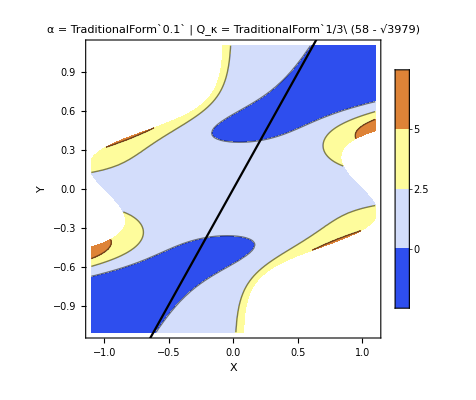
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Clear[α]; Print[]; Reduce[consJ0&&consJ1&&consJ2,{α,Subscript[Q, κ]},Reals]

{Subscript[Ω, m],Subscript[Ω, r]}={0,0}; α=10^(-1);

Mod[ArcTan[βval/.Subscript[Q, κ]->{1/3 (58-√3979),8.55,1/3 (58+√3979)}//N]/Degree,180] (* Angle of the line Y=βX *)

L=1.1; Print[];
Table[Show[{
ContourPlot[ϵxy,{X,-L,L},{Y,-L,L},ColorFunction->"TemperatureMap",PlotLegends->Automatic,RegionFunction->Function[{X,Y},Z4≥0]],
(*StreamPlot[{Xp//NoMoreFPϵ,X},{X,-L,L},{Y,-L,L},StreamColorFunction->Hue,RegionFunction->Function[{X,Y},Z4≥0]],*)
Plot[βval X,{X,-L,L},PlotStyle->Black]},
PlotLabel->StringForm["α = `` | Q_κ = ``",α//N,Subscript[Q, κ]],RotateLabel->False,FrameLabel->{"X","Y"}],{Subscript[Q, κ],{1/3 (58-√3979),8.55,1/3 (58+√3979)}}] (* The second value is approximately 77/9 *)

Print[];
```

### Only α, κ, λ

```mathematica
Clear[ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1],Subscript[Ω, m],Subscript[Ω, r]]; Print[]; aux1={}; aux2={}; NumSum={};NumPrd={}; Den={}; 
{ξ,α,κ,λ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4],Subscript[θ, 1]}={1,α,Subscript[Q, κ] α,Subscript[Q, λ] α,0,0,0,0,0,0,0}; t0=AbsoluteTime[];
SolveForThis={α,Subscript[Q, κ],Subscript[Q, λ]}; AssumeThis=(α≠0);

Print[fried==0,"\n",eq1==0,"\n",eq2==0,"\n\n",
"Z^4 = ",(Zval^4//FullSimplify),"\n","P = ",(Pval//FullSimplify),"\n","ϵ = ",(ϵval//FullSimplify),"\n"]
cons01=Reduce[βval<0&&γval^4>0,Reals,Backsubstitution->True]; 
cons02=Reduce[βval>0&&γval^4>0,Reals,Backsubstitution->True];
consJ0=Reduce[(cons01||cons02)&&AssumeThis,SolveForThis,Reals];Print[
"\n0. Expressions involving β,γ","\n\n   β = ",(βval//FullSimplify)," , γ^4 = ",(γvalAbs^4//Simplify),
"\n\n0.1. Conditions for  [ β < 0 , γ ∈ ℝ ]\n\n   ",cons01,
"\n\n\n0.2. Conditions for  [ β > 0 , γ ∈ ℝ ]\n\n   ",cons02,
"\n\n J0. Joint constraints for  [ ASYMPTOTIC BEHAVIOUR ] (0.1||0.2) \n\n   ",consJ0];

tt=CoefficientList[lambdaSum,OverHat[ψ],{5}]//FullSimplify;
dd=CoefficientList[lambdaPrd,OverHat[ψ],{7}]//FullSimplify;
For[i=1,i≤Length[consT],i++,AppendTo[aux1,((consT[[i]]/.Subscript[t,k_]:>tt[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[aux2,((consD[[i]]/.Subscript[d,k_]:>dd[[k+1]]))//Simplify]];
cons11=Reduce[Apply[Or,aux1],Reals,Backsubstitution->True];
cons12=Reduce[Apply[Or,aux2],Reals,Backsubstitution->True];
consJ1=Reduce[cons11&&cons12&&AssumeThis,SolveForThis,Reals];Print[
"\n\n1. Expressions involving Eigenvalues[ 𝕂 ]","\n\n   λ_+ + λ_- = ",lambdaSum,"\n   λ_+ * λ_- = ",lambdaPrd,
"\n\n\n1.1. Conditions for  [ λ_+ + λ_- > 0 ]\n\n   ",cons11,
"\n\n\n1.2. Conditions for  [ λ_+ * λ_- > 0 ]\n\n   ",cons12,
"\n\n\n J1. Joint constraints for  [ NO-GHOSTS ] (1.1∧1.2) \n\n   ",consJ1,"\n"]

ns=CoefficientList[Numerator[cssum],OverHat[ψ],7]//FullSimplify;
np=CoefficientList[Numerator[csprd],OverHat[ψ],7]//FullSimplify;
dsp=CoefficientList[Denominator[cssum],OverHat[ψ],7]//FullSimplify;
For[i=1,i≤Length[consD],i++,AppendTo[NumSum,((consD[[i]]/.Subscript[d,k_]:>ns[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[NumPrd,((consD[[i]]/.Subscript[d,k_]:>np[[k+1]]))//Simplify]];
For[i=1,i≤Length[consD],i++,AppendTo[Den,((consD[[i]]/.Subscript[d,k_]:>dsp[[k+1]]))//Simplify]];
cons21=Reduce[Apply[Or,NumSum]&&AssumeThis,SolveForThis,Reals];
cons22=Reduce[Apply[Or,NumPrd]&&AssumeThis,SolveForThis,Reals];
cons23=Reduce[Apply[Or,Den]&&AssumeThis,SolveForThis,Reals];
consJ2=Reduce[cons21&&cons22&&cons23&&AssumeThis,SolveForThis,Reals];Print[
"\n2. Expressions involving  c_s^2 ","\n\n   c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = ",cssum,"\n   c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 = ",csprd,
"\n\n2.1. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 ] > 0\n\n   ",cons21,
"\n\n\n2.2. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 ] > 0\n\n   ",cons22,
"\n\n\n2.3. Conditions for Denominator > 0\n\n   ",cons23,
"\n\n\n J2. Joint constraints for [ NO-LAPLACIAN INSTABILITIES ] (2.1∧2.2∧2.3) \n\n   ",consJ2,"\n"]

(*
Reduce[Reduce[ForAll[OverHat[ψ],cs21≤1],Reals]&&AssumeThis,SolveForThis,Reals]
cons31=Resolve[ForAll[OverHat[ψ],%&&consJ2],Reals]
Reduce[Reduce[ForAll[OverHat[ψ],cs22≤1],Reals]&&AssumeThis,SolveForThis,Reals]
cons32=Resolve[ForAll[OverHat[ψ],%&&consJ2],Reals]
consJ3=Reduce[cons31&&cons32&&AssumeThis,SolveForThis,Reals];
Print["\n3.1 Conditions for 0 < c_(s, SubscriptBox[h, ±])^2 ≤ 1\n\n   ",cons31,"\n\n   c_(s, SubscriptBox[h, ±])^2 = ",Simplify[cs21,cons31],
"\n\n3.2 Conditions for 0 < c_(s, SubscriptBox[γ, ±])^2 ≤ 1\n\n   ",cons32,"\n\n   c_(s, SubscriptBox[γ, ±])^2 = ",Simplify[cs22,cons32],
"\n\n J3. Joint constraints for [ CAUSALITY ] (3.1∧3.2∧J2) \n\n   ",consJ3,"\n"]
*)

consJ4=Resolve[ForAll[OverHat[ψ],Denominator[cssum]≠0&&Numerator[cssum]==Denominator[cssum]+Numerator[csprd]&&AssumeThis],Reals];Print[
"\n 4. Joint constraints for [ GRAVITATIONAL WAVES ] \n\n   ",consJ4,"\n\n   c_(s, SubscriptBox[h, ±])^2 = ",Simplify[cs21,consJ4],"\n\n   c_(s, SubscriptBox[γ, ±])^2 = ",Simplify[cs22,consJ4],"\n"]

(*
Print["\n Summary of CONSTRAINTS (J1∧J2∧J3) \n\n   ",Reduce[consJ1&&consJ2&&consJ3&&AssumeThis,SolveForThis,Reals],"\n"]
Print["\n Summary of CONSTRAINTS (J1∧J2∧J3∧J4) \n\n   ",Reduce[consJ1&&consJ2&&consJ3&&consJ4&&AssumeThis,SolveForThis,Reals],"\n"]
*)

Clear[α,ξ,κ,λ,Subscript[θ, 1],Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 34],Subscript[χ, 4]];
Print["\n\nThis process took about ",Round[(AbsoluteTime[]-t0)/60,0.001]," minutes.\n"];
```

25.0876-10.2152 X+X^2+(2 q^2 Z^4)/F^4+Q_κ (-8166.76+2664.9 X+52.1752 X^2) α+(-21778.+25050.1 X+260.876 X^2) α==0
29.0876-10.2152 X+X^2+(2 q^2 Z^4)/F^4+Q_κ α (16333.5-2261.24 P-14390.5 X+1826.13 X^2-2722.25 ϵ)-2 ϵ+α (-231391.-19597.5 P-42105.5 X+16017.8 X^2+84389.8 ϵ)==0
-10.2152+P/(√2)+3 X-(0.783146 q^2 Z^4)/F^4+α (29047.4+184.467 P+782.628 X-51.076 X^2-12525. ϵ)+Q_κ α (799.471+36.8934 P+156.526 X-10.2152 X^2-1332.45 ϵ)+5.1076 ϵ==0

Z^4 = -26.0876 (0.480834+(-417.402-156.526 Q_κ) α+X (-0.195787+(480.115+51.076 Q_κ) α+X (0.0191662+(5.+1. Q_κ) α)))
P = ((-6.31049×10^-6+α (0.336169-287.066 α+Q_κ (-0.0365979+(-74.0965+12.5824 Q_κ) α))+X (6.42378×10^-7+α (0.0762602+16.9249 α+Q_κ (0.0280829+(-74.0865-8.34842 Q_κ) α)))+X^2 (-2.51538×10^-7+α (-0.0152685+64.773 α+Q_κ (-0.00325912+(14.1122+0.750266 Q_κ) α))))/(4.5423×10^-7+α (-0.0511974+73.8387 α+Q_κ (-0.00306762+(16.6452+1. Q_κ) α))))
ϵ = ((9.0846×10^-7+α (-0.0498341+116.742 α+Q_κ^2 (-1.45161+(0.669464+0.0284402 X) X) α+X (-0.0215465+62.6896 α+X (0.00604338+1.25508 α))+Q_κ (0.00532738-1.22581 α+X (-0.00459982+X (0.000687287+0.393216 α)+13.4398 α))))/(4.5423×10^-7+α (-0.0511974+73.8387 α+Q_κ (-0.00306762+(16.6452+1. Q_κ) α))))

0. Expressions involving β,γ

   β = (203+23 Q_κ)/(77-9 Q_κ) , γ^4 = ((203+23 Q_κ)^2 (917+33 Q_κ) (2289+516 Q_κ+31 Q_κ^2) α)/(77-9 Q_κ)^4

0.1. Conditions for  [ β < 0 , γ ∈ ℝ ]

   (α<0&&Q_κ<-917/33)||(α>0&&-917/33<Q_κ<-203/23)||(α>0&&Q_κ>77/9)


0.2. Conditions for  [ β > 0 , γ ∈ ℝ ]

   α>0&&-203/23<Q_κ<77/9

 J0. Joint constraints for  [ ASYMPTOTIC BEHAVIOUR ] (0.1||0.2) 

   (α<0&&Q_κ<-917/33)||(α>0&&-917/33<Q_κ<-203/23)||(α>0&&-203/23<Q_κ<77/9)||(α>0&&Q_κ>77/9)

1. Expressions involving Eigenvalues[ 𝕂 ]

   λ_+ + λ_- = 5/4+(5 α+Q_κ α) (ψ̂)^2+1/8 (61 α+19 Q_κ α) (ψ̂)^4
   λ_+ * λ_- = 1/8 (2+2 (5 α+Q_κ α) (ψ̂)^2+(61 α+19 Q_κ α) (ψ̂)^4+(105 α^2+36 Q_κ α^2+Q_κ^2 α^2) (ψ̂)^6)


1.1. Conditions for  [ λ_+ + λ_- > 0 ]

   (Q_κ≤-5&&α≤0)||(-5<Q_κ<-61/19&&(5 (61+19 Q_κ))/(8 (5+Q_κ)^2)<α≤0)||(Q_κ≥-61/19&&α≥0)


1.2. Conditions for  [ λ_+ * λ_- > 0 ]

   (Q_κ≤-18-√219&&α≤0)||(-18-√219<Q_κ<-18+√219&&α==0)||(Q_κ≥-18+√219&&α≥0)


 J1. Joint constraints for  [ NO-GHOSTS ] (1.1∧1.2) 

   (α<0&&Q_κ≤-18-√219)||(α>0&&Q_κ≥-18+√219)

2. Expressions involving  c_s^2 

   c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 = (4+4 (5 α+Q_κ α) (ψ̂)^2+2 (71 α+9 Q_κ α) (ψ̂)^4+2 (155 α^2+76 Q_κ α^2+15 Q_κ^2 α^2+4 Q_λ^2 α^2) (ψ̂)^6)/(2+2 (5 α+Q_κ α) (ψ̂)^2+(61 α+19 Q_κ α) (ψ̂)^4+(105 α^2+36 Q_κ α^2+Q_κ^2 α^2) (ψ̂)^6)
   c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 = (2+2 (5 α+Q_κ α) (ψ̂)^2+(81 α-Q_κ α) (ψ̂)^4+(205 α^2+116 Q_κ α^2-3 Q_κ^2 α^2) (ψ̂)^6)/(2+2 (5 α+Q_κ α) (ψ̂)^2+(61 α+19 Q_κ α) (ψ̂)^4+(105 α^2+36 Q_κ α^2+Q_κ^2 α^2) (ψ̂)^6)

2.1. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 + c_(s, SubscriptBox[γ, ±])^2 ] > 0

   (α<Root[-389782449+59670992844 #1+69545079324 #1^2-25933942400 #1^3+5074560000 #1^4&,1]&&(Q_κ<Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,1]||(Q_κ==Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,1]&&(Q_λ<0||Q_λ>0))||(Q_κ>Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,1]&&(Q_λ<-√(1/54 (-495-504 Q_κ-162 Q_κ^2-250 α-150 Q_κ α-30 Q_κ^2 α-2 Q_κ^3 α)+1/(54 √2)(√(1/α(-9663597-3674889 Q_κ-465831 Q_κ^2-19683 Q_κ^3+6805350 α+4447440 Q_κ α+1071684 Q_κ^2 α+112752 Q_κ^3 α+4374 Q_κ^4 α-1597500 α^2-1480500 Q_κ α^2-545400 Q_κ^2 α^2-99720 Q_κ^3 α^2-9036 Q_κ^4 α^2-324 Q_κ^5 α^2+125000 α^3+150000 Q_κ α^3+75000 Q_κ^2 α^3+20000 Q_κ^3 α^3+3000 Q_κ^4 α^3+240 Q_κ^5 α^3+8 Q_κ^6 α^3))))||Q_λ>√(1/54 (-495-504 Q_κ-162 Q_κ^2-250 α-150 Q_κ α-30 Q_κ^2 α-2 Q_κ^3 α)+1/(54 √2)(√(1/α(-9663597-3674889 Q_κ-465831 Q_κ^2-19683 Q_κ^3+6805350 α+4447440 Q_κ α+1071684 Q_κ^2 α+112752 Q_κ^3 α+4374 Q_κ^4 α-1597500 α^2-1480500 Q_κ α^2-545400 Q_κ^2 α^2-99720 Q_κ^3 α^2-9036 Q_κ^4 α^2-324 Q_κ^5 α^2+125000 α^3+150000 Q_κ α^3+75000 Q_κ^2 α^3+20000 Q_κ^3 α^3+3000 Q_κ^4 α^3+240 Q_κ^5 α^3+8 Q_κ^6 α^3))))))))||(α==Root[-389782449+59670992844 #1+69545079324 #1^2-25933942400 #1^3+5074560000 #1^4&,1]&&(Q_κ<Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,1]||(Q_κ==Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,1]&&(Q_λ<0||Q_λ>0))||(Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,1]<Q_κ<Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,2]&&(Q_λ<-√(1/54 (-495-504 Q_κ-162 Q_κ^2-250 α-150 Q_κ α-30 Q_κ^2 α-2 Q_κ^3 α)+1/(54 √2)(√(1/α(-9663597-3674889 Q_κ-465831 Q_κ^2-19683 Q_κ^3+6805350 α+4447440 Q_κ α+1071684 Q_κ^2 α+112752 Q_κ^3 α+4374 Q_κ^4 α-1597500 α^2-1480500 Q_κ α^2-545400 Q_κ^2 α^2-99720 Q_κ^3 α^2-9036 Q_κ^4 α^2-324 Q_κ^5 α^2+125000 α^3+150000 Q_κ α^3+75000 Q_κ^2 α^3+20000 Q_κ^3 α^3+3000 Q_κ^4 α^3+240 Q_κ^5 α^3+8 Q_κ^6 α^3))))||Q_λ>√(1/54 (-495-504 Q_κ-162 Q_κ^2-250 α-150 Q_κ α-30 Q_κ^2 α-2 Q_κ^3 α)+1/(54 √2)(√(1/α(-9663597-3674889 Q_κ-465831 Q_κ^2-19683 Q_κ^3+6805350 α+4447440 Q_κ α+1071684 Q_κ^2 α+112752 Q_κ^3 α+4374 Q_κ^4 α-1597500 α^2-1480500 Q_κ α^2-545400 Q_κ^2 α^2-99720 Q_κ^3 α^2-9036 Q_κ^4 α^2-324 Q_κ^5 α^2+125000 α^3+150000 Q_κ α^3+75000 Q_κ^2 α^3+20000 Q_κ^3 α^3+3000 Q_κ^4 α^3+240 Q_κ^5 α^3+8 Q_κ^6 α^3))))))||(Q_κ==Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,2]&&(Q_λ<0||Q_λ>0))||(Q_κ>Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,2]&&(Q_λ<-√(1/54 (-495-504 Q_κ-162 Q_κ^2-250 α-150 Q_κ α-30 Q_κ^2 α-2 Q_κ^3 α)+1/(54 √2)(√(1/α(-9663597-3674889 Q_κ-465831 Q_κ^2-19683 Q_κ^3+6805350 α+4447440 Q_κ α+1071684 Q_κ^2 α+112752 Q_κ^3 α+4374 Q_κ^4 α-1597500 α^2-1480500 Q_κ α^2-545400 Q_κ^2 α^2-99720 Q_κ^3 α^2-9036 Q_κ^4 α^2-324 Q_κ^5 α^2+125000 α^3+150000 Q_κ α^3+75000 Q_κ^2 α^3+20000 Q_κ^3 α^3+3000 Q_κ^4 α^3+240 Q_κ^5 α^3+8 Q_κ^6 α^3))))||Q_λ>√(1/54 (-495-504 Q_κ-162 Q_κ^2-250 α-150 Q_κ α-30 Q_κ^2 α-2 Q_κ^3 α)+1/(54 √2)(√(1/α(-9663597-3674889 Q_κ-465831 Q_κ^2-19683 Q_κ^3+6805350 α+4447440 Q_κ α+1071684 Q_κ^2 α+112752 Q_κ^3 α+4374 Q_κ^4 α-1597500 α^2-1480500 Q_κ α^2-545400 Q_κ^2 α^2-99720 Q_κ^3 α^2-9036 Q_κ^4 α^2-324 Q_κ^5 α^2+125000 α^3+150000 Q_κ α^3+75000 Q_κ^2 α^3+20000 Q_κ^3 α^3+3000 Q_κ^4 α^3+240 Q_κ^5 α^3+8 Q_κ^6 α^3))))))))||(Root[-389782449+59670992844 #1+69545079324 #1^2-25933942400 #1^3+5074560000 #1^4&,1]<α<0&&(Q_κ<Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,1]||(Q_κ==Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,1]&&(Q_λ<0||Q_λ>0))||(Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,1]<Q_κ<Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,2]&&(Q_λ<-√(1/54 (-495-504 Q_κ-162 Q_κ^2-250 α-150 Q_κ α-30 Q_κ^2 α-2 Q_κ^3 α)+1/(54 √2)(√(1/α(-9663597-3674889 Q_κ-465831 Q_κ^2-19683 Q_κ^3+6805350 α+4447440 Q_κ α+1071684 Q_κ^2 α+112752 Q_κ^3 α+4374 Q_κ^4 α-1597500 α^2-1480500 Q_κ α^2-545400 Q_κ^2 α^2-99720 Q_κ^3 α^2-9036 Q_κ^4 α^2-324 Q_κ^5 α^2+125000 α^3+150000 Q_κ α^3+75000 Q_κ^2 α^3+20000 Q_κ^3 α^3+3000 Q_κ^4 α^3+240 Q_κ^5 α^3+8 Q_κ^6 α^3))))||Q_λ>√(1/54 (-495-504 Q_κ-162 Q_κ^2-250 α-150 Q_κ α-30 Q_κ^2 α-2 Q_κ^3 α)+1/(54 √2)(√(1/α(-9663597-3674889 Q_κ-465831 Q_κ^2-19683 Q_κ^3+6805350 α+4447440 Q_κ α+1071684 Q_κ^2 α+112752 Q_κ^3 α+4374 Q_κ^4 α-1597500 α^2-1480500 Q_κ α^2-545400 Q_κ^2 α^2-99720 Q_κ^3 α^2-9036 Q_κ^4 α^2-324 Q_κ^5 α^2+125000 α^3+150000 Q_κ α^3+75000 Q_κ^2 α^3+20000 Q_κ^3 α^3+3000 Q_κ^4 α^3+240 Q_κ^5 α^3+8 Q_κ^6 α^3))))))||(Q_κ==Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,2]&&(Q_λ<0||Q_λ>0))||Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,2]<Q_κ<Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,3]||(Q_κ==Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,3]&&(Q_λ<0||Q_λ>0))||(Q_κ>Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,3]&&(Q_λ<-√(1/54 (-495-504 Q_κ-162 Q_κ^2-250 α-150 Q_κ α-30 Q_κ^2 α-2 Q_κ^3 α)+1/(54 √2)(√(1/α(-9663597-3674889 Q_κ-465831 Q_κ^2-19683 Q_κ^3+6805350 α+4447440 Q_κ α+1071684 Q_κ^2 α+112752 Q_κ^3 α+4374 Q_κ^4 α-1597500 α^2-1480500 Q_κ α^2-545400 Q_κ^2 α^2-99720 Q_κ^3 α^2-9036 Q_κ^4 α^2-324 Q_κ^5 α^2+125000 α^3+150000 Q_κ α^3+75000 Q_κ^2 α^3+20000 Q_κ^3 α^3+3000 Q_κ^4 α^3+240 Q_κ^5 α^3+8 Q_κ^6 α^3))))||Q_λ>√(1/54 (-495-504 Q_κ-162 Q_κ^2-250 α-150 Q_κ α-30 Q_κ^2 α-2 Q_κ^3 α)+1/(54 √2)(√(1/α(-9663597-3674889 Q_κ-465831 Q_κ^2-19683 Q_κ^3+6805350 α+4447440 Q_κ α+1071684 Q_κ^2 α+112752 Q_κ^3 α+4374 Q_κ^4 α-1597500 α^2-1480500 Q_κ α^2-545400 Q_κ^2 α^2-99720 Q_κ^3 α^2-9036 Q_κ^4 α^2-324 Q_κ^5 α^2+125000 α^3+150000 Q_κ α^3+75000 Q_κ^2 α^3+20000 Q_κ^3 α^3+3000 Q_κ^4 α^3+240 Q_κ^5 α^3+8 Q_κ^6 α^3))))))))||(0<α<Root[-389782449+59670992844 #1+69545079324 #1^2-25933942400 #1^3+5074560000 #1^4&,2]&&((Q_κ<Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,1]&&(Q_λ<-√(1/54 (-495-504 Q_κ-162 Q_κ^2-250 α-150 Q_κ α-30 Q_κ^2 α-2 Q_κ^3 α)+1/(54 √2)(√(1/α(-9663597-3674889 Q_κ-465831 Q_κ^2-19683 Q_κ^3+6805350 α+4447440 Q_κ α+1071684 Q_κ^2 α+112752 Q_κ^3 α+4374 Q_κ^4 α-1597500 α^2-1480500 Q_κ α^2-545400 Q_κ^2 α^2-99720 Q_κ^3 α^2-9036 Q_κ^4 α^2-324 Q_κ^5 α^2+125000 α^3+150000 Q_κ α^3+75000 Q_κ^2 α^3+20000 Q_κ^3 α^3+3000 Q_κ^4 α^3+240 Q_κ^5 α^3+8 Q_κ^6 α^3))))||Q_λ>√(1/54 (-495-504 Q_κ-162 Q_κ^2-250 α-150 Q_κ α-30 Q_κ^2 α-2 Q_κ^3 α)+1/(54 √2)(√(1/α(-9663597-3674889 Q_κ-465831 Q_κ^2-19683 Q_κ^3+6805350 α+4447440 Q_κ α+1071684 Q_κ^2 α+112752 Q_κ^3 α+4374 Q_κ^4 α-1597500 α^2-1480500 Q_κ α^2-545400 Q_κ^2 α^2-99720 Q_κ^3 α^2-9036 Q_κ^4 α^2-324 Q_κ^5 α^2+125000 α^3+150000 Q_κ α^3+75000 Q_κ^2 α^3+20000 Q_κ^3 α^3+3000 Q_κ^4 α^3+240 Q_κ^5 α^3+8 Q_κ^6 α^3))))))||(Q_κ==Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,1]&&(Q_λ<0||Q_λ>0))||Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,1]<Q_κ<Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,2]||(Q_κ==Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,2]&&(Q_λ<0||Q_λ>0))||(Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,2]<Q_κ<Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,3]&&(Q_λ<-√(1/54 (-495-504 Q_κ-162 Q_κ^2-250 α-150 Q_κ α-30 Q_κ^2 α-2 Q_κ^3 α)+1/(54 √2)(√(1/α(-9663597-3674889 Q_κ-465831 Q_κ^2-19683 Q_κ^3+6805350 α+4447440 Q_κ α+1071684 Q_κ^2 α+112752 Q_κ^3 α+4374 Q_κ^4 α-1597500 α^2-1480500 Q_κ α^2-545400 Q_κ^2 α^2-99720 Q_κ^3 α^2-9036 Q_κ^4 α^2-324 Q_κ^5 α^2+125000 α^3+150000 Q_κ α^3+75000 Q_κ^2 α^3+20000 Q_κ^3 α^3+3000 Q_κ^4 α^3+240 Q_κ^5 α^3+8 Q_κ^6 α^3))))||Q_λ>√(1/54 (-495-504 Q_κ-162 Q_κ^2-250 α-150 Q_κ α-30 Q_κ^2 α-2 Q_κ^3 α)+1/(54 √2)(√(1/α(-9663597-3674889 Q_κ-465831 Q_κ^2-19683 Q_κ^3+6805350 α+4447440 Q_κ α+1071684 Q_κ^2 α+112752 Q_κ^3 α+4374 Q_κ^4 α-1597500 α^2-1480500 Q_κ α^2-545400 Q_κ^2 α^2-99720 Q_κ^3 α^2-9036 Q_κ^4 α^2-324 Q_κ^5 α^2+125000 α^3+150000 Q_κ α^3+75000 Q_κ^2 α^3+20000 Q_κ^3 α^3+3000 Q_κ^4 α^3+240 Q_κ^5 α^3+8 Q_κ^6 α^3))))))||(Q_κ==Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,3]&&(Q_λ<0||Q_λ>0))||Q_κ>Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,3]))||(α==Root[-389782449+59670992844 #1+69545079324 #1^2-25933942400 #1^3+5074560000 #1^4&,2]&&((Q_κ<Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,1]&&(Q_λ<-√(1/54 (-495-504 Q_κ-162 Q_κ^2-250 α-150 Q_κ α-30 Q_κ^2 α-2 Q_κ^3 α)+1/(54 √2)(√(1/α(-9663597-3674889 Q_κ-465831 Q_κ^2-19683 Q_κ^3+6805350 α+4447440 Q_κ α+1071684 Q_κ^2 α+112752 Q_κ^3 α+4374 Q_κ^4 α-1597500 α^2-1480500 Q_κ α^2-545400 Q_κ^2 α^2-99720 Q_κ^3 α^2-9036 Q_κ^4 α^2-324 Q_κ^5 α^2+125000 α^3+150000 Q_κ α^3+75000 Q_κ^2 α^3+20000 Q_κ^3 α^3+3000 Q_κ^4 α^3+240 Q_κ^5 α^3+8 Q_κ^6 α^3))))||Q_λ>√(1/54 (-495-504 Q_κ-162 Q_κ^2-250 α-150 Q_κ α-30 Q_κ^2 α-2 Q_κ^3 α)+1/(54 √2)(√(1/α(-9663597-3674889 Q_κ-465831 Q_κ^2-19683 Q_κ^3+6805350 α+4447440 Q_κ α+1071684 Q_κ^2 α+112752 Q_κ^3 α+4374 Q_κ^4 α-1597500 α^2-1480500 Q_κ α^2-545400 Q_κ^2 α^2-99720 Q_κ^3 α^2-9036 Q_κ^4 α^2-324 Q_κ^5 α^2+125000 α^3+150000 Q_κ α^3+75000 Q_κ^2 α^3+20000 Q_κ^3 α^3+3000 Q_κ^4 α^3+240 Q_κ^5 α^3+8 Q_κ^6 α^3))))))||(Q_κ==Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,1]&&(Q_λ<0||Q_λ>0))||Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,1]<Q_κ<Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,2]||(Q_κ==Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,2]&&(Q_λ<0||Q_λ>0))||Q_κ>Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,2]))||(α>Root[-389782449+59670992844 #1+69545079324 #1^2-25933942400 #1^3+5074560000 #1^4&,2]&&((Q_κ<Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,1]&&(Q_λ<-√(1/54 (-495-504 Q_κ-162 Q_κ^2-250 α-150 Q_κ α-30 Q_κ^2 α-2 Q_κ^3 α)+1/(54 √2)(√(1/α(-9663597-3674889 Q_κ-465831 Q_κ^2-19683 Q_κ^3+6805350 α+4447440 Q_κ α+1071684 Q_κ^2 α+112752 Q_κ^3 α+4374 Q_κ^4 α-1597500 α^2-1480500 Q_κ α^2-545400 Q_κ^2 α^2-99720 Q_κ^3 α^2-9036 Q_κ^4 α^2-324 Q_κ^5 α^2+125000 α^3+150000 Q_κ α^3+75000 Q_κ^2 α^3+20000 Q_κ^3 α^3+3000 Q_κ^4 α^3+240 Q_κ^5 α^3+8 Q_κ^6 α^3))))||Q_λ>√(1/54 (-495-504 Q_κ-162 Q_κ^2-250 α-150 Q_κ α-30 Q_κ^2 α-2 Q_κ^3 α)+1/(54 √2)(√(1/α(-9663597-3674889 Q_κ-465831 Q_κ^2-19683 Q_κ^3+6805350 α+4447440 Q_κ α+1071684 Q_κ^2 α+112752 Q_κ^3 α+4374 Q_κ^4 α-1597500 α^2-1480500 Q_κ α^2-545400 Q_κ^2 α^2-99720 Q_κ^3 α^2-9036 Q_κ^4 α^2-324 Q_κ^5 α^2+125000 α^3+150000 Q_κ α^3+75000 Q_κ^2 α^3+20000 Q_κ^3 α^3+3000 Q_κ^4 α^3+240 Q_κ^5 α^3+8 Q_κ^6 α^3))))))||(Q_κ==Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,1]&&(Q_λ<0||Q_λ>0))||Q_κ>Root[357911-233900 α+77500 α^2+(136107-127760 α+84500 α^2) #1+(17253-8996 α+39600 α^2) #1^2+(729+7920 α+9680 α^2) #1^3+(1782 α+1204 α^2) #1^4+60 α^2 #1^5&,1]))


2.2. Conditions for Num[ c_(s, SubscriptBox[h, ±])^2 * c_(s, SubscriptBox[γ, ±])^2 ] > 0

   α>0&&1/3 (58-√3979)≤Q_κ≤1/3 (58+√3979)


2.3. Conditions for Denominator > 0

   (α<0&&Q_κ≤-18-√219)||(α>0&&Q_κ≥-18+√219)


 J2. Joint constraints for [ NO-LAPLACIAN INSTABILITIES ] (2.1∧2.2∧2.3) 

   α>0&&1/3 (58-√3979)≤Q_κ≤1/3 (58+√3979)

4. Joint constraints for [ GRAVITATIONAL WAVES ] 

   α>0&&Q_κ==0&&Q_λ==0

   c_(s, SubscriptBox[h, ±])^2 = 1

   c_(s, SubscriptBox[γ, ±])^2 = (2+10 α (ψ̂)^2+81 α (ψ̂)^4+205 α^2 (ψ̂)^6)/(2+10 α (ψ̂)^2+61 α (ψ̂)^4+105 α^2 (ψ̂)^6)

This process took about 0.113 minutes.

## 5. Numeric solution

```mathematica
Clear@@DeleteCases[Names@"`*","fried"|"Qi"|"Qf"|"asintotas"];

soln[t0_,Ωr0_,Ωm0_,x0_,y0_,ξ_,g_,α_,κ_,θ4_,χ1_,χ2_,χ3_,χ4_,θ1_]:=NDSolve[
{
 x'[t]==(y[t] (-4 Subscript[θ, 1]-ξ+2 (47 α+16 Subscript[θ, 4]+5 κ+4 Subscript[χ, 3]+4 Subscript[χ, 4]) y[t]^2) (-4+12 Subscript[θ, 1] y[t]^2+4 (77 α-16 Subscript[θ, 4]-9 κ-2 Subscript[χ, 3]-2 Subscript[χ, 4]) y[t]^4-4 x[t]^2 (-2 Subscript[θ, 1]+(151 α+48 Subscript[θ, 4]+17 κ+2 Subscript[χ, 3]+2 Subscript[χ, 4]) y[t]^2)-8 x[t] (-4 Subscript[θ, 1] y[t]+(63 α+2 (20 Subscript[θ, 4]+8 κ+Subscript[χ, 3]+Subscript[χ, 4])) y[t]^3)+Ωm[t])-1/((g^2 ξ-6 (Subscript[χ, 1]+Subscript[χ, 2])) y[t])2 (-1+2 Subscript[θ, 1] y[t]^2+(62 α-2 κ) y[t]^4) (g^2 ξ (x[t] y[t] (16 Subscript[θ, 1]+ξ-2 (203 α+64 Subscript[θ, 4]+23 κ-8 Subscript[χ, 3]-8 Subscript[χ, 4]) y[t]^2)+2 x[t]^2 (ξ+(5 α+κ+2 (Subscript[χ, 3]+Subscript[χ, 4])) y[t]^2)+2 (-1+3 Subscript[θ, 1] y[t]^2+(77 α-16 Subscript[θ, 4]-9 κ+2 Subscript[χ, 3]+2 Subscript[χ, 4]) y[t]^4+Ωm[t]+Ωr[t]))-2 (3 Subscript[χ, 1] (x[t] y[t] (16 Subscript[θ, 1]+ξ-2 (203 α+64 Subscript[θ, 4]+23 κ-8 Subscript[χ, 3]-8 Subscript[χ, 4]) y[t]^2)+2 x[t]^2 (ξ+(5 α+κ+2 (Subscript[χ, 3]+Subscript[χ, 4])) y[t]^2)+2 (-1+3 Subscript[θ, 1] y[t]^2+(77 α-16 Subscript[θ, 4]-9 κ+2 Subscript[χ, 3]+2 Subscript[χ, 4]) y[t]^4+Ωm[t]+Ωr[t]))+Subscript[χ, 2] (x[t] y[t] (16 Subscript[θ, 1]-5 ξ-2 (233 α+64 Subscript[θ, 4]+29 κ-40 Subscript[χ, 3]-40 Subscript[χ, 4]) y[t]^2)+2 x[t]^2 (ξ-(5 α+κ-14 (Subscript[χ, 3]+Subscript[χ, 4])) y[t]^2)+2 (-1-(3 Subscript[θ, 1]+2 ξ) y[t]^2+(295 α+16 Subscript[θ, 4]-3 κ+14 Subscript[χ, 3]+14 Subscript[χ, 4]) y[t]^4+Ωm[t]+Ωr[t]))))-1/(g^2 ξ-6 (Subscript[χ, 1]+Subscript[χ, 2]))x[t] (g^2 ξ (-16 Subscript[θ, 1]-4 ξ+24 Subscript[θ, 1] ξ x[t]^2+8 Subscript[θ, 1] (16 Subscript[θ, 1]+5 ξ) x[t] y[t]-8 (α (782 Subscript[θ, 1]+89 ξ)+ξ (48 Subscript[θ, 4]+19 κ+2 (Subscript[χ, 3]+Subscript[χ, 4]))+2 Subscript[θ, 1] (128 Subscript[θ, 4]+43 κ+8 (Subscript[χ, 3]+Subscript[χ, 4]))) x[t] y[t]^3-4 (-26 α Subscript[θ, 1]+160 Subscript[θ, 1] Subscript[θ, 4]+66 Subscript[θ, 1] κ-77 α ξ+16 Subscript[θ, 4] ξ+9 κ ξ+16 Subscript[θ, 1] Subscript[χ, 3]+2 ξ Subscript[χ, 3]+16 Subscript[θ, 1] Subscript[χ, 4]+2 ξ Subscript[χ, 4]+2 (1015 α^2+23 κ^2-54 κ Subscript[χ, 3]-8 Subscript[χ, 3]^2-54 κ Subscript[χ, 4]-16 Subscript[χ, 3] Subscript[χ, 4]-8 Subscript[χ, 4]^2+α (320 Subscript[θ, 4]+318 κ-490 (Subscript[χ, 3]+Subscript[χ, 4]))+32 Subscript[θ, 4] (2 κ-5 (Subscript[χ, 3]+Subscript[χ, 4]))) x[t]^2) y[t]^4+16 (4963 α^2+512 Subscript[θ, 4]^2+53 κ^2+38 κ Subscript[χ, 3]+8 Subscript[χ, 3]^2+38 κ Subscript[χ, 4]+16 Subscript[χ, 3] Subscript[χ, 4]+8 Subscript[χ, 4]^2+48 Subscript[θ, 4] (7 κ+2 (Subscript[χ, 3]+Subscript[χ, 4]))+2 α (1544 Subscript[θ, 4]+532 κ+17 (Subscript[χ, 3]+Subscript[χ, 4]))) x[t] y[t]^5-8 (3619 α^2-256 Subscript[θ, 4]^2-45 κ^2-22 κ Subscript[χ, 3]-8 Subscript[χ, 3]^2-22 κ Subscript[χ, 4]-16 Subscript[χ, 3] Subscript[χ, 4]-8 Subscript[χ, 4]^2-32 Subscript[θ, 4] (7 κ+Subscript[χ, 3]+Subscript[χ, 4])+α (480 Subscript[θ, 4]-38 κ+422 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^6+16 Subscript[θ, 1] Ωm[t]+ξ Ωm[t]+16 Subscript[θ, 1] Ωr[t]+2 y[t]^2 (24 Subscript[θ, 1]^2+64 Subscript[θ, 4]+20 κ+16 Subscript[χ, 3]+16 Subscript[χ, 4]-160 Subscript[θ, 4] ξ x[t]^2-58 κ ξ x[t]^2-4 ξ Subscript[χ, 3] x[t]^2-4 ξ Subscript[χ, 4] x[t]^2+2 Subscript[θ, 1] (3 ξ+8 (κ-Subscript[χ, 3]-Subscript[χ, 4]) x[t]^2)-64 Subscript[θ, 4] Ωm[t]-23 κ Ωm[t]-4 Subscript[χ, 3] Ωm[t]-4 Subscript[χ, 4] Ωm[t]+α (188+10 (8 Subscript[θ, 1]-51 ξ) x[t]^2-203 Ωm[t]-208 Ωr[t])-64 Subscript[θ, 4] Ωr[t]-24 κ Ωr[t]))+2 (48 Subscript[θ, 1] Subscript[χ, 1]+12 ξ Subscript[χ, 1]+16 Subscript[θ, 1] Subscript[χ, 2]+12 ξ Subscript[χ, 2]-72 Subscript[θ, 1] ξ Subscript[χ, 1] x[t]^2-40 Subscript[θ, 1] ξ Subscript[χ, 2] x[t]^2-8 Subscript[θ, 1] (16 Subscript[θ, 1] (3 Subscript[χ, 1]+Subscript[χ, 2])+ξ (15 Subscript[χ, 1]+7 Subscript[χ, 2])) x[t] y[t]+8 (α (2346 Subscript[θ, 1] Subscript[χ, 1]+267 ξ Subscript[χ, 1]+762 Subscript[θ, 1] Subscript[χ, 2]+59 ξ Subscript[χ, 2])+ξ (16 Subscript[θ, 4] (9 Subscript[χ, 1]+5 Subscript[χ, 2])+κ (57 Subscript[χ, 1]+33 Subscript[χ, 2])+6 (Subscript[χ, 1]+Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4]))+2 Subscript[θ, 1] (128 Subscript[θ, 4] (3 Subscript[χ, 1]+Subscript[χ, 2])+κ (129 Subscript[χ, 1]+41 Subscript[χ, 2])+8 (3 Subscript[χ, 1]+Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4]))) x[t] y[t]^3+4 (-78 α Subscript[θ, 1] Subscript[χ, 1]+480 Subscript[θ, 1] Subscript[θ, 4] Subscript[χ, 1]+198 Subscript[θ, 1] κ Subscript[χ, 1]-231 α ξ Subscript[χ, 1]+48 Subscript[θ, 4] ξ Subscript[χ, 1]+27 κ ξ Subscript[χ, 1]-1582 α Subscript[θ, 1] Subscript[χ, 2]-160 Subscript[θ, 1] Subscript[θ, 4] Subscript[χ, 2]-42 Subscript[θ, 1] κ Subscript[χ, 2]-439 α ξ Subscript[χ, 2]-16 Subscript[θ, 4] ξ Subscript[χ, 2]+3 κ ξ Subscript[χ, 2]+48 Subscript[θ, 1] Subscript[χ, 1] Subscript[χ, 3]+6 ξ Subscript[χ, 1] Subscript[χ, 3]+16 Subscript[θ, 1] Subscript[χ, 2] Subscript[χ, 3]+6 ξ Subscript[χ, 2] Subscript[χ, 3]+48 Subscript[θ, 1] Subscript[χ, 1] Subscript[χ, 4]+6 ξ Subscript[χ, 1] Subscript[χ, 4]+16 Subscript[θ, 1] Subscript[χ, 2] Subscript[χ, 4]+6 ξ Subscript[χ, 2] Subscript[χ, 4]+2 (5 α^2 (609 Subscript[χ, 1]+401 Subscript[χ, 2])+32 Subscript[θ, 4] (κ (6 Subscript[χ, 1]+4 Subscript[χ, 2])-(15 Subscript[χ, 1]+11 Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4]))+2 α (160 Subscript[θ, 4] (3 Subscript[χ, 1]+2 Subscript[χ, 2])+κ (477 Subscript[χ, 1]+313 Subscript[χ, 2])-(735 Subscript[χ, 1]+527 Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4]))+3 (κ^2 (23 Subscript[χ, 1]+15 Subscript[χ, 2])-2 κ (27 Subscript[χ, 1]+19 Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])-8 (Subscript[χ, 1]+Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])^2)) x[t]^2) y[t]^4-16 (512 Subscript[θ, 4]^2 (3 Subscript[χ, 1]+Subscript[χ, 2])+α^2 (14889 Subscript[χ, 1]+5113 Subscript[χ, 2])+2 α (24 Subscript[θ, 4] (193 Subscript[χ, 1]+61 Subscript[χ, 2])+4 κ (399 Subscript[χ, 1]+128 Subscript[χ, 2])+(51 Subscript[χ, 1]-157 Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4]))+16 Subscript[θ, 4] (κ (63 Subscript[χ, 1]+19 Subscript[χ, 2])+2 (9 Subscript[χ, 1]+5 Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4]))+3 (κ^2 (53 Subscript[χ, 1]+13 Subscript[χ, 2])+2 κ (19 Subscript[χ, 1]+11 Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])+8 (Subscript[χ, 1]+Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])^2)) x[t] y[t]^5+8 (-256 Subscript[θ, 4]^2 (3 Subscript[χ, 1]-Subscript[χ, 2])+α^2 (10857 Subscript[χ, 1]+14185 Subscript[χ, 2])-32 Subscript[θ, 4] (3 κ (7 Subscript[χ, 1]-Subscript[χ, 2])+(3 Subscript[χ, 1]-Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4]))+2 α (16 Subscript[θ, 4] (45 Subscript[χ, 1]+181 Subscript[χ, 2])+κ (-57 Subscript[χ, 1]+759 Subscript[χ, 2])+(633 Subscript[χ, 1]+841 Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4]))-3 (κ^2 (45 Subscript[χ, 1]-3 Subscript[χ, 2])+2 κ (11 Subscript[χ, 1]+3 Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])+8 (Subscript[χ, 1]+Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])^2)) y[t]^6-48 Subscript[θ, 1] Subscript[χ, 1] Ωm[t]-3 ξ Subscript[χ, 1] Ωm[t]-16 Subscript[θ, 1] Subscript[χ, 2] Ωm[t]-3 ξ Subscript[χ, 2] Ωm[t]-48 Subscript[θ, 1] Subscript[χ, 1] Ωr[t]-16 Subscript[θ, 1] Subscript[χ, 2] Ωr[t]+2 y[t]^2 (-192 Subscript[θ, 4] Subscript[χ, 1]-60 κ Subscript[χ, 1]-64 Subscript[θ, 4] Subscript[χ, 2]-12 κ Subscript[χ, 2]+24 Subscript[θ, 1]^2 (-3 Subscript[χ, 1]+Subscript[χ, 2])-48 Subscript[χ, 1] Subscript[χ, 3]-48 Subscript[χ, 2] Subscript[χ, 3]-48 Subscript[χ, 1] Subscript[χ, 4]-48 Subscript[χ, 2] Subscript[χ, 4]+480 Subscript[θ, 4] ξ Subscript[χ, 1] x[t]^2+174 κ ξ Subscript[χ, 1] x[t]^2+352 Subscript[θ, 4] ξ Subscript[χ, 2] x[t]^2+126 κ ξ Subscript[χ, 2] x[t]^2+12 ξ Subscript[χ, 1] Subscript[χ, 3] x[t]^2+12 ξ Subscript[χ, 2] Subscript[χ, 3] x[t]^2+12 ξ Subscript[χ, 1] Subscript[χ, 4] x[t]^2+12 ξ Subscript[χ, 2] Subscript[χ, 4] x[t]^2-2 Subscript[θ, 1] (ξ (9 Subscript[χ, 1]+Subscript[χ, 2])+8 (κ (3 Subscript[χ, 1]+Subscript[χ, 2])-(3 Subscript[χ, 1]-Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])) x[t]^2)+192 Subscript[θ, 4] Subscript[χ, 1] Ωm[t]+69 κ Subscript[χ, 1] Ωm[t]+64 Subscript[θ, 4] Subscript[χ, 2] Ωm[t]+21 κ Subscript[χ, 2] Ωm[t]+12 Subscript[χ, 1] Subscript[χ, 3] Ωm[t]+12 Subscript[χ, 2] Subscript[χ, 3] Ωm[t]+12 Subscript[χ, 1] Subscript[χ, 4] Ωm[t]+12 Subscript[χ, 2] Subscript[χ, 4] Ωm[t]+192 Subscript[θ, 4] Subscript[χ, 1] Ωr[t]+72 κ Subscript[χ, 1] Ωr[t]+64 Subscript[θ, 4] Subscript[χ, 2] Ωr[t]+24 κ Subscript[χ, 2] Ωr[t]+α (Subscript[χ, 2] (-148+(-80 Subscript[θ, 1]+1114 ξ) x[t]^2+193 Ωm[t]+208 Ωr[t])+Subscript[χ, 1] (-564-30 (8 Subscript[θ, 1]-51 ξ) x[t]^2+609 Ωm[t]+624 Ωr[t]))))))/(2 (ξ+2 (5 α+8 Subscript[θ, 1]^2+κ+Subscript[θ, 1] ξ-4 Subscript[χ, 3]-4 Subscript[χ, 4]) y[t]^2-2 (406 α Subscript[θ, 1]+128 Subscript[θ, 1] Subscript[θ, 4]+46 Subscript[θ, 1] κ+83 α ξ+16 Subscript[θ, 4] ξ+5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]) y[t]^4+4 (2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^6)),

y'[t]==x[t], (* Subscript[Ω, i]'= Subscript[Ω, i](2ϵ-3(ω+1)) *)

Ωr'[t]==Ωr[t](-3((1/3)+1)+2(-((g^2 ξ (-16 Subscript[θ, 1]-4 ξ+24 Subscript[θ, 1] ξ x[t]^2+8 Subscript[θ, 1] (16 Subscript[θ, 1]+5 ξ) x[t] y[t]-8 (α (782 Subscript[θ, 1]+89 ξ)+ξ (48 Subscript[θ, 4]+19 κ+2 (Subscript[χ, 3]+Subscript[χ, 4]))+2 Subscript[θ, 1] (128 Subscript[θ, 4]+43 κ+8 (Subscript[χ, 3]+Subscript[χ, 4]))) x[t] y[t]^3-4 (-26 α Subscript[θ, 1]+160 Subscript[θ, 1] Subscript[θ, 4]+66 Subscript[θ, 1] κ-77 α ξ+16 Subscript[θ, 4] ξ+9 κ ξ+16 Subscript[θ, 1] Subscript[χ, 3]+2 ξ Subscript[χ, 3]+16 Subscript[θ, 1] Subscript[χ, 4]+2 ξ Subscript[χ, 4]+2 (1015 α^2+23 κ^2-54 κ Subscript[χ, 3]-8 Subscript[χ, 3]^2-54 κ Subscript[χ, 4]-16 Subscript[χ, 3] Subscript[χ, 4]-8 Subscript[χ, 4]^2+α (320 Subscript[θ, 4]+318 κ-490 (Subscript[χ, 3]+Subscript[χ, 4]))+32 Subscript[θ, 4] (2 κ-5 (Subscript[χ, 3]+Subscript[χ, 4]))) x[t]^2) y[t]^4+16 (4963 α^2+512 Subscript[θ, 4]^2+53 κ^2+38 κ Subscript[χ, 3]+8 Subscript[χ, 3]^2+38 κ Subscript[χ, 4]+16 Subscript[χ, 3] Subscript[χ, 4]+8 Subscript[χ, 4]^2+48 Subscript[θ, 4] (7 κ+2 (Subscript[χ, 3]+Subscript[χ, 4]))+2 α (1544 Subscript[θ, 4]+532 κ+17 (Subscript[χ, 3]+Subscript[χ, 4]))) x[t] y[t]^5-8 (3619 α^2-256 Subscript[θ, 4]^2-45 κ^2-22 κ Subscript[χ, 3]-8 Subscript[χ, 3]^2-22 κ Subscript[χ, 4]-16 Subscript[χ, 3] Subscript[χ, 4]-8 Subscript[χ, 4]^2-32 Subscript[θ, 4] (7 κ+Subscript[χ, 3]+Subscript[χ, 4])+α (480 Subscript[θ, 4]-38 κ+422 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^6+16 Subscript[θ, 1] Ωm[t]+ξ Ωm[t]+16 Subscript[θ, 1] Ωr[t]+2 y[t]^2 (24 Subscript[θ, 1]^2+64 Subscript[θ, 4]+20 κ+16 Subscript[χ, 3]+16 Subscript[χ, 4]-160 Subscript[θ, 4] ξ x[t]^2-58 κ ξ x[t]^2-4 ξ Subscript[χ, 3] x[t]^2-4 ξ Subscript[χ, 4] x[t]^2+2 Subscript[θ, 1] (3 ξ+8 (κ-Subscript[χ, 3]-Subscript[χ, 4]) x[t]^2)-64 Subscript[θ, 4] Ωm[t]-23 κ Ωm[t]-4 Subscript[χ, 3] Ωm[t]-4 Subscript[χ, 4] Ωm[t]+α (188+10 (8 Subscript[θ, 1]-51 ξ) x[t]^2-203 Ωm[t]-208 Ωr[t])-64 Subscript[θ, 4] Ωr[t]-24 κ Ωr[t]))+2 (48 Subscript[θ, 1] Subscript[χ, 1]+12 ξ Subscript[χ, 1]+16 Subscript[θ, 1] Subscript[χ, 2]+12 ξ Subscript[χ, 2]-72 Subscript[θ, 1] ξ Subscript[χ, 1] x[t]^2-40 Subscript[θ, 1] ξ Subscript[χ, 2] x[t]^2-8 Subscript[θ, 1] (16 Subscript[θ, 1] (3 Subscript[χ, 1]+Subscript[χ, 2])+ξ (15 Subscript[χ, 1]+7 Subscript[χ, 2])) x[t] y[t]+8 (α (2346 Subscript[θ, 1] Subscript[χ, 1]+267 ξ Subscript[χ, 1]+762 Subscript[θ, 1] Subscript[χ, 2]+59 ξ Subscript[χ, 2])+ξ (16 Subscript[θ, 4] (9 Subscript[χ, 1]+5 Subscript[χ, 2])+κ (57 Subscript[χ, 1]+33 Subscript[χ, 2])+6 (Subscript[χ, 1]+Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4]))+2 Subscript[θ, 1] (128 Subscript[θ, 4] (3 Subscript[χ, 1]+Subscript[χ, 2])+κ (129 Subscript[χ, 1]+41 Subscript[χ, 2])+8 (3 Subscript[χ, 1]+Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4]))) x[t] y[t]^3+4 (-78 α Subscript[θ, 1] Subscript[χ, 1]+480 Subscript[θ, 1] Subscript[θ, 4] Subscript[χ, 1]+198 Subscript[θ, 1] κ Subscript[χ, 1]-231 α ξ Subscript[χ, 1]+48 Subscript[θ, 4] ξ Subscript[χ, 1]+27 κ ξ Subscript[χ, 1]-1582 α Subscript[θ, 1] Subscript[χ, 2]-160 Subscript[θ, 1] Subscript[θ, 4] Subscript[χ, 2]-42 Subscript[θ, 1] κ Subscript[χ, 2]-439 α ξ Subscript[χ, 2]-16 Subscript[θ, 4] ξ Subscript[χ, 2]+3 κ ξ Subscript[χ, 2]+48 Subscript[θ, 1] Subscript[χ, 1] Subscript[χ, 3]+6 ξ Subscript[χ, 1] Subscript[χ, 3]+16 Subscript[θ, 1] Subscript[χ, 2] Subscript[χ, 3]+6 ξ Subscript[χ, 2] Subscript[χ, 3]+48 Subscript[θ, 1] Subscript[χ, 1] Subscript[χ, 4]+6 ξ Subscript[χ, 1] Subscript[χ, 4]+16 Subscript[θ, 1] Subscript[χ, 2] Subscript[χ, 4]+6 ξ Subscript[χ, 2] Subscript[χ, 4]+2 (5 α^2 (609 Subscript[χ, 1]+401 Subscript[χ, 2])+32 Subscript[θ, 4] (κ (6 Subscript[χ, 1]+4 Subscript[χ, 2])-(15 Subscript[χ, 1]+11 Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4]))+2 α (160 Subscript[θ, 4] (3 Subscript[χ, 1]+2 Subscript[χ, 2])+κ (477 Subscript[χ, 1]+313 Subscript[χ, 2])-(735 Subscript[χ, 1]+527 Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4]))+3 (κ^2 (23 Subscript[χ, 1]+15 Subscript[χ, 2])-2 κ (27 Subscript[χ, 1]+19 Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])-8 (Subscript[χ, 1]+Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])^2)) x[t]^2) y[t]^4-16 (512 Subscript[θ, 4]^2 (3 Subscript[χ, 1]+Subscript[χ, 2])+α^2 (14889 Subscript[χ, 1]+5113 Subscript[χ, 2])+2 α (24 Subscript[θ, 4] (193 Subscript[χ, 1]+61 Subscript[χ, 2])+4 κ (399 Subscript[χ, 1]+128 Subscript[χ, 2])+(51 Subscript[χ, 1]-157 Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4]))+16 Subscript[θ, 4] (κ (63 Subscript[χ, 1]+19 Subscript[χ, 2])+2 (9 Subscript[χ, 1]+5 Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4]))+3 (κ^2 (53 Subscript[χ, 1]+13 Subscript[χ, 2])+2 κ (19 Subscript[χ, 1]+11 Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])+8 (Subscript[χ, 1]+Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])^2)) x[t] y[t]^5+8 (-256 Subscript[θ, 4]^2 (3 Subscript[χ, 1]-Subscript[χ, 2])+α^2 (10857 Subscript[χ, 1]+14185 Subscript[χ, 2])-32 Subscript[θ, 4] (3 κ (7 Subscript[χ, 1]-Subscript[χ, 2])+(3 Subscript[χ, 1]-Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4]))+2 α (16 Subscript[θ, 4] (45 Subscript[χ, 1]+181 Subscript[χ, 2])+κ (-57 Subscript[χ, 1]+759 Subscript[χ, 2])+(633 Subscript[χ, 1]+841 Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4]))-3 (κ^2 (45 Subscript[χ, 1]-3 Subscript[χ, 2])+2 κ (11 Subscript[χ, 1]+3 Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])+8 (Subscript[χ, 1]+Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])^2)) y[t]^6-48 Subscript[θ, 1] Subscript[χ, 1] Ωm[t]-3 ξ Subscript[χ, 1] Ωm[t]-16 Subscript[θ, 1] Subscript[χ, 2] Ωm[t]-3 ξ Subscript[χ, 2] Ωm[t]-48 Subscript[θ, 1] Subscript[χ, 1] Ωr[t]-16 Subscript[θ, 1] Subscript[χ, 2] Ωr[t]+2 y[t]^2 (-192 Subscript[θ, 4] Subscript[χ, 1]-60 κ Subscript[χ, 1]-64 Subscript[θ, 4] Subscript[χ, 2]-12 κ Subscript[χ, 2]+24 Subscript[θ, 1]^2 (-3 Subscript[χ, 1]+Subscript[χ, 2])-48 Subscript[χ, 1] Subscript[χ, 3]-48 Subscript[χ, 2] Subscript[χ, 3]-48 Subscript[χ, 1] Subscript[χ, 4]-48 Subscript[χ, 2] Subscript[χ, 4]+480 Subscript[θ, 4] ξ Subscript[χ, 1] x[t]^2+174 κ ξ Subscript[χ, 1] x[t]^2+352 Subscript[θ, 4] ξ Subscript[χ, 2] x[t]^2+126 κ ξ Subscript[χ, 2] x[t]^2+12 ξ Subscript[χ, 1] Subscript[χ, 3] x[t]^2+12 ξ Subscript[χ, 2] Subscript[χ, 3] x[t]^2+12 ξ Subscript[χ, 1] Subscript[χ, 4] x[t]^2+12 ξ Subscript[χ, 2] Subscript[χ, 4] x[t]^2-2 Subscript[θ, 1] (ξ (9 Subscript[χ, 1]+Subscript[χ, 2])+8 (κ (3 Subscript[χ, 1]+Subscript[χ, 2])-(3 Subscript[χ, 1]-Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])) x[t]^2)+192 Subscript[θ, 4] Subscript[χ, 1] Ωm[t]+69 κ Subscript[χ, 1] Ωm[t]+64 Subscript[θ, 4] Subscript[χ, 2] Ωm[t]+21 κ Subscript[χ, 2] Ωm[t]+12 Subscript[χ, 1] Subscript[χ, 3] Ωm[t]+12 Subscript[χ, 2] Subscript[χ, 3] Ωm[t]+12 Subscript[χ, 1] Subscript[χ, 4] Ωm[t]+12 Subscript[χ, 2] Subscript[χ, 4] Ωm[t]+192 Subscript[θ, 4] Subscript[χ, 1] Ωr[t]+72 κ Subscript[χ, 1] Ωr[t]+64 Subscript[θ, 4] Subscript[χ, 2] Ωr[t]+24 κ Subscript[χ, 2] Ωr[t]+α (Subscript[χ, 2] (-148+(-80 Subscript[θ, 1]+1114 ξ) x[t]^2+193 Ωm[t]+208 Ωr[t])+Subscript[χ, 1] (-564-30 (8 Subscript[θ, 1]-51 ξ) x[t]^2+609 Ωm[t]+624 Ωr[t])))))/(2 (g^2 ξ-6 (Subscript[χ, 1]+Subscript[χ, 2])) (ξ+2 (5 α+8 Subscript[θ, 1]^2+κ+Subscript[θ, 1] ξ-4 Subscript[χ, 3]-4 Subscript[χ, 4]) y[t]^2-2 (406 α Subscript[θ, 1]+128 Subscript[θ, 1] Subscript[θ, 4]+46 Subscript[θ, 1] κ+83 α ξ+16 Subscript[θ, 4] ξ+5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]) y[t]^4+4 (2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^6))))),

Ωm'[t]==Ωm[t](-3(0+1)+2(-((g^2 ξ (-16 Subscript[θ, 1]-4 ξ+24 Subscript[θ, 1] ξ x[t]^2+8 Subscript[θ, 1] (16 Subscript[θ, 1]+5 ξ) x[t] y[t]-8 (α (782 Subscript[θ, 1]+89 ξ)+ξ (48 Subscript[θ, 4]+19 κ+2 (Subscript[χ, 3]+Subscript[χ, 4]))+2 Subscript[θ, 1] (128 Subscript[θ, 4]+43 κ+8 (Subscript[χ, 3]+Subscript[χ, 4]))) x[t] y[t]^3-4 (-26 α Subscript[θ, 1]+160 Subscript[θ, 1] Subscript[θ, 4]+66 Subscript[θ, 1] κ-77 α ξ+16 Subscript[θ, 4] ξ+9 κ ξ+16 Subscript[θ, 1] Subscript[χ, 3]+2 ξ Subscript[χ, 3]+16 Subscript[θ, 1] Subscript[χ, 4]+2 ξ Subscript[χ, 4]+2 (1015 α^2+23 κ^2-54 κ Subscript[χ, 3]-8 Subscript[χ, 3]^2-54 κ Subscript[χ, 4]-16 Subscript[χ, 3] Subscript[χ, 4]-8 Subscript[χ, 4]^2+α (320 Subscript[θ, 4]+318 κ-490 (Subscript[χ, 3]+Subscript[χ, 4]))+32 Subscript[θ, 4] (2 κ-5 (Subscript[χ, 3]+Subscript[χ, 4]))) x[t]^2) y[t]^4+16 (4963 α^2+512 Subscript[θ, 4]^2+53 κ^2+38 κ Subscript[χ, 3]+8 Subscript[χ, 3]^2+38 κ Subscript[χ, 4]+16 Subscript[χ, 3] Subscript[χ, 4]+8 Subscript[χ, 4]^2+48 Subscript[θ, 4] (7 κ+2 (Subscript[χ, 3]+Subscript[χ, 4]))+2 α (1544 Subscript[θ, 4]+532 κ+17 (Subscript[χ, 3]+Subscript[χ, 4]))) x[t] y[t]^5-8 (3619 α^2-256 Subscript[θ, 4]^2-45 κ^2-22 κ Subscript[χ, 3]-8 Subscript[χ, 3]^2-22 κ Subscript[χ, 4]-16 Subscript[χ, 3] Subscript[χ, 4]-8 Subscript[χ, 4]^2-32 Subscript[θ, 4] (7 κ+Subscript[χ, 3]+Subscript[χ, 4])+α (480 Subscript[θ, 4]-38 κ+422 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^6+16 Subscript[θ, 1] Ωm[t]+ξ Ωm[t]+16 Subscript[θ, 1] Ωr[t]+2 y[t]^2 (24 Subscript[θ, 1]^2+64 Subscript[θ, 4]+20 κ+16 Subscript[χ, 3]+16 Subscript[χ, 4]-160 Subscript[θ, 4] ξ x[t]^2-58 κ ξ x[t]^2-4 ξ Subscript[χ, 3] x[t]^2-4 ξ Subscript[χ, 4] x[t]^2+2 Subscript[θ, 1] (3 ξ+8 (κ-Subscript[χ, 3]-Subscript[χ, 4]) x[t]^2)-64 Subscript[θ, 4] Ωm[t]-23 κ Ωm[t]-4 Subscript[χ, 3] Ωm[t]-4 Subscript[χ, 4] Ωm[t]+α (188+10 (8 Subscript[θ, 1]-51 ξ) x[t]^2-203 Ωm[t]-208 Ωr[t])-64 Subscript[θ, 4] Ωr[t]-24 κ Ωr[t]))+2 (48 Subscript[θ, 1] Subscript[χ, 1]+12 ξ Subscript[χ, 1]+16 Subscript[θ, 1] Subscript[χ, 2]+12 ξ Subscript[χ, 2]-72 Subscript[θ, 1] ξ Subscript[χ, 1] x[t]^2-40 Subscript[θ, 1] ξ Subscript[χ, 2] x[t]^2-8 Subscript[θ, 1] (16 Subscript[θ, 1] (3 Subscript[χ, 1]+Subscript[χ, 2])+ξ (15 Subscript[χ, 1]+7 Subscript[χ, 2])) x[t] y[t]+8 (α (2346 Subscript[θ, 1] Subscript[χ, 1]+267 ξ Subscript[χ, 1]+762 Subscript[θ, 1] Subscript[χ, 2]+59 ξ Subscript[χ, 2])+ξ (16 Subscript[θ, 4] (9 Subscript[χ, 1]+5 Subscript[χ, 2])+κ (57 Subscript[χ, 1]+33 Subscript[χ, 2])+6 (Subscript[χ, 1]+Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4]))+2 Subscript[θ, 1] (128 Subscript[θ, 4] (3 Subscript[χ, 1]+Subscript[χ, 2])+κ (129 Subscript[χ, 1]+41 Subscript[χ, 2])+8 (3 Subscript[χ, 1]+Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4]))) x[t] y[t]^3+4 (-78 α Subscript[θ, 1] Subscript[χ, 1]+480 Subscript[θ, 1] Subscript[θ, 4] Subscript[χ, 1]+198 Subscript[θ, 1] κ Subscript[χ, 1]-231 α ξ Subscript[χ, 1]+48 Subscript[θ, 4] ξ Subscript[χ, 1]+27 κ ξ Subscript[χ, 1]-1582 α Subscript[θ, 1] Subscript[χ, 2]-160 Subscript[θ, 1] Subscript[θ, 4] Subscript[χ, 2]-42 Subscript[θ, 1] κ Subscript[χ, 2]-439 α ξ Subscript[χ, 2]-16 Subscript[θ, 4] ξ Subscript[χ, 2]+3 κ ξ Subscript[χ, 2]+48 Subscript[θ, 1] Subscript[χ, 1] Subscript[χ, 3]+6 ξ Subscript[χ, 1] Subscript[χ, 3]+16 Subscript[θ, 1] Subscript[χ, 2] Subscript[χ, 3]+6 ξ Subscript[χ, 2] Subscript[χ, 3]+48 Subscript[θ, 1] Subscript[χ, 1] Subscript[χ, 4]+6 ξ Subscript[χ, 1] Subscript[χ, 4]+16 Subscript[θ, 1] Subscript[χ, 2] Subscript[χ, 4]+6 ξ Subscript[χ, 2] Subscript[χ, 4]+2 (5 α^2 (609 Subscript[χ, 1]+401 Subscript[χ, 2])+32 Subscript[θ, 4] (κ (6 Subscript[χ, 1]+4 Subscript[χ, 2])-(15 Subscript[χ, 1]+11 Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4]))+2 α (160 Subscript[θ, 4] (3 Subscript[χ, 1]+2 Subscript[χ, 2])+κ (477 Subscript[χ, 1]+313 Subscript[χ, 2])-(735 Subscript[χ, 1]+527 Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4]))+3 (κ^2 (23 Subscript[χ, 1]+15 Subscript[χ, 2])-2 κ (27 Subscript[χ, 1]+19 Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])-8 (Subscript[χ, 1]+Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])^2)) x[t]^2) y[t]^4-16 (512 Subscript[θ, 4]^2 (3 Subscript[χ, 1]+Subscript[χ, 2])+α^2 (14889 Subscript[χ, 1]+5113 Subscript[χ, 2])+2 α (24 Subscript[θ, 4] (193 Subscript[χ, 1]+61 Subscript[χ, 2])+4 κ (399 Subscript[χ, 1]+128 Subscript[χ, 2])+(51 Subscript[χ, 1]-157 Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4]))+16 Subscript[θ, 4] (κ (63 Subscript[χ, 1]+19 Subscript[χ, 2])+2 (9 Subscript[χ, 1]+5 Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4]))+3 (κ^2 (53 Subscript[χ, 1]+13 Subscript[χ, 2])+2 κ (19 Subscript[χ, 1]+11 Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])+8 (Subscript[χ, 1]+Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])^2)) x[t] y[t]^5+8 (-256 Subscript[θ, 4]^2 (3 Subscript[χ, 1]-Subscript[χ, 2])+α^2 (10857 Subscript[χ, 1]+14185 Subscript[χ, 2])-32 Subscript[θ, 4] (3 κ (7 Subscript[χ, 1]-Subscript[χ, 2])+(3 Subscript[χ, 1]-Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4]))+2 α (16 Subscript[θ, 4] (45 Subscript[χ, 1]+181 Subscript[χ, 2])+κ (-57 Subscript[χ, 1]+759 Subscript[χ, 2])+(633 Subscript[χ, 1]+841 Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4]))-3 (κ^2 (45 Subscript[χ, 1]-3 Subscript[χ, 2])+2 κ (11 Subscript[χ, 1]+3 Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])+8 (Subscript[χ, 1]+Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])^2)) y[t]^6-48 Subscript[θ, 1] Subscript[χ, 1] Ωm[t]-3 ξ Subscript[χ, 1] Ωm[t]-16 Subscript[θ, 1] Subscript[χ, 2] Ωm[t]-3 ξ Subscript[χ, 2] Ωm[t]-48 Subscript[θ, 1] Subscript[χ, 1] Ωr[t]-16 Subscript[θ, 1] Subscript[χ, 2] Ωr[t]+2 y[t]^2 (-192 Subscript[θ, 4] Subscript[χ, 1]-60 κ Subscript[χ, 1]-64 Subscript[θ, 4] Subscript[χ, 2]-12 κ Subscript[χ, 2]+24 Subscript[θ, 1]^2 (-3 Subscript[χ, 1]+Subscript[χ, 2])-48 Subscript[χ, 1] Subscript[χ, 3]-48 Subscript[χ, 2] Subscript[χ, 3]-48 Subscript[χ, 1] Subscript[χ, 4]-48 Subscript[χ, 2] Subscript[χ, 4]+480 Subscript[θ, 4] ξ Subscript[χ, 1] x[t]^2+174 κ ξ Subscript[χ, 1] x[t]^2+352 Subscript[θ, 4] ξ Subscript[χ, 2] x[t]^2+126 κ ξ Subscript[χ, 2] x[t]^2+12 ξ Subscript[χ, 1] Subscript[χ, 3] x[t]^2+12 ξ Subscript[χ, 2] Subscript[χ, 3] x[t]^2+12 ξ Subscript[χ, 1] Subscript[χ, 4] x[t]^2+12 ξ Subscript[χ, 2] Subscript[χ, 4] x[t]^2-2 Subscript[θ, 1] (ξ (9 Subscript[χ, 1]+Subscript[χ, 2])+8 (κ (3 Subscript[χ, 1]+Subscript[χ, 2])-(3 Subscript[χ, 1]-Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])) x[t]^2)+192 Subscript[θ, 4] Subscript[χ, 1] Ωm[t]+69 κ Subscript[χ, 1] Ωm[t]+64 Subscript[θ, 4] Subscript[χ, 2] Ωm[t]+21 κ Subscript[χ, 2] Ωm[t]+12 Subscript[χ, 1] Subscript[χ, 3] Ωm[t]+12 Subscript[χ, 2] Subscript[χ, 3] Ωm[t]+12 Subscript[χ, 1] Subscript[χ, 4] Ωm[t]+12 Subscript[χ, 2] Subscript[χ, 4] Ωm[t]+192 Subscript[θ, 4] Subscript[χ, 1] Ωr[t]+72 κ Subscript[χ, 1] Ωr[t]+64 Subscript[θ, 4] Subscript[χ, 2] Ωr[t]+24 κ Subscript[χ, 2] Ωr[t]+α (Subscript[χ, 2] (-148+(-80 Subscript[θ, 1]+1114 ξ) x[t]^2+193 Ωm[t]+208 Ωr[t])+Subscript[χ, 1] (-564-30 (8 Subscript[θ, 1]-51 ξ) x[t]^2+609 Ωm[t]+624 Ωr[t])))))/(2 (g^2 ξ-6 (Subscript[χ, 1]+Subscript[χ, 2])) (ξ+2 (5 α+8 Subscript[θ, 1]^2+κ+Subscript[θ, 1] ξ-4 Subscript[χ, 3]-4 Subscript[χ, 4]) y[t]^2-2 (406 α Subscript[θ, 1]+128 Subscript[θ, 1] Subscript[θ, 4]+46 Subscript[θ, 1] κ+83 α ξ+16 Subscript[θ, 4] ξ+5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]) y[t]^4+4 (2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^6))))),

x[t0]==x0,y[t0]==y0,Ωr[t0]==Ωr0,Ωm[t0]==Ωm0},{x,y,Ωr,Ωm}, {t,0,100},
 Method->{StiffnessSwitching,Method->{ExplicitRungeKutta,Automatic}},MaxSteps->10^6,AccuracyGoal->∞,PrecisionGoal->15]
```

```mathematica
Clear@@DeleteCases[Names@"`*","fried"|"Qi"|"Qf"|"asintotas"|"soln"];  (* CONDICIONES INICIALES *)


β=(203+64 Subscript[Q, 4]+23 Subscript[Q, κ])/(77-16 Subscript[Q, 4]-9 Subscript[Q, κ]);

γ=1/((-(-77+16 Subscript[Q, 4]+9 Subscript[Q, κ])^4)^(1/4))(-1)^(1/4) √(203+64 Subscript[Q, 4]+23 Subscript[Q, κ]) (2099013+32768 Subscript[Q, 4]^3+548709 Subscript[Q, κ]+45455 Subscript[Q, κ]^2+1023 Subscript[Q, κ]^3+256 Subscript[Q, 4]^2 (1709+121 Subscript[Q, κ])+16 Subscript[Q, 4] (109095+17482 Subscript[Q, κ]+611 Subscript[Q, κ]^2))^(1/4) α^(1/4);


Clear[Z]; solu={}; solzs=Solve[fried==0,Z]//Simplify; 
For[i=1,i≤Length[solzs],i++,AppendTo[solu,(solzs[[i,1,2]]^4//Factor)]];
solu=DeleteDuplicates[solu]; Z=(solu[[1]])^(1/4); 
z[t]=Z/.X->x[t]/.Y->y[t]/.Subscript[Ω, r]->Ωr[t]/.Subscript[Ω, m]->Ωm[t];Print[];

α =1;ξ=1; 
κ=Subscript[Q, κ]*α;Subscript[θ, 4]=Subscript[Q, 4]*α;λ=Subscript[Q, λ]*α;
Subscript[χ, 1]=0;Subscript[χ, 2]=0;Subscript[χ, 3]=0;Subscript[χ, 4]=0;Subscript[θ, 1]=0;
Subscript[Q, κ]=1;Subscript[Q, 4]=0;Subscript[Q, λ]=2;
(*mp=2.435*10^(18);
Ho=10^(-42);
g=1;*)

Subscript[Ω, m]=0.27; Subscript[Ω, r]=0.001;

X=10; Y=β*X+0.1(*1/(√2 17^(1/4) α^(1/4))*);

Print[">>> CONDICIONES INICIALES - SOLUCIONADOR NUMÉRICO: "]
Print[StringForm["Antes de eliminar errores numéricos en la parte imaginaria: [ β = `` ][ γ = `` ]",β,γ ]]; γ=Re[γ];
Print[StringForm["Luego de eliminar errores numéricos en la parte imaginaria: [ β = `` ][ γ = `` ]",β,γ ]];
Print[StringForm[" [ X = `` ][ Y = `` ][ Z = `` ] . [ ξ = `` ][ α = `` ][ κ = `` ][ θ_4 = `` ][ χ_1 = `` ][ λ = `` ]",X,Y,Z,ξ,α,κ,Subscript[θ, 4],Subscript[χ, 1],λ]];
Print[];
```

>>> CONDICIONES INICIALES - SOLUCIONADOR NUMÉRICO:

Antes de eliminar errores numéricos en la parte imaginaria: [ β = 113/34 ][ γ = √565\ 13471^1/4/17\ 2^3/4 ]

Luego de eliminar errores numéricos en la parte imaginaria: [ β = 113/34 ][ γ = √565\ 13471^1/4/17\ 2^3/4 ]

[ X = 10 ][ Y = 33.3353 ][ Z = 89.7985 ] . [ ξ = 1 ][ α = 1 ][ κ = 1 ][ θ_4 = 0 ][ χ_1 = 0 ][ λ = 2 ]

```mathematica
sol1=soln[0,Subscript[Ω, r],Subscript[Ω, m],X,Y,ξ,g,α,κ,Subscript[θ, 4],Subscript[χ, 1],Subscript[χ, 2],Subscript[χ, 3],Subscript[χ, 4],Subscript[θ, 1]];
tfinal=100;

Plot[Evaluate[{Ωr[t],Ωm[t],1-(Ωr[t]+Ωm[t]),0.7}/.sol1],{t,-1,2},PlotTheme->"Scientific",PlotRange->All,PlotLabel->Style["Energy densities  vs  N",FontSize->12,Bold,FontFamily->"Arial Black"],PlotLegends->Placed[LineLegend[{"Ω_r","Ω_m","Ω_DE","0.7"},LabelStyle->7,LegendFunction->(Framed[#,FrameStyle->Directive[Thickness[.05]],RoundingRadius->4]&)],{1-0.11,0.82}],FrameLabel->{Style["N",Bold,FontSize->12,FontFamily->"Beirut"]},FrameStyle-> Bold]
```

-Graphics-

```mathematica
Plot[Evaluate[{x[t]}/.sol1],{t,-20,10},AxesLabel->{"N","X(t)"}]
Plot[Evaluate[{y[t]}/.sol1],{t,-20,10},AxesLabel->{"N","Y(t)"}]
Plot[Evaluate[{z[t]}/.sol1],{t,-20,10},AxesLabel->{"N","Z(t)"}]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
LogLogPlot[Evaluate[{Subscript[θ, 1] (8 x[t] y[t]+6 y[t]^2)+α (10 x[t]^2 y[t]^2-188 x[t] y[t]^3-32 y[t]^4)+Subscript[θ, 4] (-64 x[t] y[t]^3-32 y[t]^4)+κ (2 x[t]^2 y[t]^2-20 x[t] y[t]^3-12 y[t]^4)+Subscript[χ, 3] (-4 x[t]^2 y[t]^2-8 x[t] y[t]^3-4 y[t]^4)+Subscript[χ, 4] (-4 x[t]^2 y[t]^2-8 x[t] y[t]^3-4 y[t]^4)-(432 Subscript[χ, 5] y[t]^4 (x[t]+y[t])^4)/z[t]^4-12 Subscript[χ, 1] z[t]^4-12 Subscript[χ, 2] z[t]^4+ξ (x[t]^2+2 x[t] y[t]+y[t]^2+2 g^2 z[t]^4)+Ωr[t]+Ωm[t],1}/.sol1],{t,1,tfinal},PlotRange->All,AxesLabel->{"N","Ω_LGal + Ω_YM + Ω_m + Ω_r"},PlotLegends->LineLegend[{"Ω_LGal + Ω_YM + Ω_m + Ω_r","1"}]]
```

-Graphics-

```mathematica
Plot[Evaluate[{Subscript[θ, 1] (8 x[t] y[t]+6 y[t]^2)+α (10 x[t]^2 y[t]^2-188 x[t] y[t]^3-32 y[t]^4)+Subscript[θ, 4] (-64 x[t] y[t]^3-32 y[t]^4)+κ (2 x[t]^2 y[t]^2-20 x[t] y[t]^3-12 y[t]^4)+Subscript[χ, 3] (-4 x[t]^2 y[t]^2-8 x[t] y[t]^3-4 y[t]^4)+Subscript[χ, 4] (-4 x[t]^2 y[t]^2-8 x[t] y[t]^3-4 y[t]^4)-(432 Subscript[χ, 5] y[t]^4 (x[t]+y[t])^4)/z[t]^4-12 Subscript[χ, 1] z[t]^4-12 Subscript[χ, 2] z[t]^4}/.sol1],{t,1,tfinal}, PlotTheme->"Scientific",PlotLegends->LineLegend[{"ρ_LGal / ρ_Neto"}]]

Plot[Evaluate[{ -((2 (-152064 Subscript[χ, 5]^2 x[t]^6 y[t]^9-912384 Subscript[χ, 5]^2 x[t]^5 y[t]^10-152064 Subscript[χ, 5]^2 y[t]^15-528 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^10 z[t]^4-576 (83 α+16 Subscript[θ, 4]+5 κ) ξ Subscript[χ, 5] y[t]^13 z[t]^4+3456 (Subscript[χ, 1]+Subscript[χ, 2]) Subscript[χ, 5] y[t]^7 z[t]^8+2 (-8 g^2 Subscript[θ, 1] ξ+3 ξ (Subscript[χ, 1]+Subscript[χ, 2])+16 Subscript[θ, 1] (3 Subscript[χ, 1]+Subscript[χ, 2])) z[t]^12+2 ξ y[t]^8 z[t]^4 (-132 Subscript[χ, 5]+(2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^4)-24 Subscript[χ, 5] x[t]^4 y[t]^4 (95040 Subscript[χ, 5] y[t]^7+11 ξ z[t]^4-96 Subscript[θ, 1] y[t] z[t]^4+22 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) y[t]^2 z[t]^4+24 (307 α+96 Subscript[θ, 4]+35 κ-Subscript[θ, 1] ξ+2 Subscript[χ, 3]+2 Subscript[χ, 4]) y[t]^3 z[t]^4+24 (83 α+16 Subscript[θ, 4]+5 κ) ξ y[t]^5 z[t]^4)-96 Subscript[χ, 5] x[t]^3 y[t]^5 (31680 Subscript[χ, 5] y[t]^7+11 ξ z[t]^4-80 Subscript[θ, 1] y[t] z[t]^4+22 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) y[t]^2 z[t]^4+8 (449 α+200 Subscript[θ, 4]+78 κ-3 Subscript[θ, 1] ξ+6 Subscript[χ, 3]+6 Subscript[χ, 4]) y[t]^3 z[t]^4+24 (83 α+16 Subscript[θ, 4]+5 κ) ξ y[t]^5 z[t]^4)+192 Subscript[θ, 1] Subscript[χ, 5] y[t]^9 z[t]^4 (10+6 g^2 ξ z[t]^4+3 Ωr[t])-192 Subscript[χ, 5] y[t]^11 z[t]^4 (29 α+128 Subscript[θ, 4]+57 κ-3 Subscript[θ, 1] ξ+6 Subscript[χ, 3]+6 Subscript[χ, 4]+6 g^2 (83 α+16 Subscript[θ, 4]+5 κ) ξ z[t]^4+3 (83 α+16 Subscript[θ, 4]+5 κ) Ωr[t])-y[t]^4 z[t]^8 (-308 α Subscript[θ, 1]+64 Subscript[θ, 1] Subscript[θ, 4]+36 Subscript[θ, 1] κ-129 α ξ-8 Subscript[θ, 1]^2 ξ+3 κ ξ-Subscript[θ, 1] ξ^2+2 ξ Subscript[χ, 3]+2 ξ Subscript[χ, 4]+2 g^2 ξ (406 α Subscript[θ, 1]+128 Subscript[θ, 1] Subscript[θ, 4]+46 Subscript[θ, 1] κ+83 α ξ+16 Subscript[θ, 4] ξ+5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]) z[t]^4+(406 α Subscript[θ, 1]+128 Subscript[θ, 1] Subscript[θ, 4]+46 Subscript[θ, 1] κ+83 α ξ+16 Subscript[θ, 4] ξ+5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]) Ωr[t])+y[t]^6 z[t]^8 (-7238 α^2-960 α Subscript[θ, 4]+512 Subscript[θ, 4]^2+76 α κ+448 Subscript[θ, 4] κ+90 κ^2-406 α Subscript[θ, 1] ξ-128 Subscript[θ, 1] Subscript[θ, 4] ξ-46 Subscript[θ, 1] κ ξ-83 α ξ^2-16 Subscript[θ, 4] ξ^2-5 κ ξ^2-636 α Subscript[χ, 3]+128 Subscript[θ, 4] Subscript[χ, 3]+68 κ Subscript[χ, 3]-8 Subscript[θ, 1] ξ Subscript[χ, 3]+16 Subscript[χ, 3]^2-636 α Subscript[χ, 4]+128 Subscript[θ, 4] Subscript[χ, 4]+68 κ Subscript[χ, 4]-8 Subscript[θ, 1] ξ Subscript[χ, 4]+32 Subscript[χ, 3] Subscript[χ, 4]+16 Subscript[χ, 4]^2+4 g^2 ξ (2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^4+2 (2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) Ωr[t])-2 x[t] y[t]^3 (456192 Subscript[χ, 5]^2 y[t]^11+1056 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^6 z[t]^4+1152 (83 α+16 Subscript[θ, 4]+5 κ) ξ Subscript[χ, 5] y[t]^9 z[t]^4-(77 α ξ+8 Subscript[θ, 1]^2 ξ-ξ (16 Subscript[θ, 4]+9 κ+2 (Subscript[χ, 3]+Subscript[χ, 4]))+Subscript[θ, 1] (ξ^2+16 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^8+(-770 α^2+18 κ^2+46 Subscript[θ, 1] κ ξ+5 κ ξ^2+16 Subscript[θ, 4] (2 κ+8 Subscript[θ, 1] ξ+ξ^2)-20 κ Subscript[χ, 3]+8 Subscript[θ, 1] ξ Subscript[χ, 3]-16 Subscript[χ, 3]^2-20 κ Subscript[χ, 4]+8 Subscript[θ, 1] ξ Subscript[χ, 4]-32 Subscript[χ, 3] Subscript[χ, 4]-16 Subscript[χ, 4]^2+α (160 Subscript[θ, 4]-64 κ+406 Subscript[θ, 1] ξ+83 ξ^2+1052 Subscript[χ, 3]+1052 Subscript[χ, 4])) y[t]^2 z[t]^8-3456 (Subscript[χ, 1]+Subscript[χ, 2]) Subscript[χ, 5] y[t]^3 z[t]^8-2 ξ y[t]^4 z[t]^4 (-264 Subscript[χ, 5]+(2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^4)-576 Subscript[θ, 1] Subscript[χ, 5] y[t]^5 z[t]^4 (6+2 g^2 ξ z[t]^4+Ωr[t])+576 Subscript[χ, 5] y[t]^7 z[t]^4 (2 (α+40 Subscript[θ, 4]+18 κ-Subscript[θ, 1] ξ+2 Subscript[χ, 3]+2 Subscript[χ, 4])+2 g^2 (83 α+16 Subscript[θ, 4]+5 κ) ξ z[t]^4+(83 α+16 Subscript[θ, 4]+5 κ) Ωr[t]))+x[t]^2 (-2280960 Subscript[χ, 5]^2 y[t]^13-3168 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^8 z[t]^4-3456 (83 α+16 Subscript[θ, 4]+5 κ) ξ Subscript[χ, 5] y[t]^11 z[t]^4+4 Subscript[θ, 1] ξ z[t]^8+(-307 α ξ+8 Subscript[θ, 1]^2 ξ-ξ (96 Subscript[θ, 4]+35 κ+2 (Subscript[χ, 3]+Subscript[χ, 4]))+Subscript[θ, 1] (ξ^2+16 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^2 z[t]^8-(2030 α^2+46 κ^2+46 Subscript[θ, 1] κ ξ+5 κ ξ^2-132 κ Subscript[χ, 3]+8 Subscript[θ, 1] ξ Subscript[χ, 3]-16 Subscript[χ, 3]^2+α (640 Subscript[θ, 4]+636 κ+406 Subscript[θ, 1] ξ+83 ξ^2-1188 Subscript[χ, 3]-1188 Subscript[χ, 4])+16 Subscript[θ, 4] (8 κ+8 Subscript[θ, 1] ξ+ξ^2-24 Subscript[χ, 3]-24 Subscript[χ, 4])-132 κ Subscript[χ, 4]+8 Subscript[θ, 1] ξ Subscript[χ, 4]-32 Subscript[χ, 3] Subscript[χ, 4]-16 Subscript[χ, 4]^2) y[t]^4 z[t]^8+3456 (Subscript[χ, 1]+Subscript[χ, 2]) Subscript[χ, 5] y[t]^5 z[t]^8+2 ξ y[t]^6 z[t]^4 (-792 Subscript[χ, 5]+(2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^4)+576 Subscript[θ, 1] Subscript[χ, 5] y[t]^7 z[t]^4 (18+2 g^2 ξ z[t]^4+Ωr[t])-576 Subscript[χ, 5] y[t]^9 z[t]^4 (2 (143 α+144 Subscript[θ, 4]+61 κ-3 Subscript[θ, 1] ξ+6 Subscript[χ, 3]+6 Subscript[χ, 4])+2 g^2 (83 α+16 Subscript[θ, 4]+5 κ) ξ z[t]^4+(83 α+16 Subscript[θ, 4]+5 κ) Ωr[t]))+y[t]^2 z[t]^8 (2 (g^2 ξ (208 α+8 Subscript[θ, 1]^2+64 Subscript[θ, 4]+24 κ+Subscript[θ, 1] ξ)-2 (64 Subscript[θ, 4] (3 Subscript[χ, 1]+Subscript[χ, 2])+α (609 Subscript[χ, 1]+193 Subscript[χ, 2])+3 (κ (23 Subscript[χ, 1]+7 Subscript[χ, 2])+4 (Subscript[χ, 1]+Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])))) z[t]^4+Subscript[θ, 1] (-2 ξ+(8 Subscript[θ, 1]+ξ) Ωr[t]))))/(3 z[t]^4 (576 Subscript[χ, 5] y[t]^7+1152 Subscript[θ, 1] Subscript[χ, 5] y[t]^9-1152 (83 α+16 Subscript[θ, 4]+5 κ) Subscript[χ, 5] y[t]^11-576 Subscript[χ, 5] x[t]^2 y[t]^5 (-1-2 Subscript[θ, 1] y[t]^2+2 (83 α+16 Subscript[θ, 4]+5 κ) y[t]^4)-1152 Subscript[χ, 5] x[t] y[t]^6 (-1-2 Subscript[θ, 1] y[t]^2+2 (83 α+16 Subscript[θ, 4]+5 κ) y[t]^4)+ξ z[t]^4+2 (5 α+8 Subscript[θ, 1]^2+κ+Subscript[θ, 1] ξ-4 Subscript[χ, 3]-4 Subscript[χ, 4]) y[t]^2 z[t]^4-2 (406 α Subscript[θ, 1]+128 Subscript[θ, 1] Subscript[θ, 4]+46 Subscript[θ, 1] κ+83 α ξ+16 Subscript[θ, 4] ξ+5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]) y[t]^4 z[t]^4+4 (2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^6 z[t]^4)))}/.sol1],{t,1,tfinal}, PlotTheme->"Scientific",PlotLegends->LineLegend[{"P_LGal / ρ_Neto"}]]

LogLinearPlot[Evaluate[{(-((2 (-152064 Subscript[χ, 5]^2 x[t]^6 y[t]^9-912384 Subscript[χ, 5]^2 x[t]^5 y[t]^10-152064 Subscript[χ, 5]^2 y[t]^15-528 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^10 z[t]^4-576 (83 α+16 Subscript[θ, 4]+5 κ) ξ Subscript[χ, 5] y[t]^13 z[t]^4+3456 (Subscript[χ, 1]+Subscript[χ, 2]) Subscript[χ, 5] y[t]^7 z[t]^8+2 (-8 g^2 Subscript[θ, 1] ξ+3 ξ (Subscript[χ, 1]+Subscript[χ, 2])+16 Subscript[θ, 1] (3 Subscript[χ, 1]+Subscript[χ, 2])) z[t]^12+2 ξ y[t]^8 z[t]^4 (-132 Subscript[χ, 5]+(2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^4)-24 Subscript[χ, 5] x[t]^4 y[t]^4 (95040 Subscript[χ, 5] y[t]^7+11 ξ z[t]^4-96 Subscript[θ, 1] y[t] z[t]^4+22 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) y[t]^2 z[t]^4+24 (307 α+96 Subscript[θ, 4]+35 κ-Subscript[θ, 1] ξ+2 Subscript[χ, 3]+2 Subscript[χ, 4]) y[t]^3 z[t]^4+24 (83 α+16 Subscript[θ, 4]+5 κ) ξ y[t]^5 z[t]^4)-96 Subscript[χ, 5] x[t]^3 y[t]^5 (31680 Subscript[χ, 5] y[t]^7+11 ξ z[t]^4-80 Subscript[θ, 1] y[t] z[t]^4+22 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) y[t]^2 z[t]^4+8 (449 α+200 Subscript[θ, 4]+78 κ-3 Subscript[θ, 1] ξ+6 Subscript[χ, 3]+6 Subscript[χ, 4]) y[t]^3 z[t]^4+24 (83 α+16 Subscript[θ, 4]+5 κ) ξ y[t]^5 z[t]^4)+192 Subscript[θ, 1] Subscript[χ, 5] y[t]^9 z[t]^4 (10+6 g^2 ξ z[t]^4+3 Ωr[t])-192 Subscript[χ, 5] y[t]^11 z[t]^4 (29 α+128 Subscript[θ, 4]+57 κ-3 Subscript[θ, 1] ξ+6 Subscript[χ, 3]+6 Subscript[χ, 4]+6 g^2 (83 α+16 Subscript[θ, 4]+5 κ) ξ z[t]^4+3 (83 α+16 Subscript[θ, 4]+5 κ) Ωr[t])-y[t]^4 z[t]^8 (-308 α Subscript[θ, 1]+64 Subscript[θ, 1] Subscript[θ, 4]+36 Subscript[θ, 1] κ-129 α ξ-8 Subscript[θ, 1]^2 ξ+3 κ ξ-Subscript[θ, 1] ξ^2+2 ξ Subscript[χ, 3]+2 ξ Subscript[χ, 4]+2 g^2 ξ (406 α Subscript[θ, 1]+128 Subscript[θ, 1] Subscript[θ, 4]+46 Subscript[θ, 1] κ+83 α ξ+16 Subscript[θ, 4] ξ+5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]) z[t]^4+(406 α Subscript[θ, 1]+128 Subscript[θ, 1] Subscript[θ, 4]+46 Subscript[θ, 1] κ+83 α ξ+16 Subscript[θ, 4] ξ+5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]) Ωr[t])+y[t]^6 z[t]^8 (-7238 α^2-960 α Subscript[θ, 4]+512 Subscript[θ, 4]^2+76 α κ+448 Subscript[θ, 4] κ+90 κ^2-406 α Subscript[θ, 1] ξ-128 Subscript[θ, 1] Subscript[θ, 4] ξ-46 Subscript[θ, 1] κ ξ-83 α ξ^2-16 Subscript[θ, 4] ξ^2-5 κ ξ^2-636 α Subscript[χ, 3]+128 Subscript[θ, 4] Subscript[χ, 3]+68 κ Subscript[χ, 3]-8 Subscript[θ, 1] ξ Subscript[χ, 3]+16 Subscript[χ, 3]^2-636 α Subscript[χ, 4]+128 Subscript[θ, 4] Subscript[χ, 4]+68 κ Subscript[χ, 4]-8 Subscript[θ, 1] ξ Subscript[χ, 4]+32 Subscript[χ, 3] Subscript[χ, 4]+16 Subscript[χ, 4]^2+4 g^2 ξ (2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^4+2 (2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) Ωr[t])-2 x[t] y[t]^3 (456192 Subscript[χ, 5]^2 y[t]^11+1056 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^6 z[t]^4+1152 (83 α+16 Subscript[θ, 4]+5 κ) ξ Subscript[χ, 5] y[t]^9 z[t]^4-(77 α ξ+8 Subscript[θ, 1]^2 ξ-ξ (16 Subscript[θ, 4]+9 κ+2 (Subscript[χ, 3]+Subscript[χ, 4]))+Subscript[θ, 1] (ξ^2+16 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^8+(-770 α^2+18 κ^2+46 Subscript[θ, 1] κ ξ+5 κ ξ^2+16 Subscript[θ, 4] (2 κ+8 Subscript[θ, 1] ξ+ξ^2)-20 κ Subscript[χ, 3]+8 Subscript[θ, 1] ξ Subscript[χ, 3]-16 Subscript[χ, 3]^2-20 κ Subscript[χ, 4]+8 Subscript[θ, 1] ξ Subscript[χ, 4]-32 Subscript[χ, 3] Subscript[χ, 4]-16 Subscript[χ, 4]^2+α (160 Subscript[θ, 4]-64 κ+406 Subscript[θ, 1] ξ+83 ξ^2+1052 Subscript[χ, 3]+1052 Subscript[χ, 4])) y[t]^2 z[t]^8-3456 (Subscript[χ, 1]+Subscript[χ, 2]) Subscript[χ, 5] y[t]^3 z[t]^8-2 ξ y[t]^4 z[t]^4 (-264 Subscript[χ, 5]+(2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^4)-576 Subscript[θ, 1] Subscript[χ, 5] y[t]^5 z[t]^4 (6+2 g^2 ξ z[t]^4+Ωr[t])+576 Subscript[χ, 5] y[t]^7 z[t]^4 (2 (α+40 Subscript[θ, 4]+18 κ-Subscript[θ, 1] ξ+2 Subscript[χ, 3]+2 Subscript[χ, 4])+2 g^2 (83 α+16 Subscript[θ, 4]+5 κ) ξ z[t]^4+(83 α+16 Subscript[θ, 4]+5 κ) Ωr[t]))+x[t]^2 (-2280960 Subscript[χ, 5]^2 y[t]^13-3168 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^8 z[t]^4-3456 (83 α+16 Subscript[θ, 4]+5 κ) ξ Subscript[χ, 5] y[t]^11 z[t]^4+4 Subscript[θ, 1] ξ z[t]^8+(-307 α ξ+8 Subscript[θ, 1]^2 ξ-ξ (96 Subscript[θ, 4]+35 κ+2 (Subscript[χ, 3]+Subscript[χ, 4]))+Subscript[θ, 1] (ξ^2+16 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^2 z[t]^8-(2030 α^2+46 κ^2+46 Subscript[θ, 1] κ ξ+5 κ ξ^2-132 κ Subscript[χ, 3]+8 Subscript[θ, 1] ξ Subscript[χ, 3]-16 Subscript[χ, 3]^2+α (640 Subscript[θ, 4]+636 κ+406 Subscript[θ, 1] ξ+83 ξ^2-1188 Subscript[χ, 3]-1188 Subscript[χ, 4])+16 Subscript[θ, 4] (8 κ+8 Subscript[θ, 1] ξ+ξ^2-24 Subscript[χ, 3]-24 Subscript[χ, 4])-132 κ Subscript[χ, 4]+8 Subscript[θ, 1] ξ Subscript[χ, 4]-32 Subscript[χ, 3] Subscript[χ, 4]-16 Subscript[χ, 4]^2) y[t]^4 z[t]^8+3456 (Subscript[χ, 1]+Subscript[χ, 2]) Subscript[χ, 5] y[t]^5 z[t]^8+2 ξ y[t]^6 z[t]^4 (-792 Subscript[χ, 5]+(2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^4)+576 Subscript[θ, 1] Subscript[χ, 5] y[t]^7 z[t]^4 (18+2 g^2 ξ z[t]^4+Ωr[t])-576 Subscript[χ, 5] y[t]^9 z[t]^4 (2 (143 α+144 Subscript[θ, 4]+61 κ-3 Subscript[θ, 1] ξ+6 Subscript[χ, 3]+6 Subscript[χ, 4])+2 g^2 (83 α+16 Subscript[θ, 4]+5 κ) ξ z[t]^4+(83 α+16 Subscript[θ, 4]+5 κ) Ωr[t]))+y[t]^2 z[t]^8 (2 (g^2 ξ (208 α+8 Subscript[θ, 1]^2+64 Subscript[θ, 4]+24 κ+Subscript[θ, 1] ξ)-2 (64 Subscript[θ, 4] (3 Subscript[χ, 1]+Subscript[χ, 2])+α (609 Subscript[χ, 1]+193 Subscript[χ, 2])+3 (κ (23 Subscript[χ, 1]+7 Subscript[χ, 2])+4 (Subscript[χ, 1]+Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])))) z[t]^4+Subscript[θ, 1] (-2 ξ+(8 Subscript[θ, 1]+ξ) Ωr[t]))))/(3 z[t]^4 (576 Subscript[χ, 5] y[t]^7+1152 Subscript[θ, 1] Subscript[χ, 5] y[t]^9-1152 (83 α+16 Subscript[θ, 4]+5 κ) Subscript[χ, 5] y[t]^11-576 Subscript[χ, 5] x[t]^2 y[t]^5 (-1-2 Subscript[θ, 1] y[t]^2+2 (83 α+16 Subscript[θ, 4]+5 κ) y[t]^4)-1152 Subscript[χ, 5] x[t] y[t]^6 (-1-2 Subscript[θ, 1] y[t]^2+2 (83 α+16 Subscript[θ, 4]+5 κ) y[t]^4)+ξ z[t]^4+2 (5 α+8 Subscript[θ, 1]^2+κ+Subscript[θ, 1] ξ-4 Subscript[χ, 3]-4 Subscript[χ, 4]) y[t]^2 z[t]^4-2 (406 α Subscript[θ, 1]+128 Subscript[θ, 1] Subscript[θ, 4]+46 Subscript[θ, 1] κ+83 α ξ+16 Subscript[θ, 4] ξ+5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]) y[t]^4 z[t]^4+4 (2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^6 z[t]^4))))/(Subscript[θ, 1] (8 x[t] y[t]+6 y[t]^2)+α (10 x[t]^2 y[t]^2-188 x[t] y[t]^3-32 y[t]^4)+Subscript[θ, 4] (-64 x[t] y[t]^3-32 y[t]^4)+κ (2 x[t]^2 y[t]^2-20 x[t] y[t]^3-12 y[t]^4)+Subscript[χ, 3] (-4 x[t]^2 y[t]^2-8 x[t] y[t]^3-4 y[t]^4)+Subscript[χ, 4] (-4 x[t]^2 y[t]^2-8 x[t] y[t]^3-4 y[t]^4)-(432 Subscript[χ, 5] y[t]^4 (x[t]+y[t])^4)/z[t]^4-12 Subscript[χ, 1] z[t]^4-12 Subscript[χ, 2] z[t]^4),1/3}/.sol1],{t,1,tfinal}, PlotRange->All,PlotTheme->"Scientific",PlotLegends->LineLegend[{"ω_LGal","1/3"}]]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
Plot[Evaluate[( -((2 (-152064 Subscript[χ, 5]^2 x[t]^6 y[t]^9-912384 Subscript[χ, 5]^2 x[t]^5 y[t]^10-152064 Subscript[χ, 5]^2 y[t]^15-528 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^10 z[t]^4-576 (83 α+16 Subscript[θ, 4]+5 κ) ξ Subscript[χ, 5] y[t]^13 z[t]^4+3456 (Subscript[χ, 1]+Subscript[χ, 2]) Subscript[χ, 5] y[t]^7 z[t]^8+2 (-8 g^2 Subscript[θ, 1] ξ+3 ξ (Subscript[χ, 1]+Subscript[χ, 2])+16 Subscript[θ, 1] (3 Subscript[χ, 1]+Subscript[χ, 2])) z[t]^12+2 ξ y[t]^8 z[t]^4 (-132 Subscript[χ, 5]+(2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^4)-24 Subscript[χ, 5] x[t]^4 y[t]^4 (95040 Subscript[χ, 5] y[t]^7+11 ξ z[t]^4-96 Subscript[θ, 1] y[t] z[t]^4+22 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) y[t]^2 z[t]^4+24 (307 α+96 Subscript[θ, 4]+35 κ-Subscript[θ, 1] ξ+2 Subscript[χ, 3]+2 Subscript[χ, 4]) y[t]^3 z[t]^4+24 (83 α+16 Subscript[θ, 4]+5 κ) ξ y[t]^5 z[t]^4)-96 Subscript[χ, 5] x[t]^3 y[t]^5 (31680 Subscript[χ, 5] y[t]^7+11 ξ z[t]^4-80 Subscript[θ, 1] y[t] z[t]^4+22 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) y[t]^2 z[t]^4+8 (449 α+200 Subscript[θ, 4]+78 κ-3 Subscript[θ, 1] ξ+6 Subscript[χ, 3]+6 Subscript[χ, 4]) y[t]^3 z[t]^4+24 (83 α+16 Subscript[θ, 4]+5 κ) ξ y[t]^5 z[t]^4)+192 Subscript[θ, 1] Subscript[χ, 5] y[t]^9 z[t]^4 (10+6 g^2 ξ z[t]^4+3 Ωr[t])-192 Subscript[χ, 5] y[t]^11 z[t]^4 (29 α+128 Subscript[θ, 4]+57 κ-3 Subscript[θ, 1] ξ+6 Subscript[χ, 3]+6 Subscript[χ, 4]+6 g^2 (83 α+16 Subscript[θ, 4]+5 κ) ξ z[t]^4+3 (83 α+16 Subscript[θ, 4]+5 κ) Ωr[t])-y[t]^4 z[t]^8 (-308 α Subscript[θ, 1]+64 Subscript[θ, 1] Subscript[θ, 4]+36 Subscript[θ, 1] κ-129 α ξ-8 Subscript[θ, 1]^2 ξ+3 κ ξ-Subscript[θ, 1] ξ^2+2 ξ Subscript[χ, 3]+2 ξ Subscript[χ, 4]+2 g^2 ξ (406 α Subscript[θ, 1]+128 Subscript[θ, 1] Subscript[θ, 4]+46 Subscript[θ, 1] κ+83 α ξ+16 Subscript[θ, 4] ξ+5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]) z[t]^4+(406 α Subscript[θ, 1]+128 Subscript[θ, 1] Subscript[θ, 4]+46 Subscript[θ, 1] κ+83 α ξ+16 Subscript[θ, 4] ξ+5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]) Ωr[t])+y[t]^6 z[t]^8 (-7238 α^2-960 α Subscript[θ, 4]+512 Subscript[θ, 4]^2+76 α κ+448 Subscript[θ, 4] κ+90 κ^2-406 α Subscript[θ, 1] ξ-128 Subscript[θ, 1] Subscript[θ, 4] ξ-46 Subscript[θ, 1] κ ξ-83 α ξ^2-16 Subscript[θ, 4] ξ^2-5 κ ξ^2-636 α Subscript[χ, 3]+128 Subscript[θ, 4] Subscript[χ, 3]+68 κ Subscript[χ, 3]-8 Subscript[θ, 1] ξ Subscript[χ, 3]+16 Subscript[χ, 3]^2-636 α Subscript[χ, 4]+128 Subscript[θ, 4] Subscript[χ, 4]+68 κ Subscript[χ, 4]-8 Subscript[θ, 1] ξ Subscript[χ, 4]+32 Subscript[χ, 3] Subscript[χ, 4]+16 Subscript[χ, 4]^2+4 g^2 ξ (2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^4+2 (2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) Ωr[t])-2 x[t] y[t]^3 (456192 Subscript[χ, 5]^2 y[t]^11+1056 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^6 z[t]^4+1152 (83 α+16 Subscript[θ, 4]+5 κ) ξ Subscript[χ, 5] y[t]^9 z[t]^4-(77 α ξ+8 Subscript[θ, 1]^2 ξ-ξ (16 Subscript[θ, 4]+9 κ+2 (Subscript[χ, 3]+Subscript[χ, 4]))+Subscript[θ, 1] (ξ^2+16 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^8+(-770 α^2+18 κ^2+46 Subscript[θ, 1] κ ξ+5 κ ξ^2+16 Subscript[θ, 4] (2 κ+8 Subscript[θ, 1] ξ+ξ^2)-20 κ Subscript[χ, 3]+8 Subscript[θ, 1] ξ Subscript[χ, 3]-16 Subscript[χ, 3]^2-20 κ Subscript[χ, 4]+8 Subscript[θ, 1] ξ Subscript[χ, 4]-32 Subscript[χ, 3] Subscript[χ, 4]-16 Subscript[χ, 4]^2+α (160 Subscript[θ, 4]-64 κ+406 Subscript[θ, 1] ξ+83 ξ^2+1052 Subscript[χ, 3]+1052 Subscript[χ, 4])) y[t]^2 z[t]^8-3456 (Subscript[χ, 1]+Subscript[χ, 2]) Subscript[χ, 5] y[t]^3 z[t]^8-2 ξ y[t]^4 z[t]^4 (-264 Subscript[χ, 5]+(2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^4)-576 Subscript[θ, 1] Subscript[χ, 5] y[t]^5 z[t]^4 (6+2 g^2 ξ z[t]^4+Ωr[t])+576 Subscript[χ, 5] y[t]^7 z[t]^4 (2 (α+40 Subscript[θ, 4]+18 κ-Subscript[θ, 1] ξ+2 Subscript[χ, 3]+2 Subscript[χ, 4])+2 g^2 (83 α+16 Subscript[θ, 4]+5 κ) ξ z[t]^4+(83 α+16 Subscript[θ, 4]+5 κ) Ωr[t]))+x[t]^2 (-2280960 Subscript[χ, 5]^2 y[t]^13-3168 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^8 z[t]^4-3456 (83 α+16 Subscript[θ, 4]+5 κ) ξ Subscript[χ, 5] y[t]^11 z[t]^4+4 Subscript[θ, 1] ξ z[t]^8+(-307 α ξ+8 Subscript[θ, 1]^2 ξ-ξ (96 Subscript[θ, 4]+35 κ+2 (Subscript[χ, 3]+Subscript[χ, 4]))+Subscript[θ, 1] (ξ^2+16 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^2 z[t]^8-(2030 α^2+46 κ^2+46 Subscript[θ, 1] κ ξ+5 κ ξ^2-132 κ Subscript[χ, 3]+8 Subscript[θ, 1] ξ Subscript[χ, 3]-16 Subscript[χ, 3]^2+α (640 Subscript[θ, 4]+636 κ+406 Subscript[θ, 1] ξ+83 ξ^2-1188 Subscript[χ, 3]-1188 Subscript[χ, 4])+16 Subscript[θ, 4] (8 κ+8 Subscript[θ, 1] ξ+ξ^2-24 Subscript[χ, 3]-24 Subscript[χ, 4])-132 κ Subscript[χ, 4]+8 Subscript[θ, 1] ξ Subscript[χ, 4]-32 Subscript[χ, 3] Subscript[χ, 4]-16 Subscript[χ, 4]^2) y[t]^4 z[t]^8+3456 (Subscript[χ, 1]+Subscript[χ, 2]) Subscript[χ, 5] y[t]^5 z[t]^8+2 ξ y[t]^6 z[t]^4 (-792 Subscript[χ, 5]+(2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^4)+576 Subscript[θ, 1] Subscript[χ, 5] y[t]^7 z[t]^4 (18+2 g^2 ξ z[t]^4+Ωr[t])-576 Subscript[χ, 5] y[t]^9 z[t]^4 (2 (143 α+144 Subscript[θ, 4]+61 κ-3 Subscript[θ, 1] ξ+6 Subscript[χ, 3]+6 Subscript[χ, 4])+2 g^2 (83 α+16 Subscript[θ, 4]+5 κ) ξ z[t]^4+(83 α+16 Subscript[θ, 4]+5 κ) Ωr[t]))+y[t]^2 z[t]^8 (2 (g^2 ξ (208 α+8 Subscript[θ, 1]^2+64 Subscript[θ, 4]+24 κ+Subscript[θ, 1] ξ)-2 (64 Subscript[θ, 4] (3 Subscript[χ, 1]+Subscript[χ, 2])+α (609 Subscript[χ, 1]+193 Subscript[χ, 2])+3 (κ (23 Subscript[χ, 1]+7 Subscript[χ, 2])+4 (Subscript[χ, 1]+Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])))) z[t]^4+Subscript[θ, 1] (-2 ξ+(8 Subscript[θ, 1]+ξ) Ωr[t]))))/(3 z[t]^4 (576 Subscript[χ, 5] y[t]^7+1152 Subscript[θ, 1] Subscript[χ, 5] y[t]^9-1152 (83 α+16 Subscript[θ, 4]+5 κ) Subscript[χ, 5] y[t]^11-576 Subscript[χ, 5] x[t]^2 y[t]^5 (-1-2 Subscript[θ, 1] y[t]^2+2 (83 α+16 Subscript[θ, 4]+5 κ) y[t]^4)-1152 Subscript[χ, 5] x[t] y[t]^6 (-1-2 Subscript[θ, 1] y[t]^2+2 (83 α+16 Subscript[θ, 4]+5 κ) y[t]^4)+ξ z[t]^4+2 (5 α+8 Subscript[θ, 1]^2+κ+Subscript[θ, 1] ξ-4 Subscript[χ, 3]-4 Subscript[χ, 4]) y[t]^2 z[t]^4-2 (406 α Subscript[θ, 1]+128 Subscript[θ, 1] Subscript[θ, 4]+46 Subscript[θ, 1] κ+83 α ξ+16 Subscript[θ, 4] ξ+5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]) y[t]^4 z[t]^4+4 (2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^6 z[t]^4)))+(ξ/3) (x[t]^2+2 x[t] y[t]+y[t]^2+2 g^2 z[t]^4))/(Subscript[θ, 1] (8 x[t] y[t]+6 y[t]^2)+α (10 x[t]^2 y[t]^2-188 x[t] y[t]^3-32 y[t]^4)+Subscript[θ, 4] (-64 x[t] y[t]^3-32 y[t]^4)+κ (2 x[t]^2 y[t]^2-20 x[t] y[t]^3-12 y[t]^4)+Subscript[χ, 3] (-4 x[t]^2 y[t]^2-8 x[t] y[t]^3-4 y[t]^4)+Subscript[χ, 4] (-4 x[t]^2 y[t]^2-8 x[t] y[t]^3-4 y[t]^4)-(432 Subscript[χ, 5] y[t]^4 (x[t]+y[t])^4)/z[t]^4-12 Subscript[χ, 1] z[t]^4-12 Subscript[χ, 2] z[t]^4+ξ (x[t]^2+2 x[t] y[t]+y[t]^2+2 g^2 z[t]^4))/.sol1],{t,-20,20}, PlotTheme->"Scientific",PlotLegends->LineLegend[{"(P_LGal+P_YM) / (ρ_LGal+ρ_YM)"}]]
```

-Graphics-

```mathematica
LogLinearPlot[Evaluate[{(304128 Subscript[χ, 5]^2 x[t]^6 y[t]^9+1824768 Subscript[χ, 5]^2 x[t]^5 y[t]^10+304128 Subscript[χ, 5]^2 y[t]^15+528 ξ Subscript[χ, 5] y[t]^8 z[t]^4-192 (2 Subscript[θ, 1]-3 ξ) Subscript[χ, 5] y[t]^9 z[t]^4+1056 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^10 z[t]^4-768 (359 α+8 Subscript[θ, 4]-3 (2 κ+Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^11 z[t]^4-2 (α (1526 Subscript[θ, 1]+373 ξ)+ξ (48 Subscript[θ, 4]+11 κ+2 (Subscript[χ, 3]+Subscript[χ, 4]))+2 Subscript[θ, 1] (160 Subscript[θ, 4]+3 (17 κ+4 (Subscript[χ, 3]+Subscript[χ, 4])))) y[t]^4 z[t]^8+8 (5243 α^2+256 Subscript[θ, 4]^2+24 κ^2+13 κ Subscript[χ, 3]-4 Subscript[χ, 3]^2+13 κ Subscript[χ, 4]-8 Subscript[χ, 3] Subscript[χ, 4]-4 Subscript[χ, 4]^2+8 Subscript[θ, 4] (19 κ+8 (Subscript[χ, 3]+Subscript[χ, 4]))+α (2616 Subscript[θ, 4]+755 κ+657 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^6 z[t]^8+48 Subscript[χ, 5] x[t]^4 y[t]^4 (95040 Subscript[χ, 5] y[t]^7+11 ξ z[t]^4+12 (-8 Subscript[θ, 1]+ξ) y[t] z[t]^4+22 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) y[t]^2 z[t]^4+24 (307 α+96 Subscript[θ, 4]+35 κ+2 Subscript[χ, 3]+2 Subscript[χ, 4]) y[t]^3 z[t]^4)+192 Subscript[χ, 5] x[t]^3 y[t]^5 (31680 Subscript[χ, 5] y[t]^7+11 ξ z[t]^4+4 (-20 Subscript[θ, 1]+3 ξ) y[t] z[t]^4+22 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) y[t]^2 z[t]^4+8 (449 α+200 Subscript[θ, 4]+6 (13 κ+Subscript[χ, 3]+Subscript[χ, 4])) y[t]^3 z[t]^4)+576 Subscript[χ, 5] y[t]^7 z[t]^4 (3+2 (g^2 ξ-6 (Subscript[χ, 1]+Subscript[χ, 2])) z[t]^4+Ωr[t])+y[t]^2 z[t]^8 (30 α+48 Subscript[θ, 1]^2+6 κ+10 Subscript[θ, 1] ξ+ξ^2-24 Subscript[χ, 3]-24 Subscript[χ, 4]+4 (-g^2 ξ (203 α+64 Subscript[θ, 4]+23 κ+4 Subscript[χ, 3]+4 Subscript[χ, 4])+2 (64 Subscript[θ, 4] (3 Subscript[χ, 1]+Subscript[χ, 2])+α (609 Subscript[χ, 1]+193 Subscript[χ, 2])+3 (κ (23 Subscript[χ, 1]+7 Subscript[χ, 2])+4 (Subscript[χ, 1]+Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])))) z[t]^4+10 α Ωr[t]+2 κ Ωr[t]-8 Subscript[χ, 3] Ωr[t]-8 Subscript[χ, 4] Ωr[t])+z[t]^8 (2 (g^2 ξ (16 Subscript[θ, 1]+ξ)-2 (3 ξ (Subscript[χ, 1]+Subscript[χ, 2])+16 Subscript[θ, 1] (3 Subscript[χ, 1]+Subscript[χ, 2]))) z[t]^4+ξ (3+Ωr[t]))+2 x[t] y[t] (912384 Subscript[χ, 5]^2 y[t]^13+1056 ξ Subscript[χ, 5] y[t]^6 z[t]^4-1152 (3 Subscript[θ, 1]-ξ) Subscript[χ, 5] y[t]^7 z[t]^4+2112 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^8 z[t]^4-1152 (247 α-32 Subscript[θ, 4]-21 κ-4 Subscript[χ, 3]-4 Subscript[χ, 4]) Subscript[χ, 5] y[t]^9 z[t]^4+ξ^2 z[t]^8-4 (36 α ξ-8 Subscript[θ, 4] ξ-5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+ξ Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]+ξ Subscript[χ, 4]) y[t]^2 z[t]^8-4 (385 α^2-16 Subscript[θ, 4] κ-9 κ^2+10 κ Subscript[χ, 3]+8 Subscript[χ, 3]^2+10 κ Subscript[χ, 4]+16 Subscript[χ, 3] Subscript[χ, 4]+8 Subscript[χ, 4]^2-2 α (40 Subscript[θ, 4]-16 κ+263 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^4 z[t]^8+576 Subscript[χ, 5] y[t]^5 z[t]^4 (3+2 (g^2 ξ-6 (Subscript[χ, 1]+Subscript[χ, 2])) z[t]^4+Ωr[t]))+x[t]^2 (4561920 Subscript[χ, 5]^2 y[t]^13+3168 ξ Subscript[χ, 5] y[t]^6 z[t]^4-3456 (5 Subscript[θ, 1]-ξ) Subscript[χ, 5] y[t]^7 z[t]^4+6336 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^8 z[t]^4+1152 (37 α+240 Subscript[θ, 4]+107 κ+12 Subscript[χ, 3]+12 Subscript[χ, 4]) Subscript[χ, 5] y[t]^9 z[t]^4+ξ (-8 Subscript[θ, 1]+ξ) z[t]^8+4 (156 α ξ+48 Subscript[θ, 4] ξ+18 κ ξ-8 Subscript[θ, 1] Subscript[χ, 3]-ξ Subscript[χ, 3]-8 Subscript[θ, 1] Subscript[χ, 4]-ξ Subscript[χ, 4]) y[t]^2 z[t]^8+4 (1015 α^2+23 κ^2-66 κ Subscript[χ, 3]-8 Subscript[χ, 3]^2-66 κ Subscript[χ, 4]-16 Subscript[χ, 3] Subscript[χ, 4]-8 Subscript[χ, 4]^2+64 Subscript[θ, 4] (κ-3 (Subscript[χ, 3]+Subscript[χ, 4]))+α (320 Subscript[θ, 4]+6 (53 κ-99 (Subscript[χ, 3]+Subscript[χ, 4])))) y[t]^4 z[t]^8+576 Subscript[χ, 5] y[t]^5 z[t]^4 (3+2 (g^2 ξ-6 (Subscript[χ, 1]+Subscript[χ, 2])) z[t]^4+Ωr[t])))/(2 z[t]^4 (576 Subscript[χ, 5] y[t]^7+1152 Subscript[θ, 1] Subscript[χ, 5] y[t]^9-1152 (83 α+16 Subscript[θ, 4]+5 κ) Subscript[χ, 5] y[t]^11-576 Subscript[χ, 5] x[t]^2 y[t]^5 (-1-2 Subscript[θ, 1] y[t]^2+2 (83 α+16 Subscript[θ, 4]+5 κ) y[t]^4)-1152 Subscript[χ, 5] x[t] y[t]^6 (-1-2 Subscript[θ, 1] y[t]^2+2 (83 α+16 Subscript[θ, 4]+5 κ) y[t]^4)+ξ z[t]^4+2 (5 α+8 Subscript[θ, 1]^2+κ+Subscript[θ, 1] ξ-4 Subscript[χ, 3]-4 Subscript[χ, 4]) y[t]^2 z[t]^4-2 (406 α Subscript[θ, 1]+128 Subscript[θ, 1] Subscript[θ, 4]+46 Subscript[θ, 1] κ+83 α ξ+16 Subscript[θ, 4] ξ+5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]) y[t]^4 z[t]^4+4 (2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^6 z[t]^4)),0}/.sol1],{t,1,tfinal},PlotTheme->"Scientific", PlotRange->All,AxesLabel->{"N","ϵ"}]

LogPlot[Evaluate[{y[t]^2/z[t]^2,(β/γ)^2}/.sol1],{t,-20,10},PlotTheme->"Scientific",PlotRange->All,PlotLabel->Style["Normlaized Hubble parameter  vs  N",FontSize->12,Bold,FontFamily->"Arial Black"],PlotLegends->Placed[LineLegend[{"H_ / m_p",StringForm["H_o / m_p ≈  ``",(β/γ)^2//ScientificForm]},LabelStyle->12,LegendFunction->(Framed[#,FrameStyle->Directive[Thickness[.05]],RoundingRadius->4]&)],{1-(0.43)/2-0.12,0.78}],FrameLabel->{Style["N",Bold,FontSize->12,FontFamily->"Beirut"]},FrameStyle-> Bold]
```

-Graphics-

-Graphics-

```mathematica
Plot[Evaluate[{y[t]/x[t],β}/.sol1],{t,-10,10},PlotTheme->"Scientific",PlotRange->All,AxesLabel->{"N","Y/X"},PlotLegends->LineLegend[{"Y/X",β}]]

LogLogPlot[Evaluate[{y[t]/x[t],Abs[β]}/.sol1],{t,1,tfinal},PlotTheme->"Scientific",PlotRange->All,PlotLabel->Style["Y/X  vs  N",FontSize->12,Bold,FontFamily->"Arial Black"],PlotLegends->Placed[LineLegend[{"Y/X",StringForm["β = `` ≃ ``",Rationalize[β],N[β]]},LabelStyle->12,LegendFunction->(Framed[#,FrameStyle->Directive[Thickness[.05]],RoundingRadius->4]&)],{1-(0.28)/2-0.12,0.78}],FrameLabel->{Style["N",Bold,FontSize->12,FontFamily->"Beirut"]},FrameStyle-> Bold]
```

-Graphics-

-Graphics-

```mathematica
Plot[Evaluate[{z[t]/x[t],γ}/.sol1],{t,0,tfinal},PlotTheme->"Scientific",AxesLabel->{"N","Z/X"},PlotRange->All,PlotLegends->LineLegend[{"Z/X",γ}]]

LogLogPlot[Evaluate[{z[t]/x[t],γ}/.sol1],{t,1,tfinal},PlotTheme->"Scientific",PlotRange->All,PlotLabel->Style["Z/X  vs  N",FontSize->12,Bold,FontFamily->"Arial Black"],PlotLegends->Placed[LineLegend[{"Z/X",StringForm["γ ≃ ``",N[γ]]},LabelStyle->12,LegendFunction->(Framed[#,FrameStyle->Directive[Thickness[.05]],RoundingRadius->4]&)],{1-(0.35)/2-0.12,0.25}],FrameLabel->{Style["N",Bold,FontSize->12,FontFamily->"Beirut"]},FrameStyle-> Bold]
```

-Graphics-

-Graphics-

```mathematica
Plot[Evaluate[{(Subscript[θ, 1] (8 x[t] y[t]+6 y[t]^2)+α (10 x[t]^2 y[t]^2-188 x[t] y[t]^3-32 y[t]^4)+Subscript[θ, 4] (-64 x[t] y[t]^3-32 y[t]^4)+κ (2 x[t]^2 y[t]^2-20 x[t] y[t]^3-12 y[t]^4)+Subscript[χ, 3] (-4 x[t]^2 y[t]^2-8 x[t] y[t]^3-4 y[t]^4)+Subscript[χ, 4] (-4 x[t]^2 y[t]^2-8 x[t] y[t]^3-4 y[t]^4)-(432 Subscript[χ, 5] y[t]^4 (x[t]+y[t])^4)/z[t]^4-12 Subscript[χ, 1] z[t]^4-12 Subscript[χ, 2] z[t]^4),(x[t]^2+2 x[t] y[t]+y[t]^2+2 g^2 z[t]^4)ξ}/.sol1],{t,1,tfinal}, PlotTheme->"Scientific",PlotLabel->Style["Energy densities  vs  N",FontSize->12,Bold,FontFamily->"Arial Black"],PlotLegends->Placed[LineLegend[{"Ω_LGal","Ω_YM"},LabelStyle->12,LegendFunction->(Framed[#,FrameStyle->Directive[Thickness[.05]],RoundingRadius->4]&)],{(0.1)/2+0.12,0.23}],FrameLabel->{Style["N",Bold,FontSize->12,FontFamily->"Beirut"]},FrameStyle-> Bold]


LogLinearPlot[{Evaluate[{(Subscript[θ, 1] (8 x[t] y[t]+6 y[t]^2)+α (10 x[t]^2 y[t]^2-188 x[t] y[t]^3-32 y[t]^4)+Subscript[θ, 4] (-64 x[t] y[t]^3-32 y[t]^4)+κ (2 x[t]^2 y[t]^2-20 x[t] y[t]^3-12 y[t]^4)+Subscript[χ, 3] (-4 x[t]^2 y[t]^2-8 x[t] y[t]^3-4 y[t]^4)+Subscript[χ, 4] (-4 x[t]^2 y[t]^2-8 x[t] y[t]^3-4 y[t]^4)-(432 Subscript[χ, 5] y[t]^4 (x[t]+y[t])^4)/z[t]^4-12 Subscript[χ, 1] z[t]^4-12 Subscript[χ, 2] z[t]^4)/((x[t]^2+2 x[t] y[t]+y[t]^2+2 g^2 z[t]^4)ξ)}/.sol1],-1},{t,1,tfinal},PlotRange->All,PlotTheme->"Scientific",PlotLegends->LineLegend[{"ρ_LGal / ρ_YM","-1"}]]


Plot[Evaluate[{(2 (-152064 Subscript[χ, 5]^2 y[t]^9 (x[t]+y[t])^6 (-1+2 Subscript[θ, 1] y[t]^2)+24 Subscript[χ, 5] y[t]^4 (x[t]+y[t])^2 z[t]^4 (11 ξ x[t]^2+22 ξ x[t] y[t]+11 ξ y[t]^2+110 α x[t]^2 y[t]^2+22 κ x[t]^2 y[t]^2-88 Subscript[χ, 4] x[t]^2 y[t]^2+220 α x[t] y[t]^3+44 κ x[t] y[t]^3-176 Subscript[χ, 4] x[t] y[t]^3+7368 α x[t]^2 y[t]^3+2304 Subscript[θ, 4] x[t]^2 y[t]^3+840 κ x[t]^2 y[t]^3+48 Subscript[χ, 4] x[t]^2 y[t]^3+110 α y[t]^4+22 κ y[t]^4-88 Subscript[χ, 4] y[t]^4-368 α x[t] y[t]^4+1792 Subscript[θ, 4] x[t] y[t]^4+816 κ x[t] y[t]^4+96 Subscript[χ, 4] x[t] y[t]^4+232 α y[t]^5+1024 Subscript[θ, 4] y[t]^5+456 κ y[t]^5+48 Subscript[χ, 4] y[t]^5+1992 α ξ x[t]^2 y[t]^5+384 Subscript[θ, 4] ξ x[t]^2 y[t]^5+120 κ ξ x[t]^2 y[t]^5+3984 α ξ x[t] y[t]^6+768 Subscript[θ, 4] ξ x[t] y[t]^6+240 κ ξ x[t] y[t]^6+1992 α ξ y[t]^7+384 Subscript[θ, 4] ξ y[t]^7+120 κ ξ y[t]^7+8 Subscript[χ, 3] y[t]^2 (x[t]+y[t])^2 (-11+6 y[t])+16 Subscript[θ, 1]^2 y[t]^2 (2 x[t] y[t] (11+16 y[t])+y[t]^2 (11+20 y[t])+x[t]^2 (11+24 y[t]))-144 Subscript[χ, 1] y[t] z[t]^4-144 Subscript[χ, 2] y[t] z[t]^4+3984 g^2 α ξ y[t]^5 z[t]^4+768 g^2 Subscript[θ, 4] ξ y[t]^5 z[t]^4+240 g^2 κ ξ y[t]^5 z[t]^4-2 Subscript[θ, 1] y[t]^2 (11 ξ x[t]^2+22 ξ x[t] y[t]+24 ξ x[t]^2 y[t]+11 ξ y[t]^2+48 ξ x[t] y[t]^2+2398 α x[t]^2 y[t]^2+286 κ x[t]^2 y[t]^2-88 Subscript[χ, 4] x[t]^2 y[t]^2+24 ξ y[t]^3+4796 α x[t] y[t]^3+572 κ x[t] y[t]^3-176 Subscript[χ, 4] x[t] y[t]^3+15336 α x[t]^2 y[t]^3+1320 κ x[t]^2 y[t]^3+48 Subscript[χ, 4] x[t]^2 y[t]^3+2398 α y[t]^4+286 κ y[t]^4-88 Subscript[χ, 4] y[t]^4+10256 α x[t] y[t]^4+1456 κ x[t] y[t]^4+96 Subscript[χ, 4] x[t] y[t]^4+6872 α y[t]^5+856 κ y[t]^5+48 Subscript[χ, 4] y[t]^5+8 Subscript[χ, 3] y[t]^2 (x[t]+y[t])^2 (-11+6 y[t])+64 Subscript[θ, 4] y[t]^2 (2 x[t] y[t] (11+30 y[t])+y[t]^2 (11+36 y[t])+x[t]^2 (11+60 y[t]))+48 g^2 ξ y[t] z[t]^4-144 Subscript[χ, 1] y[t] z[t]^4-144 Subscript[χ, 2] y[t] z[t]^4))+z[t]^8 (307 α ξ x[t]^2 y[t]^2+35 κ ξ x[t]^2 y[t]^2+2 ξ Subscript[χ, 3] x[t]^2 y[t]^2+2 ξ Subscript[χ, 4] x[t]^2 y[t]^2-154 α ξ x[t] y[t]^3+18 κ ξ x[t] y[t]^3+4 ξ Subscript[χ, 3] x[t] y[t]^3+4 ξ Subscript[χ, 4] x[t] y[t]^3-129 α ξ y[t]^4+3 κ ξ y[t]^4+2 ξ Subscript[χ, 3] y[t]^4+2 ξ Subscript[χ, 4] y[t]^4+2030 α^2 x[t]^2 y[t]^4+636 α κ x[t]^2 y[t]^4+46 κ^2 x[t]^2 y[t]^4+83 α ξ^2 x[t]^2 y[t]^4+5 κ ξ^2 x[t]^2 y[t]^4-1188 α Subscript[χ, 3] x[t]^2 y[t]^4-132 κ Subscript[χ, 3] x[t]^2 y[t]^4-16 Subscript[χ, 3]^2 x[t]^2 y[t]^4-1188 α Subscript[χ, 4] x[t]^2 y[t]^4-132 κ Subscript[χ, 4] x[t]^2 y[t]^4-32 Subscript[χ, 3] Subscript[χ, 4] x[t]^2 y[t]^4-16 Subscript[χ, 4]^2 x[t]^2 y[t]^4-1540 α^2 x[t] y[t]^5-128 α κ x[t] y[t]^5+36 κ^2 x[t] y[t]^5+166 α ξ^2 x[t] y[t]^5+10 κ ξ^2 x[t] y[t]^5+2104 α Subscript[χ, 3] x[t] y[t]^5-40 κ Subscript[χ, 3] x[t] y[t]^5-32 Subscript[χ, 3]^2 x[t] y[t]^5+2104 α Subscript[χ, 4] x[t] y[t]^5-40 κ Subscript[χ, 4] x[t] y[t]^5-64 Subscript[χ, 3] Subscript[χ, 4] x[t] y[t]^5-32 Subscript[χ, 4]^2 x[t] y[t]^5+7238 α^2 y[t]^6-76 α κ y[t]^6-90 κ^2 y[t]^6+83 α ξ^2 y[t]^6+5 κ ξ^2 y[t]^6+636 α Subscript[χ, 3] y[t]^6-68 κ Subscript[χ, 3] y[t]^6-16 Subscript[χ, 3]^2 y[t]^6+636 α Subscript[χ, 4] y[t]^6-68 κ Subscript[χ, 4] y[t]^6-32 Subscript[χ, 3] Subscript[χ, 4] y[t]^6-16 Subscript[χ, 4]^2 y[t]^6-4578 α^2 ξ x[t]^2 y[t]^6-1032 α κ ξ x[t]^2 y[t]^6-62 κ^2 ξ x[t]^2 y[t]^6-664 α ξ Subscript[χ, 3] x[t]^2 y[t]^6-40 κ ξ Subscript[χ, 3] x[t]^2 y[t]^6-664 α ξ Subscript[χ, 4] x[t]^2 y[t]^6-40 κ ξ Subscript[χ, 4] x[t]^2 y[t]^6-9156 α^2 ξ x[t] y[t]^7-2064 α κ ξ x[t] y[t]^7-124 κ^2 ξ x[t] y[t]^7-1328 α ξ Subscript[χ, 3] x[t] y[t]^7-80 κ ξ Subscript[χ, 3] x[t] y[t]^7-1328 α ξ Subscript[χ, 4] x[t] y[t]^7-80 κ ξ Subscript[χ, 4] x[t] y[t]^7-4578 α^2 ξ y[t]^8-1032 α κ ξ y[t]^8-62 κ^2 ξ y[t]^8-664 α ξ Subscript[χ, 3] y[t]^8-40 κ ξ Subscript[χ, 3] y[t]^8-664 α ξ Subscript[χ, 4] y[t]^8-40 κ ξ Subscript[χ, 4] y[t]^8-6 ξ Subscript[χ, 1] z[t]^4-6 ξ Subscript[χ, 2] z[t]^4-416 g^2 α ξ y[t]^2 z[t]^4-48 g^2 κ ξ y[t]^2 z[t]^4+2436 α Subscript[χ, 1] y[t]^2 z[t]^4+276 κ Subscript[χ, 1] y[t]^2 z[t]^4+772 α Subscript[χ, 2] y[t]^2 z[t]^4+84 κ Subscript[χ, 2] y[t]^2 z[t]^4+48 Subscript[χ, 1] Subscript[χ, 3] y[t]^2 z[t]^4+48 Subscript[χ, 2] Subscript[χ, 3] y[t]^2 z[t]^4+48 Subscript[χ, 1] Subscript[χ, 4] y[t]^2 z[t]^4+48 Subscript[χ, 2] Subscript[χ, 4] y[t]^2 z[t]^4+166 g^2 α ξ^2 y[t]^4 z[t]^4+10 g^2 κ ξ^2 y[t]^4 z[t]^4-9156 g^2 α^2 ξ y[t]^6 z[t]^4-2064 g^2 α κ ξ y[t]^6 z[t]^4-124 g^2 κ^2 ξ y[t]^6 z[t]^4-1328 g^2 α ξ Subscript[χ, 3] y[t]^6 z[t]^4-80 g^2 κ ξ Subscript[χ, 3] y[t]^6 z[t]^4-1328 g^2 α ξ Subscript[χ, 4] y[t]^6 z[t]^4-80 g^2 κ ξ Subscript[χ, 4] y[t]^6 z[t]^4-512 Subscript[θ, 4]^2 y[t]^6 (1+ξ x[t]^2+2 ξ x[t] y[t]+ξ y[t]^2+2 g^2 ξ z[t]^4)+8 Subscript[θ, 1]^2 y[t]^2 (2 ξ x[t]^2-ξ y[t]^2+406 α x[t]^2 y[t]^2+46 κ x[t]^2 y[t]^2+12 Subscript[χ, 4] x[t]^2 y[t]^2-308 α x[t] y[t]^3+36 κ x[t] y[t]^3+24 Subscript[χ, 4] x[t] y[t]^3+4 Subscript[χ, 4] y[t]^4+64 Subscript[θ, 4] x[t] y[t]^2 (2 x[t]+y[t])+4 Subscript[χ, 3] y[t]^2 (3 x[t]^2+6 x[t] y[t]+y[t]^2)-8 g^2 ξ z[t]^4+36 Subscript[χ, 1] z[t]^4+4 Subscript[χ, 2] z[t]^4)-2 Subscript[θ, 1] y[t]^2 (ξ^2 x[t]^2+2 ξ^2 x[t] y[t]+ξ^2 y[t]^2+545 α ξ x[t]^2 y[t]^2+45 κ ξ x[t]^2 y[t]^2-6 ξ Subscript[χ, 4] x[t]^2 y[t]^2-342 α ξ x[t] y[t]^3-2 κ ξ x[t] y[t]^3-12 ξ Subscript[χ, 4] x[t] y[t]^3-389 α ξ y[t]^4-17 κ ξ y[t]^4-6 ξ Subscript[χ, 4] y[t]^4+44254 α^2 x[t]^2 y[t]^4+10292 α κ x[t]^2 y[t]^4+598 κ^2 x[t]^2 y[t]^4+556 α Subscript[χ, 4] x[t]^2 y[t]^4-4 κ Subscript[χ, 4] x[t]^2 y[t]^4-16 Subscript[χ, 4]^2 x[t]^2 y[t]^4-33572 α^2 x[t] y[t]^5-80 α κ x[t] y[t]^5+468 κ^2 x[t] y[t]^5+5592 α Subscript[χ, 4] x[t] y[t]^5+216 κ Subscript[χ, 4] x[t] y[t]^5-32 Subscript[χ, 4]^2 x[t] y[t]^5+16786 α^2 y[t]^6-1500 α κ y[t]^6-54 κ^2 y[t]^6+1052 α Subscript[χ, 4] y[t]^6-20 κ Subscript[χ, 4] y[t]^6-16 Subscript[χ, 4]^2 y[t]^6-16 Subscript[χ, 3]^2 y[t]^4 (x[t]+y[t])^2-512 Subscript[θ, 4]^2 y[t]^4 (-8 x[t]^2-4 x[t] y[t]+y[t]^2)+2 g^2 ξ^2 z[t]^4-6 ξ Subscript[χ, 1] z[t]^4-6 ξ Subscript[χ, 2] z[t]^4-1932 g^2 α ξ y[t]^2 z[t]^4-148 g^2 κ ξ y[t]^2 z[t]^4+9156 α Subscript[χ, 1] y[t]^2 z[t]^4+612 κ Subscript[χ, 1] y[t]^2 z[t]^4+2180 α Subscript[χ, 2] y[t]^2 z[t]^4+100 κ Subscript[χ, 2] y[t]^2 z[t]^4-16 g^2 ξ Subscript[χ, 4] y[t]^2 z[t]^4+48 Subscript[χ, 1] Subscript[χ, 4] y[t]^2 z[t]^4+48 Subscript[χ, 2] Subscript[χ, 4] y[t]^2 z[t]^4-2 Subscript[χ, 3] y[t]^2 (3 ξ x[t]^2+6 ξ x[t] y[t]+3 ξ y[t]^2-278 α x[t]^2 y[t]^2+2 κ x[t]^2 y[t]^2-2796 α x[t] y[t]^3-108 κ x[t] y[t]^3-526 α y[t]^4+10 κ y[t]^4+16 Subscript[χ, 4] y[t]^2 (x[t]+y[t])^2+8 g^2 ξ z[t]^4-24 Subscript[χ, 1] z[t]^4-24 Subscript[χ, 2] z[t]^4)+32 Subscript[θ, 4] y[t]^2 (4 ξ x[t]^2-ξ x[t] y[t]-2 ξ y[t]^2+842 α x[t]^2 y[t]^2+98 κ x[t]^2 y[t]^2-90 α x[t] y[t]^3+62 κ x[t] y[t]^3+24 Subscript[χ, 3] x[t] y[t]^3+24 Subscript[χ, 4] x[t] y[t]^3-32 α y[t]^4-12 κ y[t]^4-14 g^2 ξ z[t]^4+60 Subscript[χ, 1] z[t]^4+12 Subscript[χ, 2] z[t]^4))-16 Subscript[θ, 4] y[t]^2 (-6 ξ x[t]^2-2 ξ x[t] y[t]-40 α x[t]^2 y[t]^2-8 κ x[t]^2 y[t]^2-ξ^2 x[t]^2 y[t]^2-20 α x[t] y[t]^3-4 κ x[t] y[t]^3-2 ξ^2 x[t] y[t]^3-60 α y[t]^4+28 κ y[t]^4-ξ^2 y[t]^4+198 α ξ x[t]^2 y[t]^4+22 κ ξ x[t]^2 y[t]^4+396 α ξ x[t] y[t]^5+44 κ ξ x[t] y[t]^5+198 α ξ y[t]^6+22 κ ξ y[t]^6+8 g^2 ξ z[t]^4-48 Subscript[χ, 1] z[t]^4-16 Subscript[χ, 2] z[t]^4-2 g^2 ξ^2 y[t]^2 z[t]^4+396 g^2 α ξ y[t]^4 z[t]^4+44 g^2 κ ξ y[t]^4 z[t]^4+8 Subscript[χ, 3] (2 ξ x[t] y[t]^5+x[t]^2 y[t]^2 (3+ξ y[t]^2)+y[t]^4 (1+ξ y[t]^2+2 g^2 ξ z[t]^4))+8 Subscript[χ, 4] (2 ξ x[t] y[t]^5+x[t]^2 y[t]^2 (3+ξ y[t]^2)+y[t]^4 (1+ξ y[t]^2+2 g^2 ξ z[t]^4))))))/(3 z[t]^4 (-576 Subscript[χ, 5] y[t]^5 (x[t]+y[t])^2 (-1-2 Subscript[θ, 1] y[t]^2+166 α y[t]^4+32 Subscript[θ, 4] y[t]^4+10 κ y[t]^4)+(ξ+10 α y[t]^2+16 Subscript[θ, 1]^2 y[t]^2+2 κ y[t]^2-8 Subscript[χ, 4] y[t]^2-166 α ξ y[t]^4-32 Subscript[θ, 4] ξ y[t]^4-10 κ ξ y[t]^4+9156 α^2 y[t]^6+6336 α Subscript[θ, 4] y[t]^6+1024 Subscript[θ, 4]^2 y[t]^6+2064 α κ y[t]^6+704 Subscript[θ, 4] κ y[t]^6+124 κ^2 y[t]^6+1328 α Subscript[χ, 4] y[t]^6+256 Subscript[θ, 4] Subscript[χ, 4] y[t]^6+80 κ Subscript[χ, 4] y[t]^6+8 Subscript[χ, 3] y[t]^2 (-1+32 Subscript[θ, 4] y[t]^4+2 (83 α+5 κ) y[t]^4)-2 Subscript[θ, 1] (-ξ y[t]^2+406 α y[t]^4+128 Subscript[θ, 4] y[t]^4+46 κ y[t]^4+8 Subscript[χ, 3] y[t]^4+8 Subscript[χ, 4] y[t]^4)) z[t]^4)),1/3(x[t]^2+2 x[t]y[t]+y[t]^2+2 g^2 z[t]^4)ξ}/.sol1],{t,1,tfinal}, PlotTheme->"Scientific",PlotRange->All,PlotLabel->Style["Normalized pressures  vs  N",FontSize->12,Bold,FontFamily->"Arial Black"],PlotLegends->Placed[LineLegend[{"P_LGal/ρ","P_YM/ρ"},LabelStyle->12,LegendFunction->(Framed[#,FrameStyle->Directive[Thickness[.05]],RoundingRadius->4]&)],{(0.1)/2+0.12,0.23}],FrameLabel->{Style["N",Bold,FontSize->12,FontFamily->"Beirut"]},FrameStyle-> Bold]

LogLinearPlot[Evaluate[{(-((2 (-152064 Subscript[χ, 5]^2 x[t]^6 y[t]^9-912384 Subscript[χ, 5]^2 x[t]^5 y[t]^10-152064 Subscript[χ, 5]^2 y[t]^15-528 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^10 z[t]^4-576 (83 α+16 Subscript[θ, 4]+5 κ) ξ Subscript[χ, 5] y[t]^13 z[t]^4+3456 (Subscript[χ, 1]+Subscript[χ, 2]) Subscript[χ, 5] y[t]^7 z[t]^8+2 (-8 g^2 Subscript[θ, 1] ξ+3 ξ (Subscript[χ, 1]+Subscript[χ, 2])+16 Subscript[θ, 1] (3 Subscript[χ, 1]+Subscript[χ, 2])) z[t]^12+2 ξ y[t]^8 z[t]^4 (-132 Subscript[χ, 5]+(2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^4)-24 Subscript[χ, 5] x[t]^4 y[t]^4 (95040 Subscript[χ, 5] y[t]^7+11 ξ z[t]^4-96 Subscript[θ, 1] y[t] z[t]^4+22 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) y[t]^2 z[t]^4+24 (307 α+96 Subscript[θ, 4]+35 κ-Subscript[θ, 1] ξ+2 Subscript[χ, 3]+2 Subscript[χ, 4]) y[t]^3 z[t]^4+24 (83 α+16 Subscript[θ, 4]+5 κ) ξ y[t]^5 z[t]^4)-96 Subscript[χ, 5] x[t]^3 y[t]^5 (31680 Subscript[χ, 5] y[t]^7+11 ξ z[t]^4-80 Subscript[θ, 1] y[t] z[t]^4+22 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) y[t]^2 z[t]^4+8 (449 α+200 Subscript[θ, 4]+78 κ-3 Subscript[θ, 1] ξ+6 Subscript[χ, 3]+6 Subscript[χ, 4]) y[t]^3 z[t]^4+24 (83 α+16 Subscript[θ, 4]+5 κ) ξ y[t]^5 z[t]^4)+192 Subscript[θ, 1] Subscript[χ, 5] y[t]^9 z[t]^4 (10+6 g^2 ξ z[t]^4+3 Ωr[t])-192 Subscript[χ, 5] y[t]^11 z[t]^4 (29 α+128 Subscript[θ, 4]+57 κ-3 Subscript[θ, 1] ξ+6 Subscript[χ, 3]+6 Subscript[χ, 4]+6 g^2 (83 α+16 Subscript[θ, 4]+5 κ) ξ z[t]^4+3 (83 α+16 Subscript[θ, 4]+5 κ) Ωr[t])-y[t]^4 z[t]^8 (-308 α Subscript[θ, 1]+64 Subscript[θ, 1] Subscript[θ, 4]+36 Subscript[θ, 1] κ-129 α ξ-8 Subscript[θ, 1]^2 ξ+3 κ ξ-Subscript[θ, 1] ξ^2+2 ξ Subscript[χ, 3]+2 ξ Subscript[χ, 4]+2 g^2 ξ (406 α Subscript[θ, 1]+128 Subscript[θ, 1] Subscript[θ, 4]+46 Subscript[θ, 1] κ+83 α ξ+16 Subscript[θ, 4] ξ+5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]) z[t]^4+(406 α Subscript[θ, 1]+128 Subscript[θ, 1] Subscript[θ, 4]+46 Subscript[θ, 1] κ+83 α ξ+16 Subscript[θ, 4] ξ+5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]) Ωr[t])+y[t]^6 z[t]^8 (-7238 α^2-960 α Subscript[θ, 4]+512 Subscript[θ, 4]^2+76 α κ+448 Subscript[θ, 4] κ+90 κ^2-406 α Subscript[θ, 1] ξ-128 Subscript[θ, 1] Subscript[θ, 4] ξ-46 Subscript[θ, 1] κ ξ-83 α ξ^2-16 Subscript[θ, 4] ξ^2-5 κ ξ^2-636 α Subscript[χ, 3]+128 Subscript[θ, 4] Subscript[χ, 3]+68 κ Subscript[χ, 3]-8 Subscript[θ, 1] ξ Subscript[χ, 3]+16 Subscript[χ, 3]^2-636 α Subscript[χ, 4]+128 Subscript[θ, 4] Subscript[χ, 4]+68 κ Subscript[χ, 4]-8 Subscript[θ, 1] ξ Subscript[χ, 4]+32 Subscript[χ, 3] Subscript[χ, 4]+16 Subscript[χ, 4]^2+4 g^2 ξ (2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^4+2 (2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) Ωr[t])-2 x[t] y[t]^3 (456192 Subscript[χ, 5]^2 y[t]^11+1056 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^6 z[t]^4+1152 (83 α+16 Subscript[θ, 4]+5 κ) ξ Subscript[χ, 5] y[t]^9 z[t]^4-(77 α ξ+8 Subscript[θ, 1]^2 ξ-ξ (16 Subscript[θ, 4]+9 κ+2 (Subscript[χ, 3]+Subscript[χ, 4]))+Subscript[θ, 1] (ξ^2+16 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^8+(-770 α^2+18 κ^2+46 Subscript[θ, 1] κ ξ+5 κ ξ^2+16 Subscript[θ, 4] (2 κ+8 Subscript[θ, 1] ξ+ξ^2)-20 κ Subscript[χ, 3]+8 Subscript[θ, 1] ξ Subscript[χ, 3]-16 Subscript[χ, 3]^2-20 κ Subscript[χ, 4]+8 Subscript[θ, 1] ξ Subscript[χ, 4]-32 Subscript[χ, 3] Subscript[χ, 4]-16 Subscript[χ, 4]^2+α (160 Subscript[θ, 4]-64 κ+406 Subscript[θ, 1] ξ+83 ξ^2+1052 Subscript[χ, 3]+1052 Subscript[χ, 4])) y[t]^2 z[t]^8-3456 (Subscript[χ, 1]+Subscript[χ, 2]) Subscript[χ, 5] y[t]^3 z[t]^8-2 ξ y[t]^4 z[t]^4 (-264 Subscript[χ, 5]+(2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^4)-576 Subscript[θ, 1] Subscript[χ, 5] y[t]^5 z[t]^4 (6+2 g^2 ξ z[t]^4+Ωr[t])+576 Subscript[χ, 5] y[t]^7 z[t]^4 (2 (α+40 Subscript[θ, 4]+18 κ-Subscript[θ, 1] ξ+2 Subscript[χ, 3]+2 Subscript[χ, 4])+2 g^2 (83 α+16 Subscript[θ, 4]+5 κ) ξ z[t]^4+(83 α+16 Subscript[θ, 4]+5 κ) Ωr[t]))+x[t]^2 (-2280960 Subscript[χ, 5]^2 y[t]^13-3168 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^8 z[t]^4-3456 (83 α+16 Subscript[θ, 4]+5 κ) ξ Subscript[χ, 5] y[t]^11 z[t]^4+4 Subscript[θ, 1] ξ z[t]^8+(-307 α ξ+8 Subscript[θ, 1]^2 ξ-ξ (96 Subscript[θ, 4]+35 κ+2 (Subscript[χ, 3]+Subscript[χ, 4]))+Subscript[θ, 1] (ξ^2+16 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^2 z[t]^8-(2030 α^2+46 κ^2+46 Subscript[θ, 1] κ ξ+5 κ ξ^2-132 κ Subscript[χ, 3]+8 Subscript[θ, 1] ξ Subscript[χ, 3]-16 Subscript[χ, 3]^2+α (640 Subscript[θ, 4]+636 κ+406 Subscript[θ, 1] ξ+83 ξ^2-1188 Subscript[χ, 3]-1188 Subscript[χ, 4])+16 Subscript[θ, 4] (8 κ+8 Subscript[θ, 1] ξ+ξ^2-24 Subscript[χ, 3]-24 Subscript[χ, 4])-132 κ Subscript[χ, 4]+8 Subscript[θ, 1] ξ Subscript[χ, 4]-32 Subscript[χ, 3] Subscript[χ, 4]-16 Subscript[χ, 4]^2) y[t]^4 z[t]^8+3456 (Subscript[χ, 1]+Subscript[χ, 2]) Subscript[χ, 5] y[t]^5 z[t]^8+2 ξ y[t]^6 z[t]^4 (-792 Subscript[χ, 5]+(2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) z[t]^4)+576 Subscript[θ, 1] Subscript[χ, 5] y[t]^7 z[t]^4 (18+2 g^2 ξ z[t]^4+Ωr[t])-576 Subscript[χ, 5] y[t]^9 z[t]^4 (2 (143 α+144 Subscript[θ, 4]+61 κ-3 Subscript[θ, 1] ξ+6 Subscript[χ, 3]+6 Subscript[χ, 4])+2 g^2 (83 α+16 Subscript[θ, 4]+5 κ) ξ z[t]^4+(83 α+16 Subscript[θ, 4]+5 κ) Ωr[t]))+y[t]^2 z[t]^8 (2 (g^2 ξ (208 α+8 Subscript[θ, 1]^2+64 Subscript[θ, 4]+24 κ+Subscript[θ, 1] ξ)-2 (64 Subscript[θ, 4] (3 Subscript[χ, 1]+Subscript[χ, 2])+α (609 Subscript[χ, 1]+193 Subscript[χ, 2])+3 (κ (23 Subscript[χ, 1]+7 Subscript[χ, 2])+4 (Subscript[χ, 1]+Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])))) z[t]^4+Subscript[θ, 1] (-2 ξ+(8 Subscript[θ, 1]+ξ) Ωr[t]))))/(3 z[t]^4 (576 Subscript[χ, 5] y[t]^7+1152 Subscript[θ, 1] Subscript[χ, 5] y[t]^9-1152 (83 α+16 Subscript[θ, 4]+5 κ) Subscript[χ, 5] y[t]^11-576 Subscript[χ, 5] x[t]^2 y[t]^5 (-1-2 Subscript[θ, 1] y[t]^2+2 (83 α+16 Subscript[θ, 4]+5 κ) y[t]^4)-1152 Subscript[χ, 5] x[t] y[t]^6 (-1-2 Subscript[θ, 1] y[t]^2+2 (83 α+16 Subscript[θ, 4]+5 κ) y[t]^4)+ξ z[t]^4+2 (5 α+8 Subscript[θ, 1]^2+κ+Subscript[θ, 1] ξ-4 Subscript[χ, 3]-4 Subscript[χ, 4]) y[t]^2 z[t]^4-2 (406 α Subscript[θ, 1]+128 Subscript[θ, 1] Subscript[θ, 4]+46 Subscript[θ, 1] κ+83 α ξ+16 Subscript[θ, 4] ξ+5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]) y[t]^4 z[t]^4+4 (2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^6 z[t]^4))))/((ξ/3)(x[t]^2+2 x[t] y[t]+y[t]^2+2 g^2 z[t]^4)),-1}/.sol1],{t,1,tfinal},PlotTheme->"Scientific",PlotRange->All,PlotLegends->LineLegend[{"P_LGal / P_YM","-1"}]]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
LogLinearPlot[Evaluate[{(2/3)((304128 Subscript[χ, 5]^2 x[t]^6 y[t]^9+1824768 Subscript[χ, 5]^2 x[t]^5 y[t]^10+304128 Subscript[χ, 5]^2 y[t]^15+528 ξ Subscript[χ, 5] y[t]^8 z[t]^4-192 (2 Subscript[θ, 1]-3 ξ) Subscript[χ, 5] y[t]^9 z[t]^4+1056 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^10 z[t]^4-768 (359 α+8 Subscript[θ, 4]-3 (2 κ+Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^11 z[t]^4-2 (α (1526 Subscript[θ, 1]+373 ξ)+ξ (48 Subscript[θ, 4]+11 κ+2 (Subscript[χ, 3]+Subscript[χ, 4]))+2 Subscript[θ, 1] (160 Subscript[θ, 4]+3 (17 κ+4 (Subscript[χ, 3]+Subscript[χ, 4])))) y[t]^4 z[t]^8+8 (5243 α^2+256 Subscript[θ, 4]^2+24 κ^2+13 κ Subscript[χ, 3]-4 Subscript[χ, 3]^2+13 κ Subscript[χ, 4]-8 Subscript[χ, 3] Subscript[χ, 4]-4 Subscript[χ, 4]^2+8 Subscript[θ, 4] (19 κ+8 (Subscript[χ, 3]+Subscript[χ, 4]))+α (2616 Subscript[θ, 4]+755 κ+657 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^6 z[t]^8+48 Subscript[χ, 5] x[t]^4 y[t]^4 (95040 Subscript[χ, 5] y[t]^7+11 ξ z[t]^4+12 (-8 Subscript[θ, 1]+ξ) y[t] z[t]^4+22 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) y[t]^2 z[t]^4+24 (307 α+96 Subscript[θ, 4]+35 κ+2 Subscript[χ, 3]+2 Subscript[χ, 4]) y[t]^3 z[t]^4)+192 Subscript[χ, 5] x[t]^3 y[t]^5 (31680 Subscript[χ, 5] y[t]^7+11 ξ z[t]^4+4 (-20 Subscript[θ, 1]+3 ξ) y[t] z[t]^4+22 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) y[t]^2 z[t]^4+8 (449 α+200 Subscript[θ, 4]+6 (13 κ+Subscript[χ, 3]+Subscript[χ, 4])) y[t]^3 z[t]^4)+576 Subscript[χ, 5] y[t]^7 z[t]^4 (3+2 (g^2 ξ-6 (Subscript[χ, 1]+Subscript[χ, 2])) z[t]^4+Ωr[t])+y[t]^2 z[t]^8 (30 α+48 Subscript[θ, 1]^2+6 κ+10 Subscript[θ, 1] ξ+ξ^2-24 Subscript[χ, 3]-24 Subscript[χ, 4]+4 (-g^2 ξ (203 α+64 Subscript[θ, 4]+23 κ+4 Subscript[χ, 3]+4 Subscript[χ, 4])+2 (64 Subscript[θ, 4] (3 Subscript[χ, 1]+Subscript[χ, 2])+α (609 Subscript[χ, 1]+193 Subscript[χ, 2])+3 (κ (23 Subscript[χ, 1]+7 Subscript[χ, 2])+4 (Subscript[χ, 1]+Subscript[χ, 2]) (Subscript[χ, 3]+Subscript[χ, 4])))) z[t]^4+10 α Ωr[t]+2 κ Ωr[t]-8 Subscript[χ, 3] Ωr[t]-8 Subscript[χ, 4] Ωr[t])+z[t]^8 (2 (g^2 ξ (16 Subscript[θ, 1]+ξ)-2 (3 ξ (Subscript[χ, 1]+Subscript[χ, 2])+16 Subscript[θ, 1] (3 Subscript[χ, 1]+Subscript[χ, 2]))) z[t]^4+ξ (3+Ωr[t]))+2 x[t] y[t] (912384 Subscript[χ, 5]^2 y[t]^13+1056 ξ Subscript[χ, 5] y[t]^6 z[t]^4-1152 (3 Subscript[θ, 1]-ξ) Subscript[χ, 5] y[t]^7 z[t]^4+2112 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^8 z[t]^4-1152 (247 α-32 Subscript[θ, 4]-21 κ-4 Subscript[χ, 3]-4 Subscript[χ, 4]) Subscript[χ, 5] y[t]^9 z[t]^4+ξ^2 z[t]^8-4 (36 α ξ-8 Subscript[θ, 4] ξ-5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+ξ Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]+ξ Subscript[χ, 4]) y[t]^2 z[t]^8-4 (385 α^2-16 Subscript[θ, 4] κ-9 κ^2+10 κ Subscript[χ, 3]+8 Subscript[χ, 3]^2+10 κ Subscript[χ, 4]+16 Subscript[χ, 3] Subscript[χ, 4]+8 Subscript[χ, 4]^2-2 α (40 Subscript[θ, 4]-16 κ+263 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^4 z[t]^8+576 Subscript[χ, 5] y[t]^5 z[t]^4 (3+2 (g^2 ξ-6 (Subscript[χ, 1]+Subscript[χ, 2])) z[t]^4+Ωr[t]))+x[t]^2 (4561920 Subscript[χ, 5]^2 y[t]^13+3168 ξ Subscript[χ, 5] y[t]^6 z[t]^4-3456 (5 Subscript[θ, 1]-ξ) Subscript[χ, 5] y[t]^7 z[t]^4+6336 (5 α+κ-4 (Subscript[χ, 3]+Subscript[χ, 4])) Subscript[χ, 5] y[t]^8 z[t]^4+1152 (37 α+240 Subscript[θ, 4]+107 κ+12 Subscript[χ, 3]+12 Subscript[χ, 4]) Subscript[χ, 5] y[t]^9 z[t]^4+ξ (-8 Subscript[θ, 1]+ξ) z[t]^8+4 (156 α ξ+48 Subscript[θ, 4] ξ+18 κ ξ-8 Subscript[θ, 1] Subscript[χ, 3]-ξ Subscript[χ, 3]-8 Subscript[θ, 1] Subscript[χ, 4]-ξ Subscript[χ, 4]) y[t]^2 z[t]^8+4 (1015 α^2+23 κ^2-66 κ Subscript[χ, 3]-8 Subscript[χ, 3]^2-66 κ Subscript[χ, 4]-16 Subscript[χ, 3] Subscript[χ, 4]-8 Subscript[χ, 4]^2+64 Subscript[θ, 4] (κ-3 (Subscript[χ, 3]+Subscript[χ, 4]))+α (320 Subscript[θ, 4]+6 (53 κ-99 (Subscript[χ, 3]+Subscript[χ, 4])))) y[t]^4 z[t]^8+576 Subscript[χ, 5] y[t]^5 z[t]^4 (3+2 (g^2 ξ-6 (Subscript[χ, 1]+Subscript[χ, 2])) z[t]^4+Ωr[t])))/(2 z[t]^4 (576 Subscript[χ, 5] y[t]^7+1152 Subscript[θ, 1] Subscript[χ, 5] y[t]^9-1152 (83 α+16 Subscript[θ, 4]+5 κ) Subscript[χ, 5] y[t]^11-576 Subscript[χ, 5] x[t]^2 y[t]^5 (-1-2 Subscript[θ, 1] y[t]^2+2 (83 α+16 Subscript[θ, 4]+5 κ) y[t]^4)-1152 Subscript[χ, 5] x[t] y[t]^6 (-1-2 Subscript[θ, 1] y[t]^2+2 (83 α+16 Subscript[θ, 4]+5 κ) y[t]^4)+ξ z[t]^4+2 (5 α+8 Subscript[θ, 1]^2+κ+Subscript[θ, 1] ξ-4 Subscript[χ, 3]-4 Subscript[χ, 4]) y[t]^2 z[t]^4-2 (406 α Subscript[θ, 1]+128 Subscript[θ, 1] Subscript[θ, 4]+46 Subscript[θ, 1] κ+83 α ξ+16 Subscript[θ, 4] ξ+5 κ ξ+8 Subscript[θ, 1] Subscript[χ, 3]+8 Subscript[θ, 1] Subscript[χ, 4]) y[t]^4 z[t]^4+4 (2289 α^2+256 Subscript[θ, 4]^2+16 Subscript[θ, 4] (11 κ+4 (Subscript[χ, 3]+Subscript[χ, 4]))+κ (31 κ+20 (Subscript[χ, 3]+Subscript[χ, 4]))+4 α (396 Subscript[θ, 4]+129 κ+83 (Subscript[χ, 3]+Subscript[χ, 4]))) y[t]^6 z[t]^4)))-1,-1}/.sol1],{t,1,tfinal},PlotTheme->"Scientific",PlotRange->All,PlotLabel->Style["State parameter  vs  N",FontSize->12,Bold,FontFamily->"Arial Black"],PlotLegends->Placed[LineLegend[{"ω_Net","-1"},LabelStyle->12,LegendFunction->(Framed[#,FrameStyle->Directive[Thickness[.05]],RoundingRadius->4]&)],{1-(0.05)/2-0.12,0.8}],FrameLabel->{Style["N",Bold,FontSize->12,FontFamily->"Beirut"]},FrameStyle-> Bold]

(* (2/3)ϵ-1 = Subscript[ω, Neto] , de la definición de ϵ, Friedmann y continuidad. Es un caso particular de 
(2/3)ϵ = (Subscript[ρ, Neto]+Subscript[P, Neto])/Subscript[ρ, Neto] [ válido para fluídos perfectos en FLRW plano ] -> De aquí tmbn sale la condición de Gauge-Flation. *)
```

-Graphics-

```mathematica
Plot[Evaluate[{Ωr[t],Ωm[t],1-(Ωr[t]+Ωm[t])(*,0.3107,0.0046*)}/.sol1],{t,-0.1,0.3},PlotTheme->"Scientific",PlotRange->{-4,4},PlotLabel->Style["Energy densities  vs  N",FontSize->12,Bold,FontFamily->"Arial Black"],PlotLegends->Placed[LineLegend[{"Ω_r","Ω_m","Ω_DE","Ω_m=0.3107","Ω_r=0.0046"},LabelStyle->7,LegendFunction->(Framed[#,FrameStyle->Directive[Thickness[.05]],RoundingRadius->4]&)],{1-0.11,0.82}],FrameLabel->{Style["N",Bold,FontSize->12,FontFamily->"Beirut"]},FrameStyle-> Bold]
```

-Graphics-

## 6. State equations (Optional)

```mathematica
Clear@@DeleteCases[Names@"`*","ΩGal"|"Ωym"|"PGal"|"Pym"|"ϵ"];
```

```mathematica
β=(203+64 Subscript[Q, 4]+23 Subscript[Q, κ])/(77-16 Subscript[Q, 4]-9 Subscript[Q, κ]);
```

```mathematica
γ=-((-1)^(1/4) √(203+64 Subscript[Q, 4]+23 Subscript[Q, κ]) (2099013+32768 Subscript[Q, 4]^3+548709 Subscript[Q, κ]+45455 Subscript[Q, κ]^2+1023 Subscript[Q, κ]^3+256 Subscript[Q, 4]^2 (1709+121 Subscript[Q, κ])+16 Subscript[Q, 4] (109095+17482 Subscript[Q, κ]+611 Subscript[Q, κ]^2))^(1/4) α^(1/4))/((-(-77+16 Subscript[Q, 4]+9 Subscript[Q, κ])^4 (g^2 ξ-6 Subscript[χ, 1]))^(1/4));
```

```mathematica
κ=Subscript[Q, κ]*α;
Subscript[θ, 4]=Subscript[Q, 4]*α;
Subscript[χ, 1]=Subscript[Q, 1]*α;
Subscript[χ, 2]=0;
Subscript[χ, 3]=0;
Subscript[χ, 4]=0;
Subscript[χ, 5]=0;
Subscript[θ, 1]=0;
```

```mathematica
Z=γ*X;
Y=β*X;
```

```mathematica
Limit[ΩGal/Ωym,X-> Infinity]
```

-1

```mathematica
Limit[PGal/Pym,X-> Infinity]
```

-1

```mathematica
wL4=Limit[PGal/ΩGal,X-> Infinity]
```

1/3

```mathematica
wNeto=Limit[(2/3)ϵ-1 ,X-> Infinity]
```

-1

$Aborted